```mathematica
(* Look at stable distribution and infer what best payoff cap is based on underlying distr params *)
```

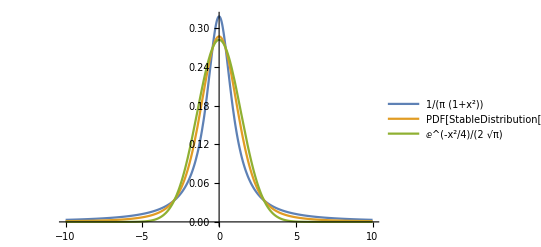

```mathematica
Plot[Table[PDF[StableDistribution[1,a,0,0,1],x],{a,{1.0, 1.5, 2.0}}]//Evaluate,{x,-10,10}, PlotLegends->"Expressions"]
```

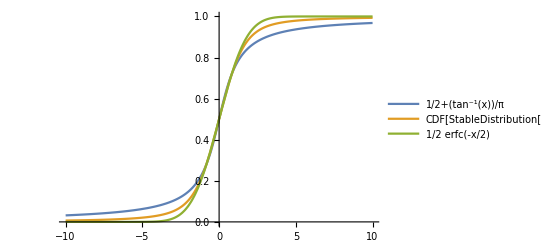

```mathematica
Plot[Table[CDF[StableDistribution[1,a,0,0,1],x],{a,{1.0, 1.5, 2.0}}]//Evaluate,{x,-10,10}, PlotLegends->"Expressions"]
```

```mathematica
(* For alpha of 0.05, can essentially put cap on x as CDF(1-alpha). Which ultimately relates payoff cap to VaR metric *)
```

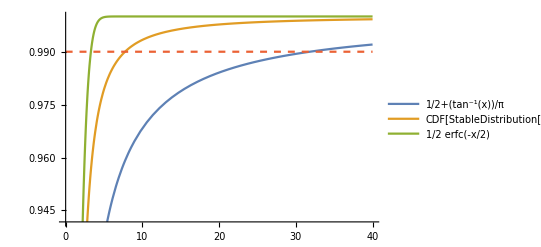

```mathematica
Show[Plot[{Table[CDF[StableDistribution[1,a,0,0,1],x],{a,{1.0, 1.5, 2.0}}]//Evaluate},{x,0,40},GridLines->{{},{}}, PlotLegends->"Expressions"], Plot[{ , , , 0.99},{x,0,40}, PlotStyle->Dashed]]
```

```mathematica
InverseCDF[StableDistribution[1,2,0,0,1],0.99]
```

3.28995

```mathematica
InverseCDF[StableDistribution[1,1,0,0,1],0.99]
```

31.8205

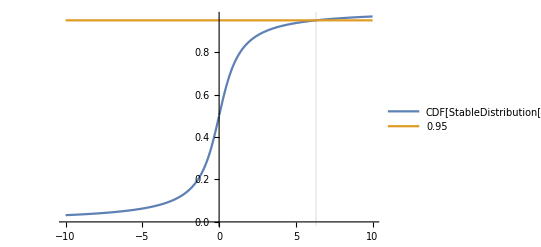

```mathematica
Plot[{CDF[StableDistribution[1,1.0,0,0,1],x], 0.95},{x,-10,10},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions"]
```

```mathematica
Solve[CDF[StableDistribution[1,1.0,0,0,1], x] == 0.95, x]
```

{{x→6.31375}}

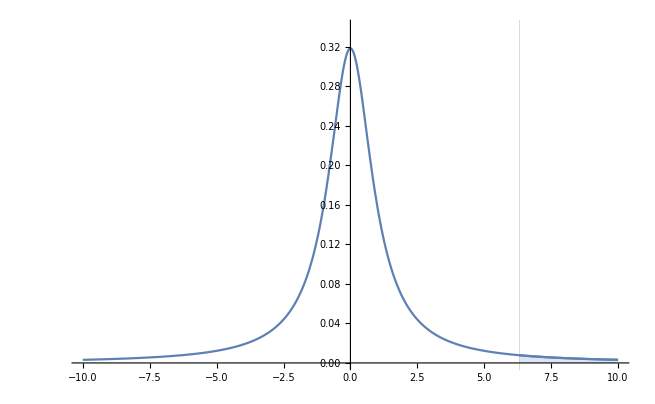

```mathematica
Show[Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,-10,10},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions", PlotRange -> {0, 0.34}], Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,6.313751514675042,10}, PlotRange -> {0, 0.34}, Filling->Axis]]
```

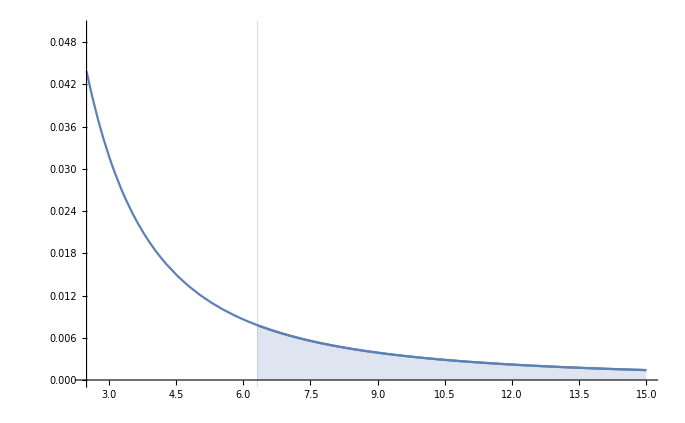

```mathematica
Show[Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,2.5,15},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions", PlotRange -> {0,0.05}], Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,6.313751514675042,15}, PlotRange -> {0,0.05}, Filling -> Axis]]
```

```mathematica
(* Payoff to a shorter for a bearish OVL trade on inverse market: PnL = N * P(0) * [1/P(t) - 1/P(0)]; where P is # ETH / # OVL *)
```

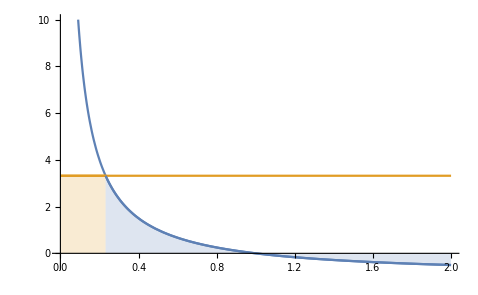

```mathematica
Show[Plot[{1/x - 1, Exp[1.2]},{x,0,2}, PlotRange -> {10,-2.5}], Plot[{, Exp[1.2]},{x,0,1/(Exp[1.2] + 1)}, Filling->Axis], Plot[{1/x - 1},{x,1/(Exp[1.2] + 1),2}, Filling->Axis]]
```

```mathematica
1/(Exp[1.2] + 1)
```

0.231475

```mathematica
Exp[1.2]
```

3.32012

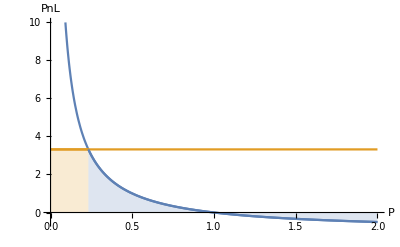

```mathematica
Show[%86,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Exp[1.2]
```

3.32012

```mathematica
1/(Exp[1.2] + 1)
```

0.231475

```mathematica
(* TODO: Get some actual numbers for e^X Levy process from fitting. smaller uncertainty level alpha used, means greater confidence in X max, and larger payoff cap to cut off tails with. This we might need considering vol factors from norm fitting were on order of 1e-7. Exp[1e-7 * 6.313751514675042 * 144 * 7] = 1.00063663 is a very small 7d payoff cap of about 100% on position. Likely want payoff cap of around 10x over span of 7 days, which gives Log[10] of 2.30259 max in exponent. Then know that 10x * OI imb cap is max amount we can print for one cycle, then we adjust cap down accordingly depending on prior printing on rolling 7d basis or something to strictly meet inflation goals *)
```

```mathematica
Exp[10^(-7) * 6.313751514675042 * 144*7]
```

1.00064

```mathematica
Log[10]
```

Log[10]

```mathematica
N[Log[10]]
```

2.30259

```mathematica
(* Inverse market payoff *)
```

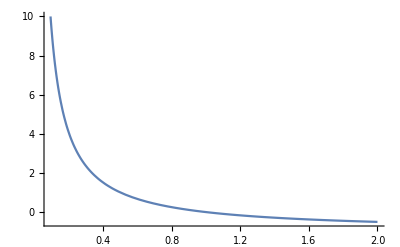

```mathematica
Plot[{1/x - 1},{x,0,2},GridLines->{{},{}}, PlotLegends->"Expressions", PlotRange -> {10,-2.5}]
```

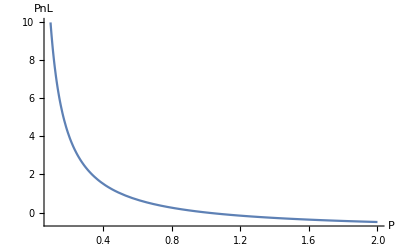

```mathematica
Show[%87,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

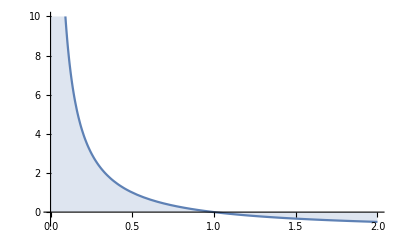

```mathematica
Plot[{1/x - 1},{x,0,2},GridLines->{{},{}}, PlotLegends->"Expressions", PlotRange -> {10,-2.5}, Filling->Axis]
```

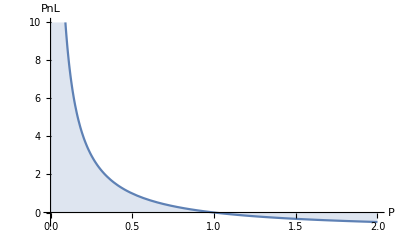

```mathematica
Show[%93,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
(* Look at how PDF, CDF evolve over time with e**(μ*t + σ*L_t) Levy stable increments *)
```

```mathematica
Manipulate[Plot[Table[PDF[StableDistribution[1,a,0,0,(u/a)^(1/a)],x],{a,{1.0, 1.5, 2.0}}]//Evaluate,{x,-10,10}, PlotRange -> {0, 0.4}, PlotLegends->"Expressions"], {u, 1, 10}]
```

```mathematica
Manipulate[Plot[Table[CDF[StableDistribution[1,a,0,0,(u/a)^(1/a)],x],{a,{1.0, 1.5, 2.0}}]//Evaluate,{x,-10,10}, PlotRange -> {0, 1}, PlotLegends->"Expressions"], {u, 1, 10}]
```

```mathematica
1/Sqrt[2*Pi]
```

1/(√(2 π))

```mathematica
N[1/(√(2 π))]
```

0.398942

```mathematica
(* Fits to log stable below .... *)
```

```mathematica
(* Import from csv *)
```

```mathematica
Directory[]
```

/Users/personal

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

/Users/personal/Desktop

```mathematica
tblWethDai = Import["data-1624665179_weth-dai-twap.csv"]
```

{{,timestamp,twap},{0,1.62208×10^9,2823283256860140896256},{1,1.62208×10^9,2807416500389253480448},{2,1.62208×10^9,2795741643020610568192},{3,1.62208×10^9,2778509477732340465664},3740,{3744,1.62466×10^9,1832467229514366976000},{3745,1.62466×10^9,1825074114325430403072},{3746,1.62466×10^9,1817085838281425027072},{3747,1.62466×10^9,1810494773684469760000},{3748,1.62466×10^9,1810804556505733136384}}
 |  |  |  |

```mathematica
Length[tblWethDai]
```

3750

```mathematica
tblWethDai[[2]]
```

{0,1.62208×10^9,2823283256860140896256}

```mathematica
tblWethDai[[2]][[2]]
```

1.62208×10^9

```mathematica
timesWethDai = Table[tblWethDai[[i]][[2]], {i, 2, Length[tblWethDai]}]
```

{1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62245×10^9,1.62245×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9}

```mathematica
twapsWethDai = Table[tblWethDai[[i]][[3]], {i, 2, Length[tblWethDai]}]
```

{2823283256860140896256,2807416500389253480448,2795741643020610568192,2778509477732340465664,2767564848768069140480,2745828354088193490944,2727736176961791197184,2723904417120340934656,2704041208582260129792,2708998176205846872064,2708957922445429833728,2707680174482197053440,2695944365447723876352,2698373607653926502400,2680266501388141330432,2673423211281161650176,2666463989650712166400,2668925655655276085248,2672304892498461327360,2672264892061090054144,2671290004550853853184,2676102749609320251392,2680973189376187039744,2681086512517085134848,2681496690461062987776,2684094842685771218944,2685445606165706702848,2691518278792935636992,2699480089196197052416,2708909234860988563456,2714017949890912452608,2723546549897066446848,2728078648189622681600,2732798404365623230464,2736205750350773747712,2738549164965292933120,2740408402492291809280,2739886973103981461504,2738068641775508520960,2732878279417753239552,2733355381023297241088,2735655334127838691328,2741228286855930707968,2745848754848815644672,2757789870614201761792,2762280882964944912384,2770548567386833813504,2779513401456473931776,2783505730499585245184,2787899497467968749568,2790789899692304498688,2791366744634267533312,2790821263474369757184,2790556018381197148160,2790723452908507496448,2790770215307542790144,2791987724722161319936,2794184780804205314048,2799389501740996886528,2806764684938647699456,2814906782405361664000,2817371887757828292608,2816793185512886632448,2815366164781820542976,2809467116446830559232,2803470728561516085248,2801977345391733506048,2807923845137556307968,2816680080810950787072,2826351345374143184896,2829230819690937319424,2844881108177347674112,2845526938817979219968,2846056004686242643968,2847537689695054462976,2850418206824573960192,2851198229594175963136,2846520213412607164416,2835347528921623035904,2825295899203810099200,2818306064597918416896,2810326163623777402880,2802070737570245902336,2799446644260921147392,2792347962078446747648,2784202986476482330624,2778894244584430239744,2776590124688538075136,2776063976221398007808,2774667734541455065088,2775545755363831709696,2777110666599693549568,2781645777707600445440,2782809883603595427840,2783597626896385310720,2783565619960353914880,2783616107572831453184,2782461397921646510080,2780847045569229619200,2778801122423983833088,2770690494359044358144,2763685248750425473024,2758349054928008249344,2751085303850299555840,2747635811933147365376,2746684526882016198656,2745777520215356080128,2741657219691517050880,2736040761441577861120,2730118456546317303808,2729194017367816404992,2732073404375411195904,2741814525208712183808,2754154590660082008064,2764600990201965182976,2771245643847911342080,2773747676599470784512,2773168989326951841792,2769723084663710285824,2767468909441710030848,2763474904951046012928,2754264607258120290304,2748689397428054392832,2747284647969646706688,2738768647034475905024,2737106038072822726656,2739042347835879063552,2737714545797494734848,2733199537401500270592,2727639776629335523328,2717504941397481881600,2705675741654665920512,2701537295952182771712,2697386693391145238528,2697833286035274989568,2702383409000679473152,2707925931600913629184,2711426836160066355200,2713939904832290160640,2717579224720621436928,2719523723107732291584,2719435624658441338880,2718772745880854331392,2717163327721008267264,2716716369920546308096,2713364872708867751936,2709093145137512972288,2704647051181212303360,2697702822871428497408,2687881069334521446400,2676254047251147522048,2668674387213850509312,2664841002990548549632,2661195127090204114944,2650837013261041270784,2636595156561490345984,2615922641776669622272,2594696982634963140608,2567401983976658698240,2554259939355930918912,2551452139358452187136,2544467547703244488704,2545674672299568005120,2552634655835315765248,2557364095492908122112,2557229231440502718464,2559261135056533979136,2561840674093749764096,2559455747088770924544,2558199312797410525184,2558234570959686729728,2556533722662629801984,2543908364674857435136,2525077729337763430400,2504085048701372858368,2490954607443703758848,2471019747624511602688,2473771551094868017152,2474205166847904972800,2481032975362977431552,2488519306973876846592,2492668158123786108928,2494217096224088522752,2497473160151335174144,2498700692681369059328,2496066495681120436224,2490647212750100496384,2480260423432623095808,2468266186043695300608,2464500857293495074816,2470620023525346377728,2487411240705092747264,2503925670203742486528,2533392288718655062016,2554130874169823854592,2566444149740772786176,2574862228426089562112,2582260545870247231488,2592882335138798108672,2589981365543947993088,2586541825629257465856,2580291249896334295040,2573165344251791278080,2564902755714955476992,2558623747259639529472,2519054105422384857088,2553437164742240632832,2553979638739994935296,2555590762809308741632,2557106974284978847744,2595501137458207129600,2549471457340789096448,2539441349495296098304,2527537236155754872832,2519343115205811896320,2504826876758170009600,2500222370939434696704,2497075382716709470208,2494745238383013396480,2491598542381085360128,2495483668252450619392,2495043884592296099840,2492649337524945682432,2600896358324474216448,2496021223463499857920,2502102129387371495424,2508308939175044317184,2517939151397641519104,2413592805809920671744,2519753151904606584832,2512242187905643053056,2505552689556493434880,2501227521480031993856,2499615875874678112256,2494927399103606816768,2485555547005367877632,2469847087498739056640,2448364955761812439040,2421359451529212854272,2396680479223380443136,2378993805613700481024,2367329145684726644736,2363443991403113218048,2366141807959089872896,2370934520687806119936,2374631411817024847872,2377755789930748968960,2378498121596980953088,2383631682552525225984,2389372727675175567360,2396914492739486744576,2405896014948039393280,2408807316656603791360,2419859296068828135424,2427903557470575394816,2434682181423286714368,2444230879166102765568,2460019185309773725696,2474184057239067688960,2489237812431203336192,2505180746918871957504,2515657642287079882752,2519018250493201743872,2520767422394483081216,2518190148023447191552,2514784667239870627840,2511954597927563296768,2509849272772669734912,2507480066680908414976,2507491349842502352896,2511848413215039946752,2515511699456128974848,2517944192531270467584,2519854977656697651200,2522367676595569164288,2519141447245468008448,2517510088221603135488,2516258036432883941376,2508456761927634255872,2500795860112240017408,2498440363433322872832,2511110178609707352064,2519857617219772481536,2532161703416493506560,2546987349195713675264,2556730605436576202752,2548204077968568877056,2546001124171610849280,2720404121477766447104,2540969987798688858112,2536402576658041143296,2531401878522376486912,2523108235309858422784,2322151657675870961664,2505792289942667788288,2496802532447629606912,2486728414798425358336,2481273357378150465536,2473657263267289497600,2466883898337083260928,2457772413614219067392,2446156390761049358336,2436336018925058260992,2428782132438112927744,2422255885024042680320,2422970639702658908160,2423725761651696730112,2426027551577464635392,2427313529624030347264,2427153316335251357696,2425636091167732400128,2423738039430212485120,2417609013878362996736,2420941218413676593152,2424258965240024662016,2428462021358738472960,2431491786797317881856,2439317568990628806656,2432728170292760281088,2425803422289357701120,2415400270012133933056,2408724593632735657984,2399525844886725591040,2388327531183771484160,2377372286317691404288,2370966492930961309696,2368958922356735082496,2378698763975640219648,2381261074101446901760,2383249763378020220928,2383349706933223817216,2381019069348638621696,2363721355825041113088,2349789120172185092096,2339036833022407344128,2330463437375719866368,2322139130728585363456,2316740207931736195072,2317695470187027365888,2320361306119120355328,2326580013440134807552,2336575633208275632128,2343571846044937879552,2345523491187067453440,2341412724437374992384,2328160867641592119296,2309940886570856873984,2292328948411657093120,2282051905432268046336,2268576893172937129984,2263343994718073651200,2262342945994831036416,2263337602828059017216,2264095801623798611968,2258173178879050252288,2252289157505998913536,2250241095917905641472,2248876442371697410048,2244236203581888266240,2242641905315534077952,2239773327464722595840,2233875521155791323136,2228836968636968337408,2232843070785021542400,2236648104912550363136,2237195445281073659904,2242680699555422142464,2248375923489227145216,2253356111269609340928,2257170431802223362048,2263784536606981488640,2268203867222083371008,2267596022037898854400,2265185175745727561728,2264805976942186070016,2267152951782084968448,2274185225482086121472,2280251556297338519552,2284257626830097350656,2285346105234963562496,2275902345532490907648,2258592434298569621504,2240259112253659545600,2224292279123258114048,2219125214757827379200,2214347698319897133056,2212919511201861074944,2214898705862768197632,2214980837063881129984,2212108389112826560512,2214239285407443845120,2219038517169432821760,2228195558270298488832,2239727314472643592192,2244889727562655989760,2259377460932225007616,2268323771509710782464,2276698677571690954752,2280434220083787857920,2280272596302164918272,2284672533539892232192,2286504837294655275008,2283640700188101181440,2284179565280738148352,2290536927134924144640,2292510256086412951552,2294068699445464924160,2301792303038777786368,2313127375851468095488,2322762095805745070080,2332066459418882473984,2348825811203421372416,2362773749040786964480,2375171995237565857792,2383735264508229189632,2389818086855935000576,2399003279267403923456,2406177659181134249984,2413088879769351094272,2418079187044910235648,2422923331640665571328,2428738583183230500864,2433068033040819683328,2436728357096947974144,2440639857249803042816,2442162048306789744640,2439497726913257406464,2436009395958482206720,2430850531980424511488,2428736046156604768256,2428539312246860808192,2428218667876490936320,2426285827203496148992,2424443119422261428224,2422634124671429640192,2421280772446745526272,2414685641922122350592,2413167864256971931648,2412098244603127791616,2410435911485065003008,2407964497416675131392,2409837353878649044992,2409089040030579556352,2406936341500033761280,2409990821034354802688,2416132174290223104000,2422463985835006492672,2426991936485537087488,2432516611941791170560,2428794284465060839424,2417097738362019643392,2404569023823657041920,2398917033407909724160,2392241724329568501760,2386698034199302504448,2386820975277023690752,2387321713440575193088,2385944404977285857280,2379408682027560992768,2372882240904831172608,2367258961065145270272,2362003591674879541248,2356871657073051172864,2356902446378294444032,2358451988811813748736,2359751911227686912000,2364007131836758097920,2368629330499039395840,2378065985509337858048,2390069350483627081728,2394722955101015638016,2401283795339037376512,2408459189628832317440,2411212904729735069696,2415056174014640160768,2417282066002721898496,2424458019038051172352,2428680339574115794944,2432196489134873247744,2436640247938106261504,2438850838827532025856,2446882552339466551296,2449959474720159563776,2450494754347279712256,2450690925929443098624,2449801621951049891840,2445360028262869237760,2441147454230376218624,2441398318899056345088,2441231793595948204032,2440483295563760533504,2440167222825230270464,2439742512861683908608,2434754585667057483776,2433526861806888812544,2432795708960204128256,2430564051215398207488,2428807382522874298368,2427196119823171977216,2422380466158122303488,2416183727128206901248,2413578561024218890240,2408699726227083624448,2403182170350860369920,2399908210545170317312,2396299498033665540096,2391469454117438488576,2387504255763645202432,2388532284102656655360,2385243742941454794752,2379443343517507649536,2374763208559244083200,2369620299216871489536,2362279360648227848192,2353292979922624839680,2345652560294698024960,2338482034639488679936,2329663334532047962112,2314232317492114489344,2310405710275992092672,2304603683678934007808,2302292146883544219648,2302579390120498823168,2305939123461628362752,2304988695182578810880,2304124486463766921216,2305147576852175126528,2303564170143304515584,2298483171365887410176,2299830086245623005184,2302327491702240313344,2299944593724148023296,2298865791116272205824,2299391258943584468992,2301733990431579176960,2301621178760467578880,2304306096636824911872,2310603934131796574208,2315559879755051827200,2319696790210039250944,2322788009533644996608,2330389634791029604352,2336501601687432331264,2345440323437380239360,2356976345899373428736,2365513621003247812608,2384707209845156610048,2395965941133844938752,2570155672313468551168,2574426340567860379648,2577297958474596483072,2580598572048631463936,2582923918759191117824,2715565447663336816640,2708320856724176633856,2697616133879103488000,2689638458975778766848,2675878430432149110784,2661244361886489116672,2651259983865066815488,2643990812401452711936,2636278099382840590336,2632083320878064467968,2635492743812619436032,2644207014314722721792,2643764831864321212416,2642904445222627835904,2641258453581325926400,2637012014478445248512,2628603021920060309504,2630558503477801648128,2635896114941285367808,2638525968591772188672,2644120824206141685760,2650567972795703099392,2659916487470537506816,2673114179195965014016,2683956717182165975040,2685933267297769619456,2685080060275754270720,2675062207335093501952,2663971586427732361216,2658670363307478089728,2654528051287994925056,2651833352640819363840,2649403121723301691392,2647761752567619518464,2643340139191984455680,2635311084036790681600,2624868757499244707840,2608494199904827080704,2594056292821190049792,2580016635481439600640,2576547618060458524672,2573751713689808404480,2572038794078543413248,2571690105143018651648,2570803840380943466496,2569585899440709304320,2572058490002816368640,2576547261802220093440,2583835977827362013184,2589984876089064816640,2596372934966450323456,2599300208001102643200,2604470050976481411072,2608965583553158971392,2614262308079360540672,2613683375790018789376,2607980477262178811904,2600001163007632605184,2594122755658051223552,2582242436930206695424,2573411782055848050688,2563741010803231817728,2561703180254293524480,2568258804597876850688,2577856271758306836480,2590063351562627973120,2614022428669226516480,2621945707621852381184,2621132670648063623168,2617020992052972748800,2610920347688779120640,2597623811078779043840,2588724381491402899456,2580652861936397451264,2569860419151654813696,2565061742170170982400,2562791380974667038720,2561105273158941802496,2560904197825929150464,2562568583776719863808,2560399743385491996672,2556142720892846211072,2552134783221719105536,2546271821713339056128,2540647440465291378688,2540423140733955866624,2542942782666516201472,2545945014178631122944,2551816519083655954432,2555716954514953076736,2560249974827626004480,2563251352072093696000,2563447932406450356224,2562524654913445167104,2560608184885893398528,2554257703375054307328,2548240327584565428224,2546405738505652142080,2543900644491517231104,2544843799964662890496,2549632112590009663488,2555072110007625973760,2559993476334450900992,2562762467649068728320,2567383026853496225792,2570104632170916610048,2570960340486723731456,2573775570396795895808,2580955334073237635072,2585624186840585601024,2587618182047589203968,2589565272619846467584,2589152040359995899904,2587790032932859543552,2585821084075665915904,2589105416686426128384,2596543982076617031680,2606254834893351026688,2613863200457767256064,2621283258933720907776,2618328609127445561344,2615255135840546848768,2611636447366026362880,2604168221139739344896,2594361413082867564544,2584993953804480675840,2575955864390780583936,2567652790401450377216,2564552401229082787840,2568448436077789184000,2574682604010515464192,2579605434526716133376,2587855810292561739776,2596487626709738192896,2600408793297687937024,2604063351643506212864,2609021001067092508672,2612930114119166066688,2616351596450805710848,2619191587591824605184,2619223320230168625152,2619156156582687932416,2620083646834565185536,2623237009308826206208,2625312007349457649664,2625611378829620150272,2624537914431297290240,2622157765459527598080,2618914195134614077440,2618394709803829559296,2619179471029016723456,2623228233724758851584,2627226958497937096704,2632371798373776752640,2637631444229387976704,2638831870692116922368,2637965209252937072640,2639960019335621115904,2643024145488400613376,2648965445164438388736,2658856923693062291456,2671772414101494431744,2679241928585557049344,2683791894013387735040,2688090079455627182080,2686992149721250791424,2686532291564848283648,2688314968920696553472,2692520396635379859456,2694707288270545879040,2696555940261351915520,2697613106743785029632,2696418604116663074816,2692964266891175002112,2690836394469534203904,2689173164908408209408,2687554488869799329792,2685586653425402118144,2683545162951967113216,2682989960692622163968,2680307485490012487680,2679372465322754834432,2679463691638466936832,2683327949371106394112,2686364551382130753536,2693080043099917910016,2698331561377800388608,2702635599349491433472,2704180526201060196352,2704100833018444775424,2700933199924669448192,2699251230540603326464,2703857240344843255808,2709868450666276454400,2716404237381523210240,2724403777165872594944,2730593507311706177536,2732121709245693427712,2734382606453125414912,2743316838597805473792,2750925315135166218240,2762328823190813409280,2773039763521783463936,2774717755595034722304,2779074220044939952128,2781289429840635625472,2782835037189942280192,2782217373987443310592,2782999304047485779968,2780398292066226405376,2775747016539446444032,2771429144432819044352,2766941230452612005888,2761780422068625997824,2758514208699430469632,2758013814773513715712,2757473046634811097088,2758024973535523897344,2758670589537276657664,2760572664829948985344,2762352110308484448256,2762949051230390321152,2763754137442586722304,2764324748310359310336,2765096950380719243264,2764476272107675189248,2763224462695417774080,2761803141367356981248,2759773479385558941696,2752755996184318312448,2746937792643180003328,2740793266107054555136,2734617831012473765888,2729234559713018904576,2727151595445431042048,2726520197139707985920,2725209570702397014016,2724889792943674097664,2724660023915124359168,2723732963558363758592,2721093155408199024640,2714212798297926533120,2707385374207747555328,2701124504532256030720,2696179532642198224896,2692597612352530022400,2695869970057652076544,2702116521682063065088,2705765933532933783552,2709267648916128006144,2706833037667003269120,2704471433963292852224,2701673426482421039104,2699143997241957548032,2697384857530353582080,2699797896454806175744,2700735320334001504256,2700275001247265718272,2697939085685949464576,2692952766757443469312,2686846355784343224320,2683274793619035258880,2679115599084985516032,2678335774984018853888,2684812661346314747904,2689044452270794080256,2696100835295861145600,2702291940650498654208,2709241091567094595584,2719874817218445312000,2725783873484140052480,2738473416198420168704,2746288987486025678848,2754234151564481134592,2765982989701810749440,2775404424115273072640,2784575938540402638848,2793798409572372709376,2797038221217986772992,2802613103337400696832,2807410250819032842240,2815084253981420027904,2821649526109739941888,2824890369953852555264,2829403940225479081984,2828528355306029187072,2825114169512691236864,2819191200419916283904,2818106611924882423808,2820080758008356274176,2824303371074664398848,2827426427759331115008,2831566641311877431296,2834271543358982193152,2837376414485655322624,2841241683656176566272,2844179489416269004800,2849373021065796124672,2856015830866606424064,2861268159146455728128,2868542930345550413824,2873664353163396775936,2878269371792918839296,2877900038235768225792,2870889122125730807808,2861715674020881367040,2852354485729265451008,2841850968198912409600,2829471967032912117760,2817788309550676312064,2809539140701844406272,2806224975751649689600,2800352080504099438592,2807828202021187485696,2815800725680400367616,2822993854803646873600,2820675616902295322624,2816010872211967574016,2806513206311457914880,2796955821806475280384,2790085281828187406336,2782565822307406708736,2779596123155906691072,2779987520962858844160,2780582100211340935168,2782202029952323813376,2786642510601519628288,2790276006446543405056,2794284413780576698368,2794819358669391003648,2792744412461941653504,2790008625698914697216,2790747815788384092160,2793576588354534244352,2799513057666381381632,2805467344923761049600,2814778378464306659328,2822283305580246859776,2827088354152751300608,2829462169267187744768,2829824804995829071872,2830133780667060191232,2830760056737062977536,2828656833920909705216,2822334938624491520000,2818588591918992064512,2811625346913289633792,2804918406377644228608,2798226329042042748928,2793694189314385117184,2792466350992074997760,2791647752059193655296,2791490267644879699968,2792462598748105080832,2793266127143517028352,2794431737058507096064,2794927283455135842304,2797328681960259190784,2803050952204222988288,2808946285848189992960,2816656477979203338240,2819545988447223152640,2823729886160320200704,2822576419421482909696,2821259741365709832192,2820615153010139987968,2823804013550949105664,2826824817411424256000,2830077430587885355008,2832849080820258308096,2836516060133680218112,2845046041733353177088,2849645424714348756992,2850883365434955923456,2847627880480539410432,2841872421412359634944,2830062423041989672960,2819996696953785679872,2810312396830017060864,2798119564928268369920,2784310828522269573120,2769988719236831248384,2758591769768837513216,2737262207437555367936,2726384793619426443264,2721447497966703607808,2717499308780138004480,2714918174819131850752,2714431254502593527808,2720120309083598749696,2726364775644996829184,2731961272919092887552,2739218376251850358784,2743120416675640377344,2751373727214955134976,2752928365405542547456,2750239997766776389632,2745792420734033199104,2742144449980316778496,2732818092727986552832,2723235547191651074048,2713971641941634318336,2698457566491047362560,2685542003995193114624,2672406956888630493184,2666190902748739272704,2662393088543472222208,2658414295364322459648,2651130686284943589376,2640057772229162696704,2627654379032925437952,2617246381883468546048,2610825312568304730112,2611948726409550626816,2613484614123104763904,2615618176938780131328,2619508040157724409856,2621862747874543009792,2622297698169066094592,2625108778696560345088,2624027862454389178368,2624100395050634051584,2623180441734873612288,2624006751375628697600,2628004046914858254336,2636820241750474883072,2644249605412866752512,2648948571941968543744,2648685102609653563392,2648655527752942223360,2642773235354306084864,2638406771050904813568,2636429784113519001600,2634956538187663015936,2632315566968007032832,2630931529244186509312,2618715285062291554304,2608073138812456271872,2599089328882822152192,2593067839944002633728,2597308929097398747136,2608852971672587730944,2622525710093482721280,2639534541706350297088,2645508657392803381248,2647946803644063547392,2648775297179021475840,2647652318556022898688,2640877961650851807232,2637720263456633389056,2631990390261202550784,2631030207959252074496,2633179387986335760384,2638148422514275516416,2641445316995047751680,2644980232469751005184,2646769897685868609536,2648739671947223760896,2654804054872351047680,2659605625232196894720,2664184637349025546240,2667850311140343021568,2669131910379433623552,2667173657201115398144,2667039761401466847232,2672347297817941245952,2679974222071630135296,2688030022035024379904,2693758389024537444352,2696153720775629078528,2694792833888695091200,2692338757786157449216,2690290897227198496768,2691451574454483156992,2694752877526071115776,2697385012802820243456,2697152303996270018560,2696592967115530043392,2695524238934196355072,2689874535454144987136,2687190583265633239040,2686142942803880050688,2687531526604793053184,2689060928474332528640,2693690162161369743360,2699350857103040839680,2705721505402915389440,2709063183236070375424,2718936884886513909760,2724281242538555736064,2726196054371892985856,2726196665823832571904,2725650845540048437248,2724027077477640175616,2723742797846887792640,2722717294896466624512,2719074210779900674048,2708111435538553110528,2699318569009382162432,2691136456519129759744,2683886049516130402304,2680837503199937560576,2688535102126789492736,2698345376632750997504,2707812329822851956736,2717888804620991987712,2734686794573074137088,2743059798661351866368,2752105502350137360384,2755797345400431050752,2757148921591678107648,2757880889731853582336,2758046883928524980224,2758853869037867237376,2759109303770352189440,2758712233692134113280,2757538017916176826368,2756782935961177161728,2758047383296636616704,2759994833160400535552,2761320147972558684160,2763213739451681341440,2764387160616504655872,2763816261876744978432,2763467732307190218752,2765514693172156432384,2766651637986621390848,2767561022681744146432,2769817199419974483968,2772214499764408418304,2773782633859547922432,2774755272310714793984,2772952772957045784576,2771117168277620523008,2767679606440676294656,2766706770430219780096,2766723770129794990080,2769241488533198733312,2771460285372795191296,2772668179819335778304,2773675547628049793024,2777198899141338988544,2781173246166026944512,2787919873151630573568,2791188780501537652736,2793619472016286416896,2791915671989643116544,2789737879040082575360,2789266044233454190592,2791544841467622064128,2794467353276905947136,2798285454632618557440,2800439776350452056064,2799874850304201588736,2788262726201440206848,2770370185548490866688,2748045109161638756352,2734342966433489616896,2717807240567132782592,2710383700657850810368,2709595216507008188416,2710826599718893649920,2705696349376126386176,2697920182238763810816,2688211554593118093312,2675393491568958111744,2658360523072982745088,2648066581317756125184,2642376442652575399936,2636613017906789744640,2637440536711394754560,2639050788381239803904,2636466995678228250624,2635839442919189643264,2634047940212958429184,2631072130773015855104,2628957943104132874240,2626163317410818949120,2623212741246948212736,2619807835267252355072,2617096920670101569536,2613847496168093777920,2611514165165617053696,2607758190372947755008,2605432371953832296448,2605269200310611476480,2613619098950207799296,2621958131420375285760,2629780661609822683136,2633732350429349019648,2636317008665792479232,2633532963611773763584,2629290244823484727296,2626090267372678021120,2624250842107195949056,2622418739006792007680,2622660138734963916800,2622564232392795488256,2622407220600031936512,2622694367017376940032,2623077544397755645952,2623492794702473199616,2624126240169202286592,2625189870661865570304,2625494799101880958976,2626363655232249397248,2626778667343339847680,2625541995874736930816,2622272537382309330944,2622233597006331248640,2620106881561145114624,2618729606513426956288,2620027072757396144128,2624112404092066725888,2623856292520083324928,2620317009088204505088,2610591612893098672128,2596880776513925414912,2583709130426719141888,2577722871185819041792,2567310345647206957056,2569468233822292672512,2572435217228513673216,2574892279715737370624,2575405095932781395968,2578174202102379708416,2580754406509080739840,2583121301858383036416,2588998502044324069376,2596151047977263693824,2603244954086065831936,2609948133392020668416,2617591258532937203712,2623383067156287062016,2625069888654662434816,2629994022251346264064,2636435943905350385664,2642803444718302658560,2652868266916373856256,2660413794848968540160,2666812281636131438592,2669942768531790102528,2674883313630384750592,2677909780179792166912,2678795297407415353344,2678192716519419936768,2676521363327955238912,2675040115862851289088,2673521923105510391808,2671658892462815444992,2670627503929776668672,2671875709776338878464,2672462478108009693184,2673736884058100596736,2675493568505359892480,2675939504481405763584,2677213463098821705728,2677986831165727178752,2678233060846608580608,2678303718147416915968,2678878537409630306304,2681833982027587125248,2683435051320436850688,2681513171639566598144,2676686714612343635968,2672921918549377155072,2667083237538741092352,2661719792652355371008,2661988284927158779904,2665549973287005061120,2669215500132935008256,2674118424782762409984,2681454677656785649664,2688733379286913253376,2696536271202404532224,2701592000713647456256,2707983771105833254912,2714089583509649752064,2716409119397917491200,2720553759460491264000,2723569866302833557504,2726333211622327713792,2725023669652498153472,2723333363224083431424,2720542359757736902656,2718225535742860328960,2713631987936247939072,2711533839101668622336,2709782564898963718144,2706880336126628331520,2704438807212788285440,2702617553445506252800,2699799901682844827648,2696212142411504156672,2698100252550853820416,2699371321017680003072,2699915228859516583936,2699915911640827035648,2699370058039511482368,2693788366008388943872,2687087661441708720128,2680920616219444248576,2677841395296954744832,2669794382253762019328,2666076540479315378176,2665898404841840443392,2666041919148028067840,2669388580037979537408,2678608684261605638144,2690774761233281187840,2698725897796276715520,2710453182245971689472,2715156279961744048128,2716919993829825183744,2718061483747350413312,2719215802103610998784,2720331402756750835712,2722128729586926616576,2723185160971300110336,2722113363733542600704,2719707557221259280384,2718243882330505084928,2712719187779361701888,2704295516426603069440,2700710689404225060864,2693876837540675715072,2692336528961136230400,2688478920398032863232,2687600506603253006336,2687144446380647907328,2686157458118444318720,2686195363314004918272,2685787914002045075456,2684404369708306399232,2682697124814457405440,2681740349001905471488,2678922985718959046656,2677986003615958433792,2678111773747611435008,2679906988766092328960,2683174983925048016896,2688556835436257869824,2693737429284208246784,2699620327316393033728,2703256157160689106944,2705335853491059949568,2705033498714073202688,2701407847938796290048,2696392093710641266688,2689769059653019238400,2685364357106039259136,2683948103064028708864,2686536092659138691072,2689427374118231080960,2693309663507626065920,2696244234897789026304,2697928679815854424064,2706737229682764677120,2714150319476261781504,2723004391884826083328,2732585657129100640256,2743140383608634605568,2746995323397418778624,2748781728920036704256,2751482994025877733376,2756259043327769837568,2761197309679982084096,2767482709501035937792,2775620288131434020864,2782442315195442266112,2785073303358075830272,2785207597365401747456,2785425919820821954560,2785823254882043822080,2785685705853010706432,2782647013692578201600,2778435278247358365696,2774070884315606024192,2772031866009912082432,2771882943166036836352,2772253211054183546880,2774280090814051778560,2776893351867510685696,2775424869160026374144,2774020486941357113344,2773653823167385829376,2773412962999320707072,2773183255588564369408,2774329317285708169216,2775266331216372563968,2777003418345335685120,2777950004460533579776,2777395892282270941184,2774261633968572989440,2769245593671445250048,2762180630697761308672,2756870986701298728960,2753477282569022078976,2751938600210181652480,2754482268930942959616,2757321468672492961792,2758725103783591280640,2757284011308290670592,2755854504271482454016,2754039895480906809344,2752224714790082183168,2754733344398484439040,2758332799846182813696,2763804017556298137600,2770837445431034118144,2779976201974185459712,2789193293235395493888,2801128341106827198464,2808679628154843168768,2818346104402279923712,2821672805533246029824,2822229710556706111488,2818494451480592384000,2817033411386196099072,2814999763365809094656,2813808985922332000256,2814499488245421178880,2817305690489527205888,2819767433382336659456,2824648723826162008064,2825608650780186247168,2822662257563326218240,2817948222995668402176,2812010998491862007808,2801384434971808104448,2792552931708039593984,2789134993692784328704,2783802406694165151744,2776629352676534517760,2774424819579513995264,2772985041575743062016,2773075345543245856768,2773157108425373515776,2775915994428248948736,2777450178286117715968,2777951545625145245696,2777242556486294437888,2774783644108062195712,2772738657112684494848,2769954320513141047296,2765265469758097063936,2759467341816643190784,2750580496726975578112,2745128987288049549312,2737476397314345533440,2728895612734500503552,2724631542662223626240,2716602583356122595328,2711320110770686001152,2707022289091279978496,2702182096248986664960,2695597723806906974208,2695315571684145102848,2694034209233158275072,2695343281551967256576,2699158801191407190016,2705425587724472025088,2711907263701455994880,2715876281149443538944,2716572926687182848000,2714821372057479544832,2705840964680116862976,2690823867451979595776,2672848837460775403520,2648482030685098344448,2626390525271912480768,2615417441378332835840,2603140897547919818752,2604098065338088816640,2607273971367855783936,2611078763289598492672,2613374253649909776384,2616171191241508651008,2616183625318517964800,2614837078319896199168,2611552913874109333504,2609087727684716331008,2603356837901687062528,2598164691713307181056,2594083590878683725824,2594559459831084220416,2589754041995642273792,2585972137830920486912,2583597551885271695360,2582885272097580384256,2580765949066344923136,2588143139542656876544,2593688367211491622912,2597898520074588782592,2599062275301398020096,2599203206646638575616,2596964323366239993856,2594589575602183864320,2580940843918548271104,2562651472569532678144,2537895599872625082368,2514931310156167774208,2492964040725498953728,2479819244693315649536,2477143930296823971840,2480110203360453328896,2488489496657328603136,2498570991723067473920,2504189872401904828416,2505698046124118507520,2506545589019784773632,2503118243937222393856,2500171115863549673472,2493750119805662789632,2487764710461009821696,2484812168538570620928,2483972163465304342528,2482517145493242904576,2484958538470870482944,2487812994433725497344,2487359084428139167744,2481521466277859164160,2478274735240447000576,2481038045892072439808,2486256636595084460032,2488984735388365488128,2499426888782963015680,2509439788361951739904,2517257645371946434560,2523134687654517407744,2528042168272334880768,2535724252469113913344,2538436778314013081600,2535353605696542212096,2527729783823437135872,2517340743066694713344,2508284986827684184064,2502957378059123032064,2501267635987277676544,2502862911140450009088,2501137143028872380416,2500627811384015978496,2498287925729474117632,2495009804932363059200,2491854285040702717952,2507551882221181206528,2496711008282012549120,2501761732134535954432,2508163675337690972160,2512475813948814262272,2502653781183760433152,2518537697478862438400,2518431735652223549440,2515460704940810829824,2509952568179081347072,2504156380553605021696,2497382642541847904256,2491350472196993581056,2485126474167229087744,2474903000681456074752,2459787770025621323776,2440000434198897229824,2425090294894755315712,2404682948289050968064,2389435487085250215936,2382304780415361089536,2371113870064370581504,2359286977933680312320,2349331685919209553920,2347573630483040567296,2348612326403148087296,2366628601682375737344,2382992524166543441920,2396301460342430498816,2402643543703078567936,2404808349354760339456,2403672631017622994944,2402605074733108035584,2401518825232539320320,2402255879382576922624,2403825134587114160128,2407131710994063556608,2414632174273932296192,2422201395074361720832,2433782724341738242048,2443876961684248592384,2453561422377404858368,2460351843317494317056,2465582073888661045248,2470778190016284196864,2475397574018373517312,2479018616298130636800,2482070399460519182336,2487430130832096886784,2493241935570598363136,2497524052013556432896,2507422984204870746112,2513436429239923507200,2520058147437240385536,2525852057666254274560,2526153720946853150720,2523687658321769660416,2521026678566013108224,2519187891182842675200,2519356269902538211328,2520918538207370412032,2528155368253980934144,2525219158280942125056,2524972487406426521600,2526102918036590166016,2525729472480836845568,2519896099479968284672,2521989152003403022336,2520800481268448362496,2515544630332974694400,2507533289843445989376,2501011666720457228288,2489156418627498409984,2479844234137880231936,2471432812804864212992,2466741992977146576896,2464743758922641309696,2462237054583590354944,2458316679268168368128,2454293836250361626624,2449459467162118782976,2442863090924668846080,2436055452147227557888,2435117952973741228032,2438575904260244897792,2441077433090166489088,2446950846136215142400,2453928935992780652544,2456264455685037096960,2457700424089014894592,2458478953543014809600,2451562990134263021568,2444280899096046206976,2438568806895024865280,2433597515457377599488,2434726148406491217920,2438124883911341244416,2451952781382999605248,2461782103482311901184,2471587102789929009152,2476819475278487093248,2478841813975702700032,2481037246009815597056,2486576430232524292096,2494839422131180666880,2504086698756340187136,2516879610035470598144,2524377979365657935872,2526064373364372799488,2526211801469576806400,2524369059834508083200,2517057925652035403776,2511786806294781886464,2506803788982437019648,2500356879616164495360,2494131034870982377472,2491825635335905214464,2488784276091795144704,2488632462319756509184,2488820946443345854464,2490904252366048985088,2492926520992246792192,2491059478359057104896,2488264885114041794560,2488872990729726066688,2489810105132828327936,2492539245827634233344,2497336353812403716096,2500469050759172849664,2501455805036506906624,2501389465311134613504,2506172241509608325120,2519250618880464257024,2530085595225515884544,2542019538942447583232,2553365122868209778688,2557159932978146050048,2552002759926867820544,2548652860568680005632,2541525251108566990848,2537614781544490074112,2533307629424631873536,2530230863321555271680,2531257311937571061760,2528227155730996658176,2526708848013300203520,2523996432796444262400,2517120233172678213632,2512567883774510497792,2513338576424460091392,2522849886810853605376,2532971263803778924544,2548533600473808633856,2560197310019780214784,2564331643884112707584,2568866731829282996224,2573627219701312520192,2582681373442609512448,2588989480751558295552,2594847189266609995776,2600460582749137797120,2601179285032332165120,2597854724472416763904,2596039954904954437632,2592445038315580162048,2590104412346973159424,2587721420712670920704,2585063641999337324544,2581024975233472266240,2575000405685274411008,2570014755127734829056,2567691649272217862144,2565600408023176577024,2563466548164533157888,2562623111473514151936,2561752317504707887104,2561106054265355894784,2561639432150576529408,2562311375527506608128,2563508989886828904448,2564165119843984998400,2566027787824634265600,2568359904054436429824,2571319406111576555520,2577106531049735192576,2585153278938502922240,2591423645836966363136,2595701583839957614592,2600467971739120828416,2600853678889147301888,2599458992777515761664,2598765655729103175680,2598495978204324954112,2599263773867781914624,2600581864762865352704,2599136024079593635840,2596899168411493335040,2592270070291717685248,2588113720728487985152,2584122241696169197568,2583229699540412006400,2584048326539055464448,2586597679788982272000,2588195862554280984576,2587199595675764391936,2584292265584540778496,2581125375847180533760,2576178290357398142976,2572772540004180688896,2569424663245117980672,2569586160058749681664,2570988713617032478720,2573662489263730589696,2576666289816529272832,2577839268983876878336,2577796635661764657152,2575266760705432354816,2571938377157203460096,2567361183107580428288,2562869740701000138752,2558470136057143754752,2555309868544112984064,2551976571509768978432,2546644970162775654400,2543263515479439310848,2540487811998966874112,2538398774927312814080,2534375130590288543744,2531897128879485091840,2531835217752022843392,2532314979970811166720,2532717856010587865088,2533374725957637111808,2536167186739328188416,2537425739310700167168,2538204495224619663360,2539458097697279967232,2540580484311103832064,2540449463980713312256,2539891325392318889984,2538858172911529230336,2535909903260545187840,2530543996766117167104,2525033392885231779840,2518385132028168765440,2512257688511253053440,2516343022877865410560,2522590893984695451648,2534970445740011683840,2548395363083930828800,2564306014270758322176,2576491308088262393856,2583222998425563824128,2586118065138723454976,2585060508090200227840,2583527342371664560128,2579285770250705436672,2575893288724792868864,2572879408443407466496,2570915224218427195392,2567375586594066006016,2562058097423104868352,2556257256231291322368,2552603655724900286464,2550544660764319809536,2548585565582845280256,2547324347902949064704,2546322986207005900800,2543528164334392836096,2540500759974209650688,2539141704848733372416,2535666596378872643584,2533932373454001012736,2530640019975246446592,2526180237191466713088,2521867687402146889728,2520476276065166163968,2520160841081225740288,2519314038242777497600,2517639619191840964608,2514729090899625639936,2510687714956361072640,2502909094865384505344,2495987664192045842432,2492200644938456104960,2487801599082437279744,2484914955178021486592,2480391888591578464256,2474737717046751526912,2469835487889845125120,2465579371907264282624,2462301699032960466944,2462548212679968817152,2464078008252241543168,2464527299545914671104,2464611544856754388992,2464369464271369666560,2464685582810004062208,2463137644183177134080,2460931674843728838656,2460895372250158989312,2461653738336520503296,2457899823808813989888,2454105869699861446656,2447734412035019505664,2442498065319141048320,2439457055778515451904,2440338384611831185408,2445437489475202056192,2453861247624948482048,2459627479137708408832,2462472708758009020416,2464853537829883478016,2469410921434184155136,2472863124072246018048,2475124343020938330112,2477791132979844612096,2480170070706810257408,2481497011751416233984,2481935456804848795648,2482443566482641649664,2483199108275620020224,2482463096152890802176,2477794244484260167680,2477891241985676673024,2474746413363066044416,2470979943602860326912,2465071318334104403968,2460913202092334120960,2450995101986218573824,2439558343307633360896,2433389609498277052416,2424231643103775686656,2420919159402910449664,2419898631893345632256,2418423646332954607616,2418311583359378128896,2419477736252144353280,2419348917729162166272,2422088576662671720448,2432196574945185628160,2440368301073036738560,2445862403295011667968,2450261906188835749888,2454185328068284383232,2455864258119684587520,2457343334805411987456,2459119356399121858560,2462120207864398610432,2466001271517989568512,2468291537339134509056,2471253676502551101440,2473724518360364351488,2473855164401173135360,2473298660222006460416,2471135422625784266752,2467013580942042202112,2462608491307802820608,2457439711192178229248,2451910593711621275648,2445418209515862491136,2439184975590561153024,2435100575080550760448,2431010631919956656128,2431950023393285767168,2431572931894137847808,2435446113711717613568,2440165729310042750976,2445094870909333274624,2448946808128090406912,2452068624463493595136,2453417273688028872704,2452672173805283049472,2452566173555602489344,2451425332608609812480,2455545885682257887232,2457945492051718569984,2460839680052621213696,2463673226468565975040,2464239699531162189824,2465077006465526398976,2468576344861920722944,2470355777938125225984,2470998531843573153792,2470747932189712187392,2469706304454430556160,2466876084208942448640,2464679312875734433792,2462683169455456911360,2460760234195309035520,2459319643936343457792,2457979397547437326336,2456901599691603968000,2456937673266424709120,2458333701240331960320,2460252834935822352384,2462406166251830771712,2464386691774717362176,2466590375058807980032,2466890685129769353216,2466608002402565488640,2464574259279600549888,2462400291125075640320,2458501279799700357120,2452248687404506415104,2445561639384626757632,2436788709468942630912,2429134863081352462336,2420963147570450268160,2416892131935139135488,2415372940176297820160,2411601406397187620864,2405652886770950340608,2396419400566471917568,2389664079900057796608,2381579373803857248256,2382379008547950690304,2385561930114712207360,2389391227031845339136,2394292000312850382848,2396011219269667782656,2395853149756660383744,2395158127131323531264,2394728251578342965248,2395771989860829102080,2397500082573699186688,2401858299841327661056,2404398329259763433472,2406030981809273569280,2406067656645995397120,2404043199587242475520,2400676188912438738944,2398227235937606696960,2397373617118177132544,2396431345902423638016,2393273820749502087168,2388754765267172065280,2382057106604471353344,2369349410712323620864,2356195902654176296960,2350240816316723757056,2344793970146449817600,2344145169850599735296,2350781728577335853056,2356748685670191988736,2361289001955971563520,2362233777248046940160,2357501047799315955712,2349831858028866961408,2345255080395606065152,2340759893727857082368,2339659297241125355520,2341072520086790602752,2342289378997884682240,2341647927621606440960,2339744955000885870592,2337672364894561763328,2336455724735118180352,2337305392552192770048,2332149329740027396096,2326046123284732313600,2318951364293038178304,2310307751708275245056,2297231270768012689408,2317956463755289952256,2282466455970572926976,2277273844783680061440,2273701227853411516416,2275347808466426134528,2251663575451959820288,2284843636842982014976,2286332330263843176448,2290147302710132867072,2291546396371875790848,2290725371462683197440,2291316309930098294784,2291789632675269836800,2289164455161532776448,2286773084781847511040,2284392714134367502336,2283792073613722517504,2284945050621253779456,2285999682658461024256,2286426937281973583872,2286759905435439595520,2286823867749924864000,2286994121331161694208,2257341702714195968000,2289155893736853733376,2294639013656889917440,2296350715016861188096,2302931843464126791680,2343196769077410398208,2313426907472913498112,2313623254736650371072,2313512363944791506944,2313410421468997877760,2313196284569950355456,2312424026418149326848,2311613150359340974080,2311912500477357719552,2312557484479174148096,2313176501116933242880,2314173262467605200896,2316251677487570354176,2318034365546434396160,2316782148458734682112,2325870650889875488768,2338881278814636474368,2352434668930192375808,2360557288651100520448,2377968891920638279680,2382094807344667951104,2381528277489661509632,2379949236908858015744,2380537895838419517440,2383752927227781578752,2390343820483261628416,2398610992079086026752,2411736868485627117568,2422499958241165836288,2427932186610769068032,2433242350818182561792,2433446297207424155648,2433462165560647745536,2433924911656216297472,2431711845485317193728,2428891048466810142720,2423596558073220562944,2420314587755146903552,2417909416383909724160,2418437465014646341632,2419084942127961473024,2419386098682145275904,2417758617323250909184,2413988784838109298688,2406357678624180011008,2403588149132068388864,2398350425236827537408,2393121433999287779328,2390885873340707241984,2388900338102816473088,2387383614391657168896,2386450591590869630976,2386417548019998654464,2387362972813576110080,2388471972081522704384,2391402512018200592384,2398051037499552169984,2402340884118531211264,2407292645677784367104,2410438373390285275136,2410581269398316122112,2410890066290029363200,2412256342158202634240,2413879348061301899264,2415310754294645915648,2416583523329481113600,2416409034046105452544,2415351924868165140480,2414051960290847752192,2413963182825184165888,2413700592288171294720,2412098373844796440576,2410850990745561595904,2409004083510134177792,2406767500389626937344,2404565685679954067456,2401126322979396911104,2401213128045708181504,2400490545315734618112,2397404876846757052416,2395354122791794769920,2390792187638147710976,2385068513765818368000,2381801207107517153280,2380791502428187394048,2381197020939730026496,2381534220503264788480,2381082328724075970560,2377545859144092221440,2373089851811965173760,2369247823062397616128,2364366140438267035648,2363999904021892038656,2370289455969571700736,2377680789821001826304,2385805411600817455104,2394835918266787954688,2401960748242684608512,2403702417185150861312,2404036414530201845760,2404367006111950700544,2403054440897997438976,2401433742239292981248,2399314404886903259136,2394399219958582083584,2388937009174793945088,2379053024874579099648,2367222605126403883008,2357806831272677343232,2346289789334329229312,2340631816502979854336,2335080393807048474624,2333980052342256959488,2334974470592226656256,2335517543475908968448,2336022822379791319040,2334695539507832553472,2332612571179090968576,2330101523875891773440,2328075000390912573440,2325039199234090074112,2323117761274663403520,2322340647511933059072,2321477795980985237504,2320303795535412461568,2320987167774208163840,2323727519154435522560,2326690365104277684224,2329063014288573333504,2331228043291198488576,2333291959748396843008,2332518887021910687744,2331155416192516882432,2329890514284160483328,2331503288924217540608,2335415478621047095296,2339610336510753374208,2345610524250355531776,2350308820151775789056,2352652665492917190656,2350860427203363471360,2349884331073117093888,2349842916141164134400,2351370654052622270464,2353152074477118685184,2357472924619646959616,2360210955640015421440,2363663231382906208256,2365346927534329561088,2366913732308424458240,2366693963901239296000,2366023006362868908032,2364774558619970568192,2363348229175468621824,2362887096610501689344,2363403233298013487104,2364567427783887159296,2365112417009014407168,2366117838625379450880,2364349409485700202496,2361304083308227330048,2358463648476928409600,2356047763571047661568,2354629657991153713152,2354410212857871597568,2355123896937749676032,2353873294749767303168,2350835873052783542272,2347384838717011132416,2343109010525972332544,2338903001243642494976,2336586963202514092032,2336551265252620369920,2336737753143310286848,2336928698294890659840,2338651929943704600576,2340076655942312656896,2345834842157864714240,2357458987318724788224,2368573585971598065664,2377214890177686142976,2388342382966828171264,2393436048238520041472,2394757909455827894272,2396088804457371926528,2398705255545287737344,2402867302821856804864,2408314082983007485952,2414284552587573198848,2418058228141873692672,2424911673547283759104,2428744453260266962944,2430342093713861771264,2430521301984563691520,2429325237378241003520,2428185106444677808128,2427608989971636027392,2427432762981596790784,2431941434237457006592,2440621916268867354624,2452563767603314556928,2464181026182759186432,2477542467403152097280,2493424810877675634688,2501245694828405587968,2509653596233692872704,2518166422013235691520,2523860847546841169920,2526043093155893477376,2525709533958372327424,2524583435940015898624,2520853450601798303744,2516494755904047546368,2514403584074046242816,2509119735754719756288,2506819288195183673344,2505214857547889508352,2503323557788593422336,2501208573479007289344,2502235306961253957632,2501417444335447703552,2500118572024402018304,2499116029640378417152,2498409322047434915840,2496053772688267673600,2495590487384796430336,2495340178129013440512,2496458688768483262464,2498953150669452738560,2500181822265970130944,2501446420213620277248,2503225512904505688064,2502639318363944255488,2500483935224350113792,2499801555144634007552,2498599143677347495936,2497572697675420663808,2496514774054734397440,2493426959991455088640,2489585333313964867584,2486170508492024053760,2481932309384369537024,2478254951710508711936,2477019061099436179456,2476959966875965456384,2476716085296822747136,2476449478148277927936,2477070210999762026496,2478096316457532522496,2480578504953053577216,2484797222494756929536,2488933147512751521792,2492974424888487444480,2495651751355681341440,2496205360632458379264,2495609041796329373696,2495140210479365357568,2494467787702533095424,2495930807781160386560,2496977787540321337344,2498326581252149215232,2498778477153763196928,2497777339782241189888,2495604205234195791872,2492272347783225671680,2487108775509728165888,2483432922995615072256,2480430598662357254144,2479712704679465451520,2480537244600901304320,2480424223454102290432,2480520166192799285248,2479782145962799529984,2477508191563193778176,2474593523061522169856,2472898728924138176512,2473168826679041720320,2475181810362676150272,2478790435789827735552,2481596500897614004224,2483664532433391845376,2484524732869466128384,2483936745477341446144,2483371259832907595776,2482323770130946850816,2480965761306488995840,2480149922395363737600,2480614900419983835136,2482612945887634128896,2485778046853169807360,2493359478638561460224,2503436814681293455360,2512765727459969597440,2526264457501437591552,2537682378991934111744,2544529767544621367296,2551267758626673000448,2556900266627319726080,2559892639922630688768,2562706220786057216000,2564679488345268027392,2565252267577049612288,2561589158897755095040,2559448918925986758656,2556648502539002576896,2557145363974239289344,2560894894793317416960,2566735249587334283264,2575578488125212590080,2579917365599030214656,2580032609655674372096,2578318261273586827264,2575558686739822804992,2568239603319541071872,2566968527922421825536,2567127620635331133440,2566594919259786182656,2566845986728051736576,2567652055802832224256,2567853589142221881344,2566294162499094708224,2561438161780493778944,2555336052859271118848,2546884810895987310592,2537311669455251570688,2531639124559189245952,2529369622176885374976,2528211748196914298880,2529196638229669347328,2532173435592398864384,2533252057941962915840,2534257118762136240128,2535015766749390307328,2538965998147082387456,2544161514910479024128,2547221051904703332352,2552795439521447542784,2556682657295933898752,2560512751274832166912,2560786192397224640512,2560948673303468834816,2560906962440689287168,2561118807595322703872,2560649138801178312704,2560273237439550062592,2560400607821084229632,2561637276031671336960,2562964456450049441792,2566158126262354706432,2570120001449443196928,2575989296142711521280,2582380957893541232640,2591752163063445848064,2598794118000184131584,2604017369671413530624,2604114684807508131840,2602201005173487697920,2598229982729085648896,2594788429676402966528,2591866739937698643968,2586452031967461900288,2582896981703722008576,2581799017686622011392,2579971936739115139072,2580308227144290926592,2582687050055717748736,2585262821075789545472,2585888898663572307968,2586428024172420005888,2587600286549614788608,2587776951873031897088,2587462701559604838400,2587454368561212424192,2589023143021684195328,2592112237593562185728,2600666166161482711040,2602669752218502561792,2615301031361771995136,2620032670279584972800,2621869092073986064384,2621399062966722101248,2620624619918426898432,2618420243224785846272,2618528286257657151488,2619090367244299403264,2619897691692982075392,2619893654346028023808,2618883706931163693056,2616770493944926044160,2614462684811253776384,2610171451309430931456,2608139105635834265600,2607750333092167417856,2608552225028182638592,2609551563837697163264,2610938159992723734528,2610496412234025009152,2606163873878973612032,2598407129265185226752,2590504507288996806656,2583896529256886304768,2579763095068234743808,2578963753553703206912,2578980607670702571520,2581128743716854956032,2583061066389008154624,2582848664637162389504,2582996279673499418624,2583081636797236117504,2582527108504437129216,2582025894612400865280,2581741763918939291648,2581084140202915528704,2578933282994660048896,2577878987779695181824,2578620586358320660480,2580260281470926454784,2582076122459576205312,2585074576467192971264,2587820545134016593920,2588957652674342289408,2589424032346987823104,2589832181832495398912,2590786082595724591104,2590914391894383919104,2590015669622705487872,2587790139333536645120,2581646568012846727168,2575051498409914007552,2570805097241782517760,2559098042766741471232,2552983802609695981568,2545771460556734595072,2543729971842061959168,2543003647756063997952,2540484747285396193280,2540512699064059953152,2541845300771827482624,2542603329751222845440,2543704748787607535616,2544872986164929757184,2547723739937236844544,2550904580227885170688,2553072106315319345152,2555329041664482213888,2559958030789934841856,2568770890373535891456,2577014893729980874752,2583772876460291784704,2591948793667339681792,2590018548712419098624,2585591003261053698048,2580842136728205524992,2572681045538956115968,2564728269433864716288,2550543971275831771136,2539921751596360269824,2532676955644707733504,2527801842203757117440,2525759432464314400768,2524438280536949522432,2525752163951620128768,2527369079740664643584,2526913621884589834240,2526864576726271787008,2527435002883035627520,2528452029490825003008,2529981187477534146560,2531933709110680223744,2535711914907963228160,2538592694252148359168,2543206205506828369920,2546875333118797021184,2549924857123953442816,2552546360928476069888,2552934997674662297600,2551318287023997976576,2546238618082954706944,2542431811528193736704,2535737661379139600384,2531983205273789530112,2528870133330288312320,2526251891619523461120,2523280366394331365376,2519658216188308619264,2515934368196225138688,2512223486834174328832,2511249508609868955648,2512186035873126547456,2513410501480102756352,2515071775011269246976,2515888639704306810880,2517154972713735421952,2517871206270930255872,2518383752897738833920,2518652665410897313792,2518675149167521693696,2518506011936788316160,2518276143732439384064,2518162059854044725248,2517986480193007517696,2517562901183082266624,2518499331044281942016,2519811504900015652864,2521141456453007572992,2523677791908668112896,2525813797856783892480,2526515804169473359872,2526419662738920833024,2526339694165620162560,2525818612756075511808,2525222862753244381184,2525014747553029685248,2524834723798600122368,2524856399426956034048,2525510703083839553536,2527758815382708158464,2530877034515198902272,2534153437851767799808,2536116131914570530816,2538953603211352604672,2538019493206687219712,2536798306982290784256,2534879334056676818944,2532692261509524881408,2530603674180199645184,2529366925189203886080,2528073431296658374656,2524994605552859348992,2523410633097536864256,2522006327726083407872,2520568222338716794880,2518628661284693344256,2517343437115376009216,2515311466534481166336,2510636214091530633216,2505962342946317008896,2496577535131761246208,2491145943351413964800,2482460613382081347584,2475075166073867206656,2469287098019187523584,2464251298705959288832,2460773017055199232000,2457184713772491079680,2453395312025676546048,2450694129653897494528,2448241154329361252352,2446551551203500097536,2447542031350412345344,2449835165820501622784,2451071485709708165120,2453129732229531959296,2454535694406836027392,2454446888307847069696,2452992750916157308928,2451335308756858699776,2446675109196484575232,2440056563666270027776,2433290732956709552128,2425970832574007738368,2416847972947291275264,2414747536317357752320,2417105356922699120640,2421218394986763517952,2423676009010388008960,2426026569689102024704,2422471343499472535552,2414169608933955076096,2407323865988998889472,2400842975582576705536,2400518260887749918720,2403945579768753160192,2410854830875643740160,2411062845849202589696,2409499506132198621184,2406993531623418888192,2406732132349062414336,2404540358615555375104,2408157426831598813184,2413244432407128440832,2418824442763587092480,2420725382043640266752,2420007767771554250752,2417283899320131125248,2415085420682300882944,2410783104072011481088,2406978402828931301376,2404252870211187769344,2402479531651880189952,2401443767293070802944,2400618542952295170048,2400091375210747920384,2401412311012354818048,2402953127553949761536,2403254659052818399232,2402646386506822320128,2400174942555279982592,2395309411194567131136,2386071772285089873920,2378901950203541061632,2371196794373784731648,2365266792414199152640,2361716099585801191424,2362304428409018646528,2365853290547393855488,2375384141844205535232,2381749046871664361472,2386543767305620815872,2389305713648960274432,2393185768258787606528,2395978723919891267584,2397222959777299562496,2399402042008649334784,2401321807408353771520,2403058047770304708608,2408299865642156163072,2411369955389236838400,2413832980386044968960,2416704283669977628672,2419301584871590723584,2422313894783484428288,2425497023992327831552,2426972327349977612288,2428091539619109666816,2428329265758196989952,2427937791038914035712,2425913918710803857408,2423481869013588901888,2420985170965072707584,2420140871403901026304,2419252405460406370304,2419141642967672946688,2419400857371068071936,2421289866203287781376,2423335677241236914176,2426458704851775258624,2429457588807625342976,2437419465754499612672,2441314571338505519104,2445171623169731067904,2447173736162477473792,2447983520745722478592,2447256045936428187648,2445991685949220192256,2444694358970860568576,2442364531411766476800,2440183198652161327104,2438641551160959827968,2437413793263055273984,2434215602839297196032,2433376603655459307520,2433451283616513916928,2434710263877511151616,2435122486874796982272,2436126906901563179008,2435984771539319390208,2434729273960082440192,2432417149470738219008,2431311908113749114880,2430128228674677768192,2430205741218898903040,2429790276250124681216,2428533505858346156032,2424072348668746792960,2416139489499167064064,2407906827917476757504,2400565959426144468992,2393588849493465366528,2388751306381248167936,2385899926877036347392,2384121299015280099328,2381927695227601551360,2378945000002552856576,2377638417034758848512,2377492493151350816768,2381501849826604613632,2385118881292987400192,2390019036151319363584,2393665366325820653568,2397950969953289502720,2397561106185779150848,2398343060819959873536,2400457224057406881792,2401586306994690588672,2402634856104037711872,2400624046881163444224,2394034249111568908288,2385361334905107120128,2375324050471677591552,2365693147323871264768,2354011156262071828480,2340233948660527792128,2332912783696617799680,2324913700833816215552,2319080026512482631680,2318037349379490971648,2318286575366771572736,2318844808805175001088,2320339587408330752000,2322005284787542294528,2324006482071330488320,2325841098319259762688,2328201093585958862848,2330119055806081269760,2333555269439726026752,2334294788622286848000,2337511476629581070336,2339529536069751799808,2339384425821809672192,2339557982236052291584,2341134692322037727232,2340351458023786938368,2338946488499319078912,2338297768328587116544,2337302214726685294592,2337020934348987695104,2337173805557809414144,2337662994936126242816,2338189030945496236032,2338430618475555454976,2340236481837175144448,2343100113342921179136,2350600564371684851712,2355623946786546647040,2360976672443683569664,2365550615463557857280,2366152042796290670592,2366363638302901796864,2366619944594109890560,2366894929744731045888,2366388040693238464512,2363169105995594465280,2359049315804697591808,2355372979967334285312,2350369522205019602944,2341770283553511964672,2338203776551189479424,2333312102881995522048,2328015973863960084480,2325816993762892316672,2324952357394528862208,2326787192779549966336,2329211504249137790976,2332835792555472846848,2336193784467263848448,2336993639970609299456,2338370579158784016384,2339243959486069342208,2339780840604083421184,2340261546881515520000,2340570841793112834048,2342478134610759778304,2344517414603841077248,2345879919390421417984,2348483456666551713792,2353204957485788299264,2355939157067044487168,2354993093952969375744,2351764734810702479360,2348369091359814189056,2344717815180255559680,2338279105796921098240,2335813488420629250048,2333788059643739897856,2331370509407624101888,2330829135078328893440,2330676728540340158464,2332424714775985127424,2334134683796286996480,2336709864210677891072,2339965095137846231040,2342700295542581493760,2344427975136858603520,2345569027883752488960,2346718381372969844736,2346530651742776066048,2345219097192338817024,2341500245517542096896,2335200665736205303808,2328313474495018434560,2320224611946562060288,2310106415698661343232,2304458770596076978176,2300133415951640559616,2303168887530914578432,2308482742502184452096,2314524799629592100864,2323421070461381115904,2324087901619391561728,2324901387823116713984,2323286772892476637184,2321211336432994484224,2315272873542198755328,2309759174792857780224,2306398231742480646144,2298731756098622062592,2290685215947113627648,2286907812079083716608,2284085073638861045760,2281636466531778166784,2277746480552807497728,2276569642438929416192,2273423396788631240704,2271033073115769602048,2267604995741273292800,2260507596856101437440,2254636416594461065216,2247658233980368191488,2243923965640244985856,2244686069469798989824,2243736790861119488000,2242206252366843346944,2238934006272743440384,2233904290875542339584,2226454578734280736768,2222456135375169257472,2221670968670855888896,2219358158015192104960,2224506991405732986880,2227906795942382927872,2228905972323441704960,2227249714088613511168,2225138709317901352960,2219128223732952465408,2214362321571170484224,2210518354985343778816,2204130671655541800960,2195369003396748279808,2185532698196696891392,2175138062937782747136,2165880408370750160896,2157154671638940745728,2154746049815210885120,2155192747630008467456,2155638618410260365312,2156335241127807942656,2160089703034393198592,2165102446743694606336,2173514699124391542784,2180553513208027283456,2186202827932464840704,2189696994890416128000,2192578802733275676672,2192967493681432231936,2195771452015102656512,2201746941898948608000,2205310679395061989376,2207520259568651993088,2208916874909393879040,2209492737920263258112,2208697080406775955456,2207043694103824171008,2206176226734217363456,2206021131607590305792,2206998487307934760960,2211234973611542446080,2214237726286333870080,2218127067532633309184,2223882882382057177088,2231578314778018840576,2235145684864934608896,2237348475130157203456,2239836575353958825984,2241783148906956718080,2242905677010483544064,2243108049040370565120,2243820751294793252864,2244303847610835795968,2245200805666464464896,2245391436460331106304,2244575631567278047232,2241026454086415810560,2236824925050135379968,2230736156389748768768,2223810722361768411136,2215796046909158195200,2206956354400202522624,2200084474462634246144,2193677425933820362752,2188994273384781578240,2185799040513041235968,2185941113547133288448,2189356145106427838464,2192209115844879319040,2193379606412804489216,2197096919043153854464,2201789227885787086848,2206013548065239334912,2212159971734142320640,2220656400798023680000,2228979870508082528256,2234714723049249701888,2236924441741051822080,2239599730447567290368,2239870749778336284672,2237611364706442543104,2234888274075321892864,2231099519643581415424,2227839150687222497280,2227162103500928450560,2228762189384047919104,2230580496599392452608,2233162589794864201728,2235906808294407143424,2237870096673219018752,2239688847215630221312,2240592448702387060736,2242542680073299296256,2243858403739560312832,2243135744398523105280,2241789351125291892736,2239183921438748835840,2236111182974019436544,2234428038441292267520,2229605060306269110272,2227111435482502529024,2226695226971039203328,2226487370512906059776,2226717276064822329344,2227813428118259236864,2228817243631096954880,2229812138088804646912,2233556287458397388800,2239226587359581044736,2244875565258525638656,2250173947108628103168,2250655116856115331072,2249156974737278107648,2243985619343502475264,2236952047155517063168,2231964350164658290688,2230990097791829671936,2230669772672369164288,2230506347218738085888,2230611019423069241344,2231628575399278280704,2233762451673390776320,2236047698697764208640,2239321738589601792000,2243094563646412161024,2245659036874993041408,2245724541487693955072,2244834762820524703744,2242951939043238346752,2241721434164446625792,2239817390873069223936,2237151128507792228352,2236380229343943065600,2235265603038577426432,2233796868567420895232,2233296041768392065024,2233990413051790360576,2234227787887391539200,2234150408154178912256,2232637837348361732096,2227043576909559234560,2220021427750293209088,2214268508305743675392,2207047332413826924544,2200105945331272777728,2198457751017374875648,2198341682453458452480,2200041413573150244864,2203174847171920134144,2207993030917184552960,2210658640444770222080,2214604546878137958400,2216936683623703117824,2216686873044843757568,2216015938103560634368,2215171140146574917632,2215164017513139798016,2214901122119561117696,2216014125526708649984,2217144017908827160576,2217925004733213048832,2217528190518998073344,2214360829036097961984,2209533374662418366464,2203026812323917987840,2197097721805722877952,2190443283586493710336,2184813884410967097344,2181422113419172511744,2179404475556966170624,2178449108957261725696,2174825582895908519936,2172898563919284273152,2171274794534784729088,2166783338809169543168,2162045335965605822464,2158681549166894120960,2156356861112215142400,2154647362777770885120,2156714030279222362112,2161158930747023163392,2167245529247265062912,2171757228507484389376,2175100567072572964864,2175652565022649352192,2174436086721793228800,2173132517117430333440,2170306693924129865728,2168265959188593115136,2166094595280540532736,2168827241651821608960,2170810556816610295808,2175110632036161290240,2179028948756767440896,2180520418919124828160,2181592279226337198080,2183630395753879044096,2187589605852449865728,2190623146395665170432,2193384936658262556672,2197505429300083425280,2198625161357726580736,2199917426429613834240,2200577251209353625600,2202518514320050225152,2204109115983456370688,2205679500137809575936,2206001955234431631360,2205676245075103580160,2204588527264900579328,2203015510667233591296,2201958118166414229504,2200737152629495037952,2199848933039287304192,2198791661140614053888,2197556319305477652480,2197387819131677179904,2196958367031650942976,2197300383026076450816,2196799655895064903680,2196482128684751257600,2193316804937512648704,2190234879065363578880,2186053420204893405184,2183274335534853390336,2180720166177120190464,2179895594231631970304,2178614090127935537152,2173251556743481131008,2163973004578937372672,2147714246613508816896,2131224427593834692608,2118657131438898937856,2102369713453834174464,2094867387843354558464,2092243763426205630464,2086891859000003395584,2082292360151847665664,2079317199793357848576,2074486635273434693632,2069378968487298596864,2064856834353789140992,2061628892660632911872,2059073476933436309504,2060198210246686801920,2067573301732184948736,2075492392421695160320,2080362689994931830784,2084065563873602961408,2085729488466782978048,2082955160074358882304,2082638231913248587776,2082823786215031177216,2084105520175645720576,2085862993968969809920,2092805669042672107520,2098219569107741704192,2101767896693492678656,2109140352211587956736,2112301185676543787008,2112638246976412188672,2113718463294784667648,2114541829401596133376,2115837583407710470144,2117563900033907032064,2119744770443303976960,2121160024216132911104,2122676395634149556224,2123778862804681883648,2125278562441382854656,2126170259330304835584,2128605283723410931712,2129391904350455726080,2130878226525886349312,2132854364855865180160,2135719955959677452288,2139437681862839894016,2144475700041591029760,2151146905531733770240,2158361051818513661952,2174406279221437267968,2186101687954426822656,2194953645109268971520,2211958331007524143104,2227568101164274941952,2232652972962988687360,2239650895323576664064,2246139219985038835712,2248107489446641008640,2248734204989101309952,2251585814937031147520,2253903348784891428864,2255398696070285623296,2257232383344846831616,2259077732573409705984,2257804099555316465664,2255657082280998600704,2253611098248227848192,2252595189659455193088,2251749056017971806208,2251448027804954525696,2251179600963541401600,2250069702779540340736,2245453200812371869696,2244200967132183527424,2241670558709900378112,2238140346108174401536,2234863894976624590848,2231797141672359100416,2227758318792863121408,2227215935941775196160,2226956980434385502208,2226245300548936138752,2223626300548056350720,2220320715629670694912,2214309806207915786240,2210775239042975137792,2208623874099408535552,2204028123760109813760,2200296544488654110720,2195201696997116477440,2191230506298943995904,2185414606635353767936,2181764988736884441088,2179261372245385674752,2175717508505794248704,2169906019006265425920,2159141157362196283392,2145587256427430543360,2130171865447731298304,2113756776997909692416,2101954026972460613632,2100204485707623038976,2098167668363888427008,2098878851789449068544,2103206854137903579136,2106740719525263048704,2107693891218991742976,2114341673986911633408,2120156293355021795328,2112055818702306148352,2094877441284784783360,2073694320468452179968,2054918080576170229760,2031889665499856371712,2020607506496639467520,2016844962379509530624,2012820893798501974016,2008014902913293090816,2005610473326967521280,2008743226711612325888,2011573135049808412672,2014273941310535630848,2015992608942618574848,2017160929320562589696,2014492476218381959168,2006095915807621775360,2003845606198115565568,2003184916141042565120,2002761940055664361472,1999478785841335894016,2001841661593928335360,1993686250950223986688,1984230164483057123328,1975279673318923304960,1962302338663420264448,1951444474646385655808,1938693764975759458304,1933203084900623187968,1930917562836760920064,1936630470475625267200,1943425464510525997056,1952164823813168824320,1957667765136068182016,1961501645669415256064,1958979894191279046656,1954281280310487810048,1950290001209429065728,1948886098144210452480,1946643881566086889472,1949772615635500531712,1960671298477818380288,1974795478613198110720,1981475345522907414528,1986465808227539091456,1992296361758360076288,1994369179071748505600,1993222804971587371008,1996430292720002007040,1994598119769864667136,1988699289951254872064,1983807930909627514880,1982258444496814473216,1977348671950093025280,1969109800765106683904,1958603446533447221248,1949232042215269466112,1937975521176804655104,1932498984667842871296,1928775430174837571584,1931036091947649597440,1929744940865818722304,1928596108528193634304,1927035313534498766848,1924801299933163945984,1925011119047286718464,1931269126177116913664,1936579389659636826112,1941658410818633465856,1945567016217649872896,1943171631272700674048,1938575632243216089088,1934580426565288198144,1933920835668806467584,1934327409461798633472,1937701978482341314560,1940890058236229844992,1942361894784777846784,1939535007417130287104,1935316469747443564544,1931188516020513144832,1925111082917437636608,1914352549153970061312,1905163633411918397440,1898839648293667209216,1895421129251584737280,1889183046649967542272,1886669940594759958528,1884651641473023082496,1883076156190676221952,1882701688159702876160,1888901365522582994944,1894444822572797526016,1897646667973494046720,1899507612223252463616,1894936898149436096512,1885588608138496442368,1882164321369309315072,1883562226553717784576,1888260842836997439488,1901818121902213562368,1919278395407136456704,1932442260870143934464,1942729611204242440192,1950525312495359623168,1952638986010673283072,1950567460707375513600,1947944393134265335808,1947257915468074975232,1945989046428780986368,1947097848604134998016,1949596926546668683264,1953313785642385408000,1957609750167283040256,1962300220717109084160,1968588551680059244544,1970674498351763816448,1971929977712204578816,1970769640092250406912,1967881335243346280448,1963738864570154352640,1963923535667140755456,1963622109766775996416,1962772533780908867584,1957467699106633744384,1952293558463274156032,1945512149826906095616,1939149089634310946816,1935637574126952251392,1935857171963605680128,1936913779574123266048,1937834500770522464256,1940066199000101945344,1940507707313407918080,1940051530550299852800,1940663696259385131008,1942258821544519925760,1940799780663354720256,1936234431200313999360,1928345128533898297344,1917985814101678096384,1904532677091818995712,1892366957241448792064,1884712654608863330304,1881252068125284761600,1879016219887006121984,1877087675274334306304,1875484911900251389952,1874085885970894028800,1870088539334634110976,1868680897013501132800,1870858855960819793920,1877972839044727439360,1883145069667597156352,1888229235072972881920,1889364629739196121088,1886424029312964100096,1879160093253884444672,1873905566427607465984,1867504116531131056128,1859599770519242539008,1849623854372140613632,1839445740958454644736,1817167045473024344064,1802807032110667530240,1794086948966533431296,1782437394898309873664,1774312484561959256064,1771905648395499339776,1760180590034602164224,1746462555537950113792,1738259882367659802624,1736092909118107418624,1739986064179434356736,1754437518026446995456,1769217874450916048896,1786647008628442660864,1817487287292930555904,1835704814207918145536,1847211682358803038208,1863151652990493130752,1878651799127920738304,1887902076924846407680,1894839724181203976192,1902089914630986530816,1902932401640671281152,1899881668572861431808,1898617393874781863936,1901190660261356503040,1901412519974732562432,1900665570278427328512,1901754122399100436480,1903237305411034677248,1908824062386100764672,1916763300002236727296,1921620692692935114752,1926151070705843961856,1925633217251409657856,1919413836709946458112,1912438677950275256320,1906618902462229905408,1904175629343654150144,1904019210675501924352,1906908071835279032320,1910174744418869313536,1914730769645387907072,1918730767695924428800,1919925937662754553856,1917246994482608472064,1909751210735268790272,1899164572189807083520,1888068305626525073408,1884683074494308286464,1880547852431112798208,1879538868013208436736,1879192930516066893824,1880160749099354947584,1878805271452194439168,1876537706607853174784,1872576999682558918656,1870320750751987793920,1868428101048011063296,1861524110776864866304,1854234326826494722048,1856586024377755631616,1867244027796783104000,1878402159191001923584,1900955023132149415936,1926052040162305900544,1946372371741038870528,1961686625331414827008,1972618318642655264768,1980298594088733114368,1987283272236835274752,1991580005076594589696,1998977037842694537216,2006709484460177358848,2006127196997853642752,2006774099726470742016,2007711250165694726144,2007066579744497074176,2003717683826515509248,2004618451065290358784,2007079962563001712640,2007056435237924896768,2007058884745576054784,2007419316278979198976,2006973683905162379264,2004304746851761389568,2003074118115208200192,2002278109874210734080,2002848310684103475200,2008764388953619431424,2015257902935905402880,2019830759079416430592,2024419411354130841600,2024994563205270601728,2021541027548136472576,2017366392795087765504,2013664805204232503296,2009243491350634037248,2006536381530312015872,2006829923499714019328,2006689460024626380800,2006695745087336873984,2007589621853101752320,2006387746130730942464,1999979217565010886656,1994411496859519156224,1990025686734528053248,1987607205326412578816,1986416223092952268800,1988199722804836827136,1990961623272717025280,1992706600682718756864,1991385886586040483840,1991476741009661493248,1993307998693465522176,1994839663308514000896,2045194922429345431552,1985545733116266545152,2001037556678520995840,1998794123823833939968,1996900931379251118080,1946835571456962985984,2008760898207868780544,1994807848987764719616,1997448665741474136064,1999759806953201598464,2003245444185183223808,2009644760816905879552,2015656591913581805568,2016807562807349870592,2016207354018475278336,2010057365340880109568,2003835545789391175680,1994506135402119168000,1992859967997407133696,1992246358914113208320,1992776199268101783552,1990631579859685998592,1987418300597319499776,1984503035254076604416,1979682663140514856960,1976735977122492579840,1978838757747625558016,1981898191864004608000,1983751299449628917760,1985933340168027897856,1987696590602042343424,1987224715606253109248,1985355474983612317696,1983360131363780427776,1981368535283004080128,1980139788510295490560,1975886849272354701312,1971529805671924760576,1964743457431737073664,1961055812813385367552,1956316799501342081024,1952730805818268057600,1952690942666469539840,1953246815374074970112,1951076363045828558848,1948395087106832072704,1943355675527807762432,1937836716667639431168,1932586780377649250304,1929019340145293787136,1927863341262400126976,1929826078855872643072,1931433004424080130048,1935687083353875152896,1937532052095175491584,1937720519676431171584,1938025681091925639168,1938837601782190571520,1938082449302673162240,1939037154837587820544,1940988554852522786816,1943803378256146071552,1945737292192750239744,1946083177225724100608,1945451708729557254144,1946325066458493353984,1948845930780770172928,1952735492318363385856,1956305931135925092352,1960621075148879953920,1965154156156875702272,1966392626579771490304,1964382855506324619264,1959961251177631318016,1955699933040733847552,1947567895607399153664,1940668730389786525696,1934258537363826278400,1928577951863352066048,1923388622733635747840,1917262218744731795456,1910855560646846578688,1904568970909705568256,1900262190728240431104,1896532998331970879488,1894786260397104037888,1893754736648995995648,1895999730354346000384,1900843309216118865920,1902575750071109550080,1904204081126787776512,1906558324814437941248,1906543235187469189120,1904766471228259303424,1905298822310091030528,1905041554377271934976,1903904282777154748416,1904286486107896414208,1905789885252781735936,1908678164593525915648,1911310436906658168832,1915113487946619813888,1918354996614516703232,1920153772656320315392,1920816156882736775168,1921528524809527623680,1923268973270030876672,1924867212546436235264,1926739059523078848512,1929041315858795724800,1929780210446138867712,1929071742800960684032,1927547745313917501440,1926660469078073278464,1925413035057315315712,1925967370594923315200,1930405542351432318976,1933946821418984144896,1937810692791605919744,1940937759823142060032,1943902652693627011072,1944479438037351137280,1944161620230044909568,1943786591124632109056,1943887167521636220928,1942784678726087475200,1940636701800632680448,1938663175473375739904,1937378327730611814400,1936995177902742437888,1937718587365350703104,1940558314017604501504,1945704919720999518208,1953139007645538582528,1961096728775427096576,1966859017592021450752,1970618549046102196224,1972853096080866279424,1971757524013231898624,1970303260493008863232,1968436494703844130816,1967172998652841689088,1966572013217943650304,1964566765902865104896,1963432032364593414144,1963202025973944156160,1962908721141969059840,1962706150945763885056,1962197378656843857920,1963903831855009103872,1969884640552484601856,1977445217883526791168,1985690189648141746176,1992887545652357365760,1998081285515987386368,1997670296414050844672,1991911252195774824448,1987056906616404443136,1989205841753933873152,1993223285730962833408,2000617021601710342144,2009576677654694199296,2016801872575161696256,2019696813523334070272,2022370484030936186880,2022334223609192513536,2021994836668199469056,2021501513458222628864,2022468166142144806912,2021072683244537249792,2019461991626817142784,2018050404427780325376,2016837973254088163328,2015543593034798858240,2013759013915329822720,2012821090099456638976,2012084050654612160512,2011312333533660839936,2009384080649384361984,2008073016570603110400,2007008235475349798912,2005254669502090051584,2002596189454763294720,2001976504809623126016,2000884616194740715520,1999942109863181025280,1998697767902709809152,1997317201911856234496,1992803352002500493312,1989971114290442928128,1988084212580317659136,1985223466754114060288,1984231749525658927104,1983908368890935640064,1984929198562617065472,1985748193762568568832,1987998391960849088512,1990863215553710391296,1994695812176879026176,1997489175567213002752,2000337005026949201920,1999239607989591605248,1995758315992914853888,1988586390747978137600,1981747572458278354944,1975876101517452771328,1972797584955102724096,1975788606249779855360,1981469648320124682240,1991169150522941767680,1995853979330875490304,2006744302001270554624,2009760222212262461440,2008233827983201927168,2005898523161841369088,2001431537866517512192,1996933872813646282752,1993602467166843830272,1992325682179556245504,1991865686713128189952,1991108213316405166080,1989691255612916629504,1987118615498821468160,1984414003413792587776,1981303117645469188096,1978829716048478732288,1976349494113945780224,1973923034496071892992,1970544640850734088192,1969154429968457138176,1966882837534735597568,1965848039649709391872,1963859113953204371456,1963630877135717793792,1963591227084139397120,1961650500252865134592,1958582425900660555776,1953185745301080637440,1947028859514677624832,1941989551805169401856,1937631204752096493568,1934104760565199273984,1931752387095389274112,1929831834174506926080,1928958358481997135872,1927885124390630195200,1928951647251455016960,1932302232380939698176,1933681641071498231808,1932086686980114219008,1928944602392027463680,1923918968970701176832,1915717463834322534400,1908981966510584758272,1903404846288155705344,1896936756811204657152,1890717294945131036672,1884407675454228267008,1876999209376064733184,1869834214786497511424,1865806990345778233344,1861881520581058232320,1857450000275599261696,1858828155774723686400,1861014011958817980416,1860417714765369180160,1860181496283203895296,1860200911664401088512,1856728323046577012736,1851996557059349282816,1850909136950152396800,1851228253002985897984,1852429834462675861504,1854955559286598533120,1859641046322909282304,1861267853665241399296,1856840738577436114944,1853547346084711104512,1840823798967917346816,1825099909112581324800,1818794119480623759360,1818507802496808517632,1819136911720058191872,1822765280031994281984,1826595786897579311104,1823488740451808182272,1818909236757809594368,1817265004043099963392,1813791598606364442624,1816600720693847130112,1820113437396281065472,1819583723791985410048,1817911574003056377856,1816510882847899779072,1816274809694456381440,1816600145261461241856,1822256143690162503680,1829201110765858979840,1833737988549035163648,1835581009976589811712,1839615519837667196928,1845007304483937452032,1847797250839417978880,1849393452384773210112,1851373080656862511104,1849821442549809152000,1848527375622682705920,1849935559163151646720,1852235823797286731776,1854954477128311898112,1853939255651815653376,1852462645503087607808,1851922965749579382784,1851167684260560109568,1848276433838738243584,1849019073837696548864,1849336308787007455232,1846943720639592398848,1840325819329555202048,1832467229514366976000,1825074114325430403072,1817085838281425027072,1810494773684469760000,1810804556505733136384}

```mathematica
twapsWethDai[[1]]
```

2823283256860140896256

```mathematica
ListLinePlot[twapsWethDai, PlotRange->All]
```

-Graphics-

```mathematica
rsWethDai = Differences[Log[twapsWethDai]]
```

{Log[2807416500389253480448]-Log[2823283256860140896256],Log[2795741643020610568192]-Log[2807416500389253480448],Log[2778509477732340465664]-Log[2795741643020610568192],Log[2767564848768069140480]-Log[2778509477732340465664],Log[2745828354088193490944]-Log[2767564848768069140480],3739,Log[1825074114325430403072]-Log[1832467229514366976000],Log[1817085838281425027072]-Log[1825074114325430403072],Log[1810494773684469760000]-Log[1817085838281425027072],-Log[1810494773684469760000]+Log[1810804556505733136384]}
 |  |  |  |

```mathematica
rsWethDai[[100]]
```

Log[2770690494359044358144]-Log[2778801122423983833088]

```mathematica
N[Log[2770690494359044358144]-Log[2778801122423983833088]]
```

-0.00292302

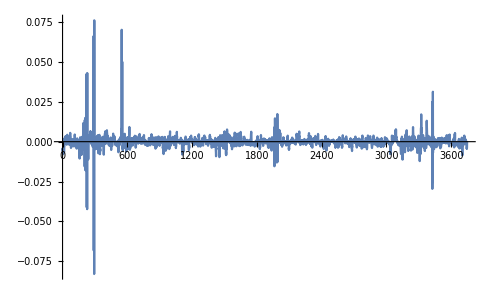

```mathematica
ListLinePlot[rsWethDai, PlotRange->All]
```

```mathematica
edistWethDai = EstimatedDistribution[rsWethDai, StableDistribution[1, a, b, loc, scale]]
```

StableDistribution[1,1.60712,-0.108702,-0.000176324,0.00134358]

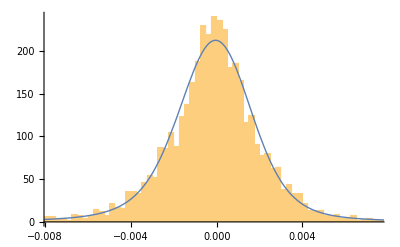

```mathematica
Show[Histogram[rsWethDai, {0.00025}, "PDF"], Plot[PDF[edistWethDai, x], {x, Min[rsWethDai], Max[rsWethDai]}, PlotRange->All, PlotStyle->Thick]]
```

```mathematica
(* 10 min periods ... *)
```

```mathematica
period = 600
```

600

```mathematica
aWethDai = 1.6071199346185128
```

1.60712

```mathematica
bWethDai = -0.10870229617829233
```

-0.108702

```mathematica
locWethDai = -0.00017632373873260288
```

-0.000176324

```mathematica
scaleWethDai = 0.0013435809449464948
```

0.00134358

```mathematica
μWethDai = locWethDai / period
```

-2.93873×10^-7

```mathematica
σWethDai = scaleWethDai / (period/aWethDai)^(1/aWethDai)
```

0.0000337149

```mathematica
(* Now repeat for more volatile pair like ALCX/WETH ... *)
```

```mathematica
tblAlcxWeth = Import["data-1624665179_alcx_weth-twap.csv"]
```

{{,timestamp,twap},{0,1.62208×10^9,3.29724×10^17},{1,1.62208×10^9,3.29397×10^17},{2,1.62208×10^9,3.29296×10^17},{3,1.62208×10^9,3.29306×10^17},{4,1.62208×10^9,3.29321×10^17},3607,{3612,1.62466×10^9,1.60227×10^17},{3613,1.62466×10^9,1.60103×10^17},{3614,1.62466×10^9,1.60128×10^17},{3615,1.62466×10^9,1.60188×10^17},{3616,1.62466×10^9,1.60262×10^17},{3617,1.62466×10^9,1.60305×10^17}}
 |  |  |  |

```mathematica
twapsAlcxWeth = Table[tblAlcxWeth[[i]][[3]], {i, 2, Length[tblAlcxWeth]}]
```

{3.29724×10^17,3.29397×10^17,3.29296×10^17,3.29306×10^17,3.29321×10^17,3.29328×10^17,3.29276×10^17,3.2927×10^17,3.29263×10^17,3.05701×10^17,3.29249×10^17,3.29311×10^17,3.294×10^17,3.29485×10^17,3.64188×10^17,3.29676×10^17,3.2985×10^17,3.29934×10^17,3.29994×10^17,3.30077×10^17,3.30124×10^17,3.30072×10^17,3.30002×10^17,3.2997×10^17,3.29917×10^17,3.29855×10^17,3.29817×10^17,3.29778×10^17,3.29675×10^17,3.29581×10^17,3.29529×10^17,3.29447×10^17,3.2941×10^17,3.29392×10^17,3.29367×10^17,3.29338×10^17,3.29332×10^17,3.29325×10^17,3.29326×10^17,3.29343×10^17,3.29362×10^17,3.29372×10^17,3.29391×10^17,3.29404×10^17,3.29416×10^17,3.29421×10^17,3.29453×10^17,3.29477×10^17,3.29511×10^17,3.29512×10^17,3.29474×10^17,3.29398×10^17,3.29357×10^17,3.29168×10^17,3.29106×10^17,3.29038×10^17,3.28917×10^17,3.28888×10^17,3.28736×10^17,3.28686×10^17,3.28659×10^17,3.2876×10^17,3.288×10^17,3.29069×10^17,3.29146×10^17,3.29239×10^17,3.29257×10^17,3.29243×10^17,3.2918×10^17,3.29168×10^17,3.29191×10^17,3.29232×10^17,3.2925×10^17,3.29236×10^17,3.29229×10^17,3.29216×10^17,3.29177×10^17,3.29154×10^17,3.293×10^17,3.30914×10^17,3.3256×10^17,3.34228×10^17,3.34865×10^17,3.36754×10^17,3.36952×10^17,3.36926×10^17,3.36974×10^17,3.36994×10^17,3.37009×10^17,3.37023×10^17,3.36996×10^17,3.36962×10^17,3.36927×10^17,3.36864×10^17,3.36849×10^17,3.36804×10^17,3.36795×10^17,3.36815×10^17,3.36841×10^17,3.36841×10^17,3.36838×10^17,3.36828×10^17,3.36811×10^17,3.36751×10^17,3.36715×10^17,3.36649×10^17,3.36555×10^17,3.36524×10^17,3.36468×10^17,3.36462×10^17,3.36358×10^17,3.36047×10^17,3.35894×10^17,3.35696×10^17,3.35576×10^17,3.35567×10^17,3.35566×10^17,3.35559×10^17,3.35556×10^17,3.3551×10^17,3.35485×10^17,3.35441×10^17,3.35408×10^17,3.35357×10^17,3.35371×10^17,3.3539×10^17,3.3542×10^17,3.35422×10^17,3.35412×10^17,3.35362×10^17,3.35293×10^17,3.34999×10^17,3.32699×10^17,3.31294×10^17,3.29803×10^17,3.2832×10^17,3.28231×10^17,3.28096×10^17,3.27962×10^17,3.27883×10^17,3.27733×10^17,3.27662×10^17,3.27603×10^17,3.27584×10^17,3.2757×10^17,3.27531×10^17,3.27485×10^17,3.27397×10^17,3.27344×10^17,3.27311×10^17,3.27291×10^17,3.27254×10^17,3.27066×10^17,3.26851×10^17,3.26298×10^17,3.25626×10^17,3.25202×10^17,3.24124×10^17,3.23603×10^17,3.23368×10^17,3.23388×10^17,3.23419×10^17,3.23399×10^17,3.23374×10^17,3.23367×10^17,3.23339×10^17,3.23214×10^17,3.23086×10^17,3.23026×10^17,3.22894×10^17,3.22726×10^17,3.22562×10^17,3.2224×10^17,3.22049×10^17,3.21768×10^17,3.21667×10^17,3.21455×10^17,3.21292×10^17,3.2136×10^17,3.21356×10^17,3.21353×10^17,3.21065×10^17,3.20846×10^17,3.20532×10^17,3.20419×10^17,3.20193×10^17,3.20301×10^17,3.20397×10^17,3.20507×10^17,3.20599×10^17,3.20606×10^17,3.20617×10^17,3.20633×10^17,3.20661×10^17,3.2067×10^17,3.2063×10^17,3.20585×10^17,3.20581×10^17,3.20556×10^17,3.20542×10^17,3.20562×10^17,3.20617×10^17,3.52054×10^17,3.20544×10^17,3.20534×10^17,3.2053×10^17,3.20486×10^17,2.84186×10^17,3.20605×10^17,3.20619×10^17,3.20638×10^17,3.20634×10^17,3.20633×10^17,3.20623×10^17,3.2061×10^17,3.20622×10^17,3.20635×10^17,3.20624×10^17,3.20626×10^17,3.20643×10^17,3.20625×10^17,3.20596×10^17,3.20577×10^17,3.20538×10^17,3.20363×10^17,3.20176×10^17,3.19683×10^17,3.19496×10^17,3.18959×10^17,3.18641×10^17,3.18016×10^17,3.16909×10^17,3.16428×10^17,3.15339×10^17,3.14861×10^17,3.14446×10^17,3.14375×10^17,3.14467×10^17,3.14634×10^17,3.147×10^17,3.14986×10^17,3.1517×10^17,3.15234×10^17,3.15235×10^17,3.15214×10^17,3.15199×10^17,3.15192×10^17,3.15251×10^17,3.15191×10^17,3.15171×10^17,3.15063×10^17,3.14967×10^17,3.14768×10^17,3.14651×10^17,3.14579×10^17,3.14399×10^17,3.14306×10^17,3.14154×10^17,3.1413×10^17,3.14106×10^17,3.14051×10^17,3.14027×10^17,3.14045×10^17,3.14669×10^17,3.15522×10^17,3.16348×10^17,3.1718×10^17,3.18082×10^17,3.18088×10^17,3.18064×10^17,3.18037×10^17,3.1802×10^17,3.17963×10^17,3.17954×10^17,3.17954×10^17,3.17948×10^17,3.17944×10^17,3.17935×10^17,3.17856×10^17,3.17814×10^17,3.17779×10^17,3.17706×10^17,3.17648×10^17,3.17634×10^17,3.17661×10^17,3.1773×10^17,3.17839×10^17,3.17905×10^17,3.17972×10^17,3.17978×10^17,3.17983×10^17,3.18004×10^17,3.18046×10^17,3.18112×10^17,3.18138×10^17,3.18144×10^17,3.18194×10^17,3.18171×10^17,3.18139×10^17,3.18134×10^17,3.18116×10^17,3.17975×10^17,3.17843×10^17,3.17705×10^17,3.17622×10^17,3.17524×10^17,3.17516×10^17,3.17516×10^17,3.17482×10^17,3.17457×10^17,3.1744×10^17,3.17438×10^17,3.17431×10^17,3.17423×10^17,3.17378×10^17,3.17334×10^17,3.17303×10^17,3.17354×10^17,3.17383×10^17,3.17405×10^17,3.17409×10^17,3.17395×10^17,3.17346×10^17,3.17317×10^17,3.17306×10^17,3.1731×10^17,3.17314×10^17,3.17294×10^17,3.17253×10^17,3.17205×10^17,3.17203×10^17,3.17204×10^17,3.17195×10^17,3.17155×10^17,3.1709×10^17,3.16973×10^17,3.16893×10^17,3.16825×10^17,3.1676×10^17,3.16761×10^17,3.1679×10^17,3.16808×10^17,3.17252×10^17,3.17845×10^17,3.18291×10^17,3.18948×10^17,3.19502×10^17,3.19482×10^17,3.19433×10^17,3.19354×10^17,3.19295×10^17,3.19143×10^17,3.19036×10^17,3.18947×10^17,3.18784×10^17,3.18627×10^17,3.18553×10^17,3.1851×10^17,3.18484×10^17,3.18428×10^17,3.1835×10^17,3.18208×10^17,3.18145×10^17,3.18028×10^17,3.17962×10^17,3.17954×10^17,3.17966×10^17,3.18047×10^17,3.18116×10^17,3.18187×10^17,3.18231×10^17,3.18298×10^17,3.18267×10^17,3.18248×10^17,3.18231×10^17,3.18242×10^17,3.18287×10^17,3.1826×10^17,3.1825×10^17,3.1822×10^17,3.18178×10^17,3.18102×10^17,3.18105×10^17,3.18108×10^17,3.18137×10^17,3.18187×10^17,3.18265×10^17,3.18449×10^17,3.18536×10^17,3.18722×10^17,3.18833×10^17,3.18891×10^17,3.18929×10^17,3.18912×10^17,3.18825×10^17,3.18489×10^17,3.17798×10^17,3.16543×10^17,3.1609×10^17,3.1557×10^17,3.15346×10^17,3.1533×10^17,3.15297×10^17,3.15976×10^17,3.17367×10^17,3.18985×10^17,3.19945×10^17,3.20352×10^17,3.19989×10^17,3.19349×10^17,3.18053×10^17,3.17034×10^17,3.17078×10^17,3.17063×10^17,3.17064×10^17,3.17055×10^17,3.17051×10^17,3.17046×10^17,3.17035×10^17,3.17085×10^17,3.17095×10^17,3.17088×10^17,3.17045×10^17,3.17029×10^17,3.16965×10^17,3.16904×10^17,3.1689×10^17,3.16873×10^17,3.16874×10^17,3.16875×10^17,3.16884×10^17,3.1687×10^17,3.16853×10^17,3.16837×10^17,3.16818×10^17,3.16798×10^17,3.16775×10^17,3.16765×10^17,3.16761×10^17,3.16762×10^17,3.16744×10^17,3.16689×10^17,3.166×10^17,3.16511×10^17,3.1643×10^17,3.16251×10^17,3.16164×10^17,3.1603×10^17,3.15946×10^17,3.15878×10^17,3.15793×10^17,3.15755×10^17,3.15693×10^17,3.15654×10^17,3.15726×10^17,3.15854×10^17,3.15888×10^17,3.1588×10^17,3.159×10^17,3.15843×10^17,3.05361×10^17,3.15761×10^17,3.15747×10^17,3.15717×10^17,3.15731×10^17,3.29101×10^17,3.15702×10^17,3.15698×10^17,3.1569×10^17,3.15454×10^17,3.15212×10^17,3.14885×10^17,3.14667×10^17,3.14336×10^17,3.14133×10^17,3.14092×10^17,3.14043×10^17,3.14003×10^17,3.13953×10^17,3.13919×10^17,3.13913×10^17,3.13907×10^17,3.13899×10^17,3.13909×10^17,3.13918×10^17,3.13907×10^17,3.13852×10^17,3.13695×10^17,3.13588×10^17,3.13487×10^17,3.13434×10^17,3.13423×10^17,3.13389×10^17,3.13373×10^17,3.13352×10^17,3.13336×10^17,3.13325×10^17,3.13301×10^17,3.13194×10^17,3.13022×10^17,3.12789×10^17,3.12565×10^17,3.12283×10^17,3.1219×10^17,3.12232×10^17,3.12264×10^17,3.12344×10^17,3.1243×10^17,3.12481×10^17,3.12493×10^17,3.12497×10^17,3.12499×10^17,3.12502×10^17,3.12479×10^17,3.12433×10^17,3.12378×10^17,3.12331×10^17,3.08553×10^17,3.08482×10^17,3.08343×10^17,3.08208×10^17,3.081×10^17,3.02644×10^17,3.02648×10^17,3.02702×10^17,3.02854×10^17,3.0286×10^17,3.02751×10^17,3.02621×10^17,3.02337×10^17,3.02157×10^17,3.01966×10^17,3.01849×10^17,3.01823×10^17,3.01789×10^17,3.01745×10^17,3.01668×10^17,3.01606×10^17,3.01514×10^17,3.01418×10^17,3.0131×10^17,3.01287×10^17,3.01287×10^17,3.01129×10^17,3.00945×10^17,3.00576×10^17,3.00025×10^17,2.99784×10^17,2.9922×10^17,2.98959×10^17,2.98906×10^17,2.98886×10^17,2.98874×10^17,2.98803×10^17,2.98777×10^17,2.98723×10^17,2.98694×10^17,2.98631×10^17,2.9861×10^17,2.98587×10^17,2.98539×10^17,2.98519×10^17,2.98368×10^17,2.98329×10^17,2.9825×10^17,2.98167×10^17,2.9811×10^17,2.98096×10^17,2.98041×10^17,2.9801×10^17,2.98013×10^17,2.98022×10^17,2.98026×10^17,2.98055×10^17,2.98082×10^17,2.98098×10^17,2.98114×10^17,2.98145×10^17,2.98128×10^17,2.97997×10^17,2.97877×10^17,2.97822×10^17,2.97646×10^17,2.97603×10^17,2.97612×10^17,2.97603×10^17,2.97584×10^17,2.97512×10^17,2.97479×10^17,2.97423×10^17,2.97369×10^17,2.97385×10^17,2.97365×10^17,2.9737×10^17,2.9739×10^17,2.97393×10^17,2.97352×10^17,2.97279×10^17,2.97211×10^17,2.97151×10^17,2.97151×10^17,2.97092×10^17,2.97115×10^17,2.97137×10^17,2.97144×10^17,2.97107×10^17,2.97114×10^17,2.97169×10^17,2.97335×10^17,2.97461×10^17,2.97625×10^17,2.97749×10^17,2.97823×10^17,2.97816×10^17,2.97803×10^17,2.97796×10^17,2.97794×10^17,2.97792×10^17,2.97794×10^17,2.97798×10^17,2.97797×10^17,2.97813×10^17,2.97877×10^17,2.97942×10^17,2.9797×10^17,2.98087×10^17,2.9817×10^17,2.98193×10^17,2.98273×10^17,2.98428×10^17,2.98595×10^17,2.98773×10^17,2.98947×10^17,2.99163×10^17,2.9926×10^17,2.9929×10^17,2.99288×10^17,2.99184×10^17,2.99143×10^17,2.99107×10^17,2.99147×10^17,2.989×10^17,2.98582×10^17,2.98405×10^17,2.97879×10^17,2.97043×10^17,2.96802×10^17,2.96571×10^17,2.96415×10^17,2.96395×10^17,2.96351×10^17,2.96334×10^17,2.96072×10^17,2.95612×10^17,2.95334×10^17,2.95399×10^17,2.95442×10^17,2.95682×10^17,2.95997×10^17,2.96206×10^17,2.96219×10^17,2.96223×10^17,2.96214×10^17,2.96192×10^17,2.96179×10^17,2.96144×10^17,2.95983×10^17,2.95873×10^17,2.95714×10^17,2.95508×10^17,2.95337×10^17,2.95303×10^17,2.95271×10^17,2.95239×10^17,2.95227×10^17,2.95144×10^17,2.95058×10^17,2.95004×10^17,2.94953×10^17,2.9492×10^17,2.94854×10^17,2.94868×10^17,2.9486×10^17,2.94848×10^17,2.94821×10^17,2.94785×10^17,2.94751×10^17,2.94705×10^17,2.94626×10^17,2.94541×10^17,2.94426×10^17,2.94349×10^17,2.94334×10^17,2.9434×10^17,2.94343×10^17,2.94251×10^17,2.94056×10^17,2.93761×10^17,2.93532×10^17,2.93322×10^17,2.93133×10^17,2.93125×10^17,2.931×10^17,2.93048×10^17,2.93023×10^17,2.92976×10^17,2.92951×10^17,2.92904×10^17,2.92841×10^17,2.92899×10^17,2.92938×10^17,2.92999×10^17,2.93177×10^17,2.93379×10^17,2.93438×10^17,2.93427×10^17,2.93419×10^17,2.93381×10^17,2.9338×10^17,2.9339×10^17,2.93412×10^17,2.93454×10^17,2.93507×10^17,2.93552×10^17,2.9359×10^17,2.93678×10^17,2.93709×10^17,2.93728×10^17,2.93738×10^17,2.9374×10^17,2.93665×10^17,2.9361×10^17,2.93492×10^17,2.9346×10^17,2.93585×10^17,2.93666×10^17,2.93711×10^17,2.93833×10^17,2.93878×10^17,2.93885×10^17,2.9392×10^17,2.9401×10^17,2.94169×10^17,2.94237×10^17,2.94262×10^17,2.94284×10^17,2.94293×10^17,2.94287×10^17,2.94279×10^17,2.94135×10^17,2.9405×10^17,2.93948×10^17,2.93818×10^17,2.9368×10^17,2.93605×10^17,2.93599×10^17,2.93549×10^17,2.93479×10^17,2.93361×10^17,2.93283×10^17,2.93151×10^17,2.93018×10^17,2.92904×10^17,2.92727×10^17,2.92512×10^17,2.92166×10^17,2.91822×10^17,2.91354×10^17,2.91023×10^17,2.90833×10^17,2.90796×10^17,2.90733×10^17,2.90659×10^17,2.90582×10^17,2.90547×10^17,2.90566×10^17,2.90602×10^17,2.90699×10^17,2.9072×10^17,2.90764×10^17,2.90756×10^17,2.90747×10^17,2.90771×10^17,2.90786×10^17,2.90836×10^17,2.90885×10^17,2.90906×10^17,2.90864×10^17,2.90851×10^17,2.90816×10^17,2.90716×10^17,2.90672×10^17,2.90635×10^17,2.90638×10^17,2.90637×10^17,2.90674×10^17,2.90694×10^17,2.906×10^17,2.9047×10^17,2.90374×10^17,2.90218×10^17,2.90124×10^17,2.90135×10^17,2.9012×10^17,2.90107×10^17,2.90046×10^17,2.90019×10^17,2.89999×10^17,2.89983×10^17,2.89934×10^17,2.89961×10^17,2.90037×10^17,2.90127×10^17,2.90176×10^17,2.90292×10^17,2.90296×10^17,2.903×10^17,2.90301×10^17,2.90313×10^17,2.903×10^17,2.90289×10^17,2.9027×10^17,2.90259×10^17,2.90248×10^17,2.9024×10^17,2.90242×10^17,2.90248×10^17,2.90252×10^17,2.90203×10^17,2.90181×10^17,2.90126×10^17,2.90058×10^17,2.89998×10^17,2.89934×10^17,2.89901×10^17,2.89887×10^17,2.8989×10^17,2.89938×10^17,2.89973×10^17,2.90026×10^17,2.90079×10^17,2.90098×10^17,2.90104×10^17,2.90129×10^17,2.90116×10^17,2.90102×10^17,2.90404×10^17,2.90775×10^17,2.91248×10^17,2.91783×10^17,2.92285×10^17,2.9357×10^17,2.94101×10^17,2.94671×10^17,2.95278×10^17,2.9566×10^17,2.96178×10^17,2.96569×10^17,2.97144×10^17,2.97508×10^17,2.977×10^17,2.97786×10^17,2.98116×10^17,2.98313×10^17,2.98598×10^17,2.98665×10^17,2.98726×10^17,2.98749×10^17,2.98795×10^17,2.98848×10^17,2.99132×10^17,2.994×10^17,2.9962×10^17,2.99849×10^17,3.042×10^17,3.00233×10^17,3.00453×10^17,3.00747×10^17,3.01045×10^17,2.96248×10^17,3.01939×10^17,3.02107×10^17,3.02185×10^17,3.02219×10^17,3.02813×10^17,3.02174×10^17,3.02071×10^17,3.02003×10^17,3.01873×10^17,3.01689×10^17,3.01564×10^17,3.01439×10^17,3.00892×10^17,3.00142×10^17,2.99374×10^17,2.98566×10^17,2.97656×10^17,2.96914×10^17,2.96789×10^17,2.96442×10^17,2.96282×10^17,2.96149×10^17,2.96203×10^17,2.9662×10^17,2.97156×10^17,2.9749×10^17,2.97803×10^17,2.97587×10^17,2.96464×10^17,2.95396×10^17,2.93947×10^17,2.93182×10^17,2.91809×10^17,2.91394×10^17,2.91179×10^17,2.90916×10^17,2.909×10^17,2.90779×10^17,2.90573×10^17,2.90176×10^17,2.89815×10^17,2.89564×10^17,2.89242×10^17,2.89084×10^17,2.89044×10^17,2.8903×10^17,2.89019×10^17,2.88984×10^17,2.88999×10^17,2.89022×10^17,2.89061×10^17,2.8911×10^17,2.8915×10^17,2.89179×10^17,2.89192×10^17,2.89193×10^17,2.89192×10^17,2.89191×10^17,2.89196×10^17,2.89195×10^17,2.89134×10^17,2.88905×10^17,2.88773×10^17,2.88563×10^17,2.88367×10^17,2.88278×10^17,2.99115×10^17,2.88325×10^17,2.88365×10^17,2.88397×10^17,2.88119×10^17,2.76869×10^17,2.8749×10^17,2.87204×10^17,2.86825×10^17,2.86621×10^17,2.86432×10^17,2.86297×10^17,2.86178×10^17,2.86132×10^17,2.86039×10^17,2.86082×10^17,2.86096×10^17,2.86007×10^17,2.85884×10^17,2.85788×10^17,2.85589×10^17,2.8546×10^17,2.85416×10^17,2.85312×10^17,2.85227×10^17,2.85355×10^17,2.86475×10^17,2.87675×10^17,2.88674×10^17,2.89623×10^17,2.91241×10^17,2.91269×10^17,2.91272×10^17,2.91241×10^17,2.91219×10^17,2.91191×10^17,2.91182×10^17,2.91135×10^17,2.9111×10^17,2.91053×10^17,2.90918×10^17,2.90826×10^17,2.90594×10^17,2.90541×10^17,2.90369×10^17,2.9031×10^17,2.90288×10^17,2.90238×10^17,2.90222×10^17,2.9019×10^17,2.90175×10^17,2.90176×10^17,2.90176×10^17,2.90176×10^17,2.90178×10^17,2.9011×10^17,2.90025×10^17,2.89921×10^17,2.89844×10^17,2.89766×10^17,2.89865×10^17,2.89994×10^17,2.90166×10^17,2.9031×10^17,2.90407×10^17,2.90525×10^17,2.9059×10^17,2.90741×10^17,2.90838×10^17,2.90839×10^17,2.90832×10^17,2.90812×10^17,2.90797×10^17,2.9076×10^17,2.90755×10^17,2.90781×10^17,2.90868×10^17,2.90899×10^17,2.90974×10^17,2.90985×10^17,2.90977×10^17,2.90944×10^17,2.90964×10^17,2.91027×10^17,2.91073×10^17,2.91132×10^17,2.91177×10^17,2.9119×10^17,2.91149×10^17,2.91125×10^17,2.91103×10^17,2.91099×10^17,2.91099×10^17,2.91105×10^17,2.91103×10^17,2.9108×10^17,2.91032×10^17,2.90972×10^17,2.9089×10^17,2.90822×10^17,2.90741×10^17,2.90664×10^17,2.90638×10^17,2.90578×10^17,2.90505×10^17,2.90437×10^17,2.90371×10^17,2.90351×10^17,2.90306×10^17,2.90244×10^17,2.9013×10^17,2.90084×10^17,2.9002×10^17,2.89914×10^17,2.89904×10^17,2.8986×10^17,2.89818×10^17,2.89781×10^17,2.89738×10^17,2.89762×10^17,2.89752×10^17,2.89743×10^17,2.89694×10^17,2.89674×10^17,2.89614×10^17,2.89598×10^17,2.89571×10^17,2.89547×10^17,2.89521×10^17,2.89534×10^17,2.89554×10^17,2.89603×10^17,2.8965×10^17,2.89698×10^17,2.89703×10^17,2.89693×10^17,2.89667×10^17,2.89643×10^17,2.89616×10^17,2.89603×10^17,2.89605×10^17,2.89616×10^17,2.8964×10^17,2.89656×10^17,2.89662×10^17,2.89667×10^17,2.89667×10^17,2.8966×10^17,2.89627×10^17,2.89573×10^17,2.89506×10^17,2.89475×10^17,2.89423×10^17,2.89464×10^17,2.89497×10^17,2.89545×10^17,2.89612×10^17,2.89632×10^17,2.89638×10^17,2.89639×10^17,2.8959×10^17,2.89551×10^17,2.89421×10^17,2.89344×10^17,2.89294×10^17,2.89255×10^17,2.89246×10^17,2.89245×10^17,2.89242×10^17,2.89217×10^17,2.89161×10^17,2.89107×10^17,2.8908×10^17,2.89044×10^17,2.8904×10^17,2.89071×10^17,2.891×10^17,2.89117×10^17,2.89123×10^17,2.88683×10^17,2.88299×10^17,2.86971×10^17,2.84636×10^17,2.83718×10^17,2.82895×10^17,2.82764×10^17,2.82528×10^17,2.82499×10^17,2.82453×10^17,2.82422×10^17,2.82417×10^17,2.82408×10^17,2.82406×10^17,2.82354×10^17,2.8233×10^17,2.82288×10^17,2.82215×10^17,2.82111×10^17,2.81968×10^17,2.81906×10^17,2.81859×10^17,2.81814×10^17,2.81739×10^17,2.8161×10^17,2.81459×10^17,2.81317×10^17,2.8121×10^17,2.8113×10^17,2.81141×10^17,2.81343×10^17,2.81437×10^17,2.81491×10^17,2.81529×10^17,2.81534×10^17,2.81509×10^17,2.81485×10^17,2.814×10^17,2.81368×10^17,2.81166×10^17,2.81031×10^17,2.80823×10^17,2.80661×10^17,2.80608×10^17,2.80449×10^17,2.80311×10^17,2.80294×10^17,2.80278×10^17,2.80253×10^17,2.80147×10^17,2.79922×10^17,2.79688×10^17,2.79556×10^17,2.79381×10^17,2.79368×10^17,2.79149×10^17,2.78753×10^17,2.7847×10^17,2.78117×10^17,2.7756×10^17,2.77557×10^17,2.77371×10^17,2.77121×10^17,2.76854×10^17,2.76583×10^17,2.76196×10^17,2.7625×10^17,2.76382×10^17,2.76459×10^17,2.767×10^17,2.7678×10^17,2.76788×10^17,2.76795×10^17,2.76792×10^17,2.76801×10^17,2.76762×10^17,2.76678×10^17,2.76612×10^17,2.76493×10^17,2.76392×10^17,2.76302×10^17,2.7629×10^17,2.76321×10^17,2.76457×10^17,2.76581×10^17,2.76719×10^17,2.76821×10^17,2.76837×10^17,2.76875×10^17,2.77017×10^17,2.77096×10^17,2.77181×10^17,2.77251×10^17,2.77405×10^17,2.77427×10^17,2.77456×10^17,2.77514×10^17,2.77557×10^17,2.77525×10^17,2.77524×10^17,2.77389×10^17,2.77252×10^17,2.77169×10^17,2.77104×10^17,2.77102×10^17,2.771×10^17,2.77158×10^17,2.77248×10^17,2.77284×10^17,2.77454×10^17,2.77566×10^17,2.77613×10^17,2.7766×10^17,2.77707×10^17,2.77881×10^17,2.78059×10^17,2.78171×10^17,2.78039×10^17,2.77904×10^17,2.77667×10^17,2.77499×10^17,2.77407×10^17,2.77418×10^17,2.77444×10^17,2.77463×10^17,2.77469×10^17,2.77473×10^17,2.77467×10^17,2.77418×10^17,2.77373×10^17,2.77362×10^17,2.77363×10^17,2.77349×10^17,2.77392×10^17,2.77438×10^17,2.77872×10^17,2.79244×10^17,2.80187×10^17,2.81282×10^17,2.82158×10^17,2.82743×10^17,2.82752×10^17,2.82801×10^17,2.82874×10^17,2.83032×10^17,2.83128×10^17,2.83215×10^17,2.83268×10^17,2.83262×10^17,2.8322×10^17,2.83226×10^17,2.83159×10^17,2.83099×10^17,2.83011×10^17,2.82931×10^17,2.82902×10^17,2.8283×10^17,2.82832×10^17,2.82835×10^17,2.82832×10^17,2.828×10^17,2.82773×10^17,2.82747×10^17,2.82735×10^17,2.82708×10^17,2.82709×10^17,2.82913×10^17,2.83009×10^17,2.83538×10^17,2.83744×10^17,2.84212×10^17,2.84355×10^17,2.84312×10^17,2.8428×10^17,2.84272×10^17,2.84248×10^17,2.84215×10^17,2.84211×10^17,2.8418×10^17,2.84119×10^17,2.84079×10^17,2.8407×10^17,2.84068×10^17,2.84047×10^17,2.84036×10^17,2.84049×10^17,2.8405×10^17,2.84096×10^17,2.84166×10^17,2.84253×10^17,2.84277×10^17,2.84288×10^17,2.84241×10^17,2.84115×10^17,2.83948×10^17,2.83914×10^17,2.84001×10^17,2.84165×10^17,2.84398×10^17,2.84697×10^17,2.85064×10^17,2.85558×10^17,2.86017×10^17,2.86434×10^17,2.86871×10^17,2.87074×10^17,2.87103×10^17,2.87107×10^17,2.87184×10^17,2.87312×10^17,2.87432×10^17,2.87533×10^17,2.8736×10^17,2.87221×10^17,2.87036×10^17,2.86869×10^17,2.86769×10^17,2.86726×10^17,2.86078×10^17,2.85043×10^17,2.84097×10^17,2.83281×10^17,2.81757×10^17,2.81439×10^17,2.81516×10^17,2.8155×10^17,2.81608×10^17,2.81718×10^17,2.81613×10^17,2.81396×10^17,2.81215×10^17,2.80987×10^17,2.80752×10^17,2.80689×10^17,2.80408×10^17,2.79309×10^17,2.78108×10^17,2.76727×10^17,2.75494×10^17,2.743×10^17,2.74107×10^17,2.73971×10^17,2.73937×10^17,2.73927×10^17,2.73929×10^17,2.73844×10^17,2.73502×10^17,2.73149×10^17,2.72898×10^17,2.72412×10^17,2.72786×10^17,2.7335×10^17,2.74114×10^17,2.74609×10^17,2.75622×10^17,2.75742×10^17,2.75691×10^17,2.75572×10^17,2.75491×10^17,2.75387×10^17,2.75235×10^17,2.747×10^17,2.74042×10^17,2.73581×10^17,2.72931×10^17,2.72293×10^17,2.723×10^17,2.72285×10^17,2.7223×10^17,2.72188×10^17,2.7215×10^17,2.72094×10^17,2.7208×10^17,2.72754×10^17,2.73944×10^17,2.76318×10^17,2.78956×10^17,2.81546×10^17,2.83509×10^17,2.84867×10^17,2.8495×10^17,2.8494×10^17,2.84878×10^17,2.8493×10^17,2.84974×10^17,2.85041×10^17,2.85129×10^17,2.85298×10^17,2.85347×10^17,2.85409×10^17,2.85428×10^17,2.8542×10^17,2.85018×10^17,2.84482×10^17,2.83912×10^17,2.8338×10^17,2.82824×10^17,2.82681×10^17,2.82676×10^17,2.8267×10^17,2.82645×10^17,2.82592×10^17,2.82517×10^17,2.82348×10^17,2.81152×10^17,2.79962×10^17,2.78066×10^17,2.76518×10^17,2.75295×10^17,2.75112×10^17,2.75126×10^17,2.75135×10^17,2.75028×10^17,2.74887×10^17,2.7486×10^17,2.74985×10^17,2.75239×10^17,2.75615×10^17,2.76143×10^17,2.76348×10^17,2.76473×10^17,2.76565×10^17,2.76688×10^17,2.76711×10^17,2.76619×10^17,2.76477×10^17,2.76299×10^17,2.76037×10^17,2.75893×10^17,2.75807×10^17,2.7578×10^17,2.75794×10^17,2.7589×10^17,2.76007×10^17,2.76162×10^17,2.76285×10^17,2.76366×10^17,2.76424×10^17,2.76424×10^17,2.76426×10^17,2.76438×10^17,2.76469×10^17,2.76545×10^17,2.76635×10^17,2.76711×10^17,2.76848×10^17,2.76943×10^17,2.7713×10^17,2.77243×10^17,2.77383×10^17,2.77472×10^17,2.77529×10^17,2.77579×10^17,2.7756×10^17,2.77489×10^17,2.77448×10^17,2.7742×10^17,2.77356×10^17,2.77345×10^17,2.77372×10^17,2.77391×10^17,2.77422×10^17,2.77457×10^17,2.77469×10^17,2.77489×10^17,2.77489×10^17,2.77451×10^17,2.77394×10^17,2.77519×10^17,2.77638×10^17,2.77768×10^17,2.77929×10^17,2.78046×10^17,2.77985×10^17,2.77923×10^17,2.77864×10^17,2.77816×10^17,2.77827×10^17,2.77821×10^17,2.7779×10^17,2.77764×10^17,2.77733×10^17,2.77678×10^17,2.77653×10^17,2.77631×10^17,2.77617×10^17,2.7758×10^17,2.77552×10^17,2.77511×10^17,2.77512×10^17,2.77592×10^17,2.77719×10^17,2.77808×10^17,2.77939×10^17,2.78183×10^17,2.78298×10^17,2.78443×10^17,2.78576×10^17,2.78796×10^17,2.78822×10^17,2.78826×10^17,2.78792×10^17,2.78715×10^17,2.78576×10^17,2.78526×10^17,2.78482×10^17,2.78442×10^17,2.78473×10^17,2.7855×10^17,2.78594×10^17,2.7869×10^17,2.78742×10^17,2.78814×10^17,2.78802×10^17,2.78798×10^17,2.78805×10^17,2.78815×10^17,2.78818×10^17,2.7883×10^17,2.78848×10^17,2.7886×10^17,2.7897×10^17,2.79058×10^17,2.79169×10^17,2.79273×10^17,2.79301×10^17,2.79351×10^17,2.7938×10^17,2.79387×10^17,2.7939×10^17,2.79428×10^17,2.79362×10^17,2.79213×10^17,2.79027×10^17,2.78898×10^17,2.7855×10^17,2.78401×10^17,2.7836×10^17,2.78375×10^17,2.78393×10^17,2.78411×10^17,2.78351×10^17,2.78282×10^17,2.78213×10^17,2.78157×10^17,2.78125×10^17,2.78143×10^17,2.78349×10^17,2.78512×10^17,2.78648×10^17,2.78794×10^17,2.78929×10^17,2.78897×10^17,2.78848×10^17,2.78847×10^17,2.78852×10^17,2.78886×10^17,2.78931×10^17,2.79023×10^17,2.79077×10^17,2.79172×10^17,2.79313×10^17,2.79394×10^17,2.79637×10^17,2.79797×10^17,2.79898×10^17,2.79906×10^17,2.79873×10^17,2.79841×10^17,2.79783×10^17,2.79764×10^17,2.79739×10^17,2.79745×10^17,2.79747×10^17,2.79749×10^17,2.79731×10^17,2.79715×10^17,2.79697×10^17,2.79692×10^17,2.79671×10^17,2.79647×10^17,2.7963×10^17,2.79608×10^17,2.79599×10^17,2.79642×10^17,2.79849×10^17,2.79958×10^17,2.80209×10^17,2.80393×10^17,2.80458×10^17,2.80566×10^17,2.80597×10^17,2.80631×10^17,2.80642×10^17,2.80666×10^17,2.80687×10^17,2.80666×10^17,2.80657×10^17,2.80729×10^17,2.80787×10^17,2.80876×10^17,2.81006×10^17,2.81158×10^17,2.81256×10^17,2.813×10^17,2.81369×10^17,2.81371×10^17,2.81301×10^17,2.8123×10^17,2.8116×10^17,2.81086×10^17,2.80987×10^17,2.80954×10^17,2.80962×10^17,2.80966×10^17,2.80953×10^17,2.80944×10^17,2.80915×10^17,2.80863×10^17,2.80816×10^17,2.80794×10^17,2.80772×10^17,2.80812×10^17,2.80876×10^17,2.80937×10^17,2.81016×10^17,2.81085×10^17,2.8115×10^17,2.81188×10^17,2.81208×10^17,2.81204×10^17,2.81236×10^17,3.11863×10^17,2.81275×10^17,2.81335×10^17,2.81402×10^17,2.81621×10^17,2.55202×10^17,2.81933×10^17,2.8208×10^17,2.82673×10^17,2.83305×10^17,2.84119×10^17,2.84922×10^17,2.85644×10^17,2.8595×10^17,2.8624×10^17,2.86479×10^17,2.87077×10^17,2.8786×10^17,2.88392×10^17,2.88851×10^17,2.89345×10^17,2.89425×10^17,2.89495×10^17,2.8951×10^17,2.89504×10^17,2.89524×10^17,2.89539×10^17,2.89546×10^17,2.8962×10^17,2.91274×10^17,2.92782×10^17,2.94194×10^17,2.95922×10^17,2.97242×10^17,2.97394×10^17,2.97662×10^17,2.97894×10^17,2.98055×10^17,2.98147×10^17,2.9809×10^17,2.97911×10^17,2.97776×10^17,2.97704×10^17,2.97638×10^17,2.97769×10^17,2.97987×10^17,2.98041×10^17,2.98211×10^17,2.9832×10^17,2.98321×10^17,2.98257×10^17,2.98285×10^17,2.98335×10^17,2.98377×10^17,2.98388×10^17,2.98408×10^17,2.98444×10^17,2.98743×10^17,2.99075×10^17,2.99495×10^17,2.99811×10^17,3.00184×10^17,3.00316×10^17,3.00332×10^17,3.00352×10^17,3.00371×10^17,3.00424×10^17,3.00473×10^17,3.00504×10^17,3.00345×10^17,3.0013×10^17,2.99814×10^17,2.99535×10^17,2.9924×10^17,2.9915×10^17,2.99136×10^17,2.99153×10^17,2.99167×10^17,2.99174×10^17,2.9917×10^17,2.99181×10^17,2.99169×10^17,2.99183×10^17,2.992×10^17,2.99241×10^17,2.9921×10^17,2.9913×10^17,2.99068×10^17,2.99049×10^17,2.99054×10^17,2.99144×10^17,2.99285×10^17,2.99392×10^17,2.99452×10^17,2.99463×10^17,2.99417×10^17,2.99332×10^17,2.98338×10^17,2.97655×10^17,2.97391×10^17,2.96753×10^17,2.9648×10^17,2.96844×10^17,2.97004×10^17,2.97052×10^17,2.97025×10^17,2.97067×10^17,2.97071×10^17,2.97035×10^17,2.97017×10^17,2.97043×10^17,2.97123×10^17,2.97265×10^17,2.97433×10^17,2.97585×10^17,2.97683×10^17,2.97625×10^17,2.97525×10^17,2.9734×10^17,2.97191×10^17,2.97068×10^17,2.97167×10^17,2.97338×10^17,2.97659×10^17,2.97956×10^17,2.98248×10^17,2.98386×10^17,2.9845×10^17,2.98423×10^17,2.98408×10^17,2.98397×10^17,2.98392×10^17,2.98383×10^17,2.98372×10^17,2.98414×10^17,2.9852×10^17,2.98832×10^17,2.99036×10^17,2.99342×10^17,2.99646×10^17,2.99762×10^17,2.99764×10^17,2.99766×10^17,2.99772×10^17,2.99815×10^17,2.99859×10^17,2.99894×10^17,2.99514×10^17,2.99006×10^17,2.97169×10^17,2.95435×10^17,2.94093×10^17,2.92367×10^17,2.91082×10^17,2.91056×10^17,2.91239×10^17,2.91512×10^17,2.92584×10^17,2.93266×10^17,2.93822×10^17,2.94406×10^17,2.94397×10^17,2.94364×10^17,2.94387×10^17,2.94395×10^17,2.94416×10^17,2.94439×10^17,2.94462×10^17,2.94398×10^17,2.94348×10^17,2.9431×10^17,2.94232×10^17,2.94098×10^17,2.94114×10^17,2.94105×10^17,2.94088×10^17,2.94126×10^17,2.94166×10^17,2.94095×10^17,2.94065×10^17,2.94041×10^17,2.94004×10^17,2.94113×10^17,2.94193×10^17,2.9413×10^17,2.94113×10^17,2.94112×10^17,2.94001×10^17,2.93947×10^17,2.94107×10^17,2.94322×10^17,2.94494×10^17,2.94629×10^17,2.94739×10^17,2.94724×10^17,2.94607×10^17,2.94462×10^17,2.94204×10^17,2.93994×10^17,2.93676×10^17,2.93316×10^17,2.93122×10^17,2.93091×10^17,2.93086×10^17,2.7735×10^17,2.93006×10^17,2.92896×10^17,2.92822×10^17,2.92686×10^17,3.06798×10^17,2.89083×10^17,2.87163×10^17,2.86264×10^17,2.83316×10^17,2.82432×10^17,2.81507×10^17,2.79999×10^17,2.72707×10^17,2.75377×10^17,2.72719×10^17,2.70964×10^17,2.69295×10^17,2.74506×10^17,2.68929×10^17,2.6878×10^17,2.68643×10^17,2.68516×10^17,2.68328×10^17,2.68178×10^17,2.68082×10^17,2.67985×10^17,2.67948×10^17,2.67974×10^17,2.68001×10^17,2.6805×10^17,2.68098×10^17,2.68153×10^17,2.6815×10^17,2.6813×10^17,2.68111×10^17,2.68103×10^17,2.68106×10^17,2.68132×10^17,2.6816×10^17,2.68204×10^17,2.68342×10^17,2.68726×10^17,2.69205×10^17,2.69516×10^17,2.702×10^17,2.70618×10^17,2.70983×10^17,2.71771×10^17,2.72444×10^17,2.73021×10^17,2.73939×10^17,2.74528×10^17,2.74516×10^17,2.745×10^17,2.74508×10^17,2.74501×10^17,2.74508×10^17,2.74492×10^17,2.74443×10^17,2.74384×10^17,2.74332×10^17,2.743×10^17,2.74309×10^17,2.74333×10^17,2.74353×10^17,2.74385×10^17,2.74384×10^17,2.74402×10^17,2.74421×10^17,2.74442×10^17,2.74449×10^17,2.74452×10^17,2.74452×10^17,2.74466×10^17,2.7447×10^17,2.7451×10^17,2.74551×10^17,2.74581×10^17,2.74582×10^17,2.74599×10^17,2.74617×10^17,2.74642×10^17,2.74742×10^17,2.74874×10^17,2.74961×10^17,2.7501×10^17,2.75075×10^17,2.75051×10^17,2.75027×10^17,2.75012×10^17,2.74975×10^17,2.74948×10^17,2.74937×10^17,2.74923×10^17,2.74905×10^17,2.74922×10^17,2.74921×10^17,2.74927×10^17,2.74934×10^17,2.7497×10^17,2.75001×10^17,2.75055×10^17,2.75073×10^17,2.75122×10^17,2.7513×10^17,2.75097×10^17,2.75048×10^17,2.74962×10^17,2.74554×10^17,2.73957×10^17,2.73486×10^17,2.73042×10^17,2.72511×10^17,2.7254×10^17,2.72413×10^17,2.72283×10^17,2.72125×10^17,2.71903×10^17,2.7174×10^17,2.71793×10^17,2.72017×10^17,2.72196×10^17,2.72432×10^17,2.72704×10^17,2.72727×10^17,2.72767×10^17,2.72796×10^17,2.72812×10^17,2.72873×10^17,2.72898×10^17,2.72954×10^17,2.72975×10^17,2.72985×10^17,2.72956×10^17,2.72948×10^17,2.72942×10^17,2.72974×10^17,2.73014×10^17,2.7255×10^17,2.72056×10^17,2.71561×10^17,2.71041×10^17,2.70509×10^17,2.70304×10^17,2.70096×10^17,2.69903×10^17,2.69612×10^17,2.69331×10^17,2.6909×10^17,2.68749×10^17,2.68469×10^17,2.68217×10^17,2.67927×10^17,2.67747×10^17,2.67631×10^17,2.67486×10^17,2.67304×10^17,2.67112×10^17,2.66877×10^17,2.66702×10^17,2.66525×10^17,2.66359×10^17,2.6633×10^17,2.66302×10^17,2.66297×10^17,2.66264×10^17,2.66503×10^17,2.6675×10^17,2.6682×10^17,2.66856×10^17,2.66891×10^17,2.66642×10^17,2.66375×10^17,2.66269×10^17,2.66164×10^17,2.66107×10^17,2.6609×10^17,2.66077×10^17,2.66035×10^17,2.65979×10^17,2.65884×10^17,2.65786×10^17,2.65685×10^17,2.65599×10^17,2.6554×10^17,2.65497×10^17,2.65474×10^17,2.65471×10^17,2.65478×10^17,2.65484×10^17,2.65482×10^17,2.65486×10^17,2.65483×10^17,2.65487×10^17,2.6549×10^17,2.65502×10^17,2.6543×10^17,2.65459×10^17,2.65477×10^17,2.65459×10^17,2.65429×10^17,2.65472×10^17,2.65434×10^17,2.65377×10^17,2.65347×10^17,2.65263×10^17,2.65186×10^17,2.65146×10^17,2.65054×10^17,2.65013×10^17,2.64976×10^17,2.64922×10^17,2.64857×10^17,2.64769×10^17,2.64675×10^17,2.64582×10^17,2.64055×10^17,2.63504×10^17,2.62354×10^17,2.6099×10^17,2.59694×10^17,2.58639×10^17,2.5787×10^17,2.57446×10^17,2.57286×10^17,2.57051×10^17,2.56783×10^17,2.57051×10^17,2.57597×10^17,2.58277×10^17,2.59223×10^17,2.60142×10^17,2.60553×10^17,2.60848×10^17,2.60912×10^17,2.60944×10^17,2.60887×10^17,2.60849×10^17,2.60808×10^17,2.60799×10^17,2.60778×10^17,2.60734×10^17,2.60604×10^17,2.60467×10^17,2.60397×10^17,2.60248×10^17,2.60183×10^17,2.60203×10^17,2.6023×10^17,2.60173×10^17,2.60008×10^17,2.599×10^17,2.59785×10^17,2.59607×10^17,2.59515×10^17,2.59287×10^17,2.59142×10^17,2.59068×10^17,2.59037×10^17,2.59031×10^17,2.59088×10^17,2.59137×10^17,2.59111×10^17,2.59083×10^17,2.59202×10^17,2.59292×10^17,2.59401×10^17,2.59532×10^17,2.59634×10^17,2.59647×10^17,2.59669×10^17,2.59735×10^17,2.59797×10^17,2.59879×10^17,2.59917×10^17,2.59931×10^17,2.59951×10^17,2.60052×10^17,2.60168×10^17,2.60331×10^17,2.60467×10^17,2.6058×10^17,2.60705×10^17,2.60785×10^17,2.60873×10^17,2.60966×10^17,2.61025×10^17,2.61094×10^17,2.61109×10^17,2.61123×10^17,2.61134×10^17,2.61147×10^17,2.61266×10^17,2.61324×10^17,2.61357×10^17,2.61401×10^17,2.61394×10^17,2.61382×10^17,2.61385×10^17,2.614×10^17,2.61412×10^17,2.61418×10^17,2.61433×10^17,2.6139×10^17,2.61303×10^17,2.61243×10^17,2.6117×10^17,2.61104×10^17,2.61081×10^17,2.61051×10^17,2.61027×10^17,2.74984×10^17,2.60967×10^17,2.60921×10^17,2.6088×10^17,2.60847×10^17,2.49286×10^17,2.60747×10^17,2.60659×10^17,2.60649×10^17,2.60694×10^17,2.60758×10^17,2.60919×10^17,2.61083×10^17,2.6118×10^17,2.61202×10^17,2.61212×10^17,2.61236×10^17,2.61276×10^17,2.61319×10^17,2.61348×10^17,2.61383×10^17,2.61425×10^17,2.61467×10^17,2.61513×10^17,2.61536×10^17,2.61688×10^17,2.61845×10^17,2.61956×10^17,2.62056×10^17,2.62148×10^17,2.62133×10^17,2.62059×10^17,2.62024×10^17,2.62021×10^17,2.62033×10^17,2.62028×10^17,2.62024×10^17,2.62034×10^17,2.62033×10^17,2.6203×10^17,2.62023×10^17,2.62004×10^17,2.62016×10^17,2.62053×10^17,2.62123×10^17,2.62242×10^17,2.62553×10^17,2.6304×10^17,2.63393×10^17,2.63857×10^17,2.64218×10^17,2.6427×10^17,2.64315×10^17,2.64265×10^17,2.64186×10^17,2.64117×10^17,2.63697×10^17,2.63357×10^17,2.62785×10^17,2.62381×10^17,2.62101×10^17,2.62174×10^17,2.62234×10^17,2.62292×10^17,2.62323×10^17,2.62327×10^17,2.6227×10^17,2.62203×10^17,2.621×10^17,2.61936×10^17,2.61756×10^17,2.61633×10^17,2.6153×10^17,2.61379×10^17,2.61211×10^17,2.60988×10^17,2.60794×10^17,2.60705×10^17,2.60703×10^17,2.60819×10^17,2.60877×10^17,2.61022×10^17,2.61066×10^17,2.61153×10^17,2.61128×10^17,2.61021×10^17,2.60858×10^17,2.60629×10^17,2.60147×10^17,2.59693×10^17,2.592×10^17,2.58882×10^17,2.58611×10^17,2.58456×10^17,2.58425×10^17,2.58418×10^17,2.58411×10^17,2.58379×10^17,2.58347×10^17,2.5746×10^17,2.5641×10^17,2.55378×10^17,2.54202×10^17,2.53045×10^17,2.52793×10^17,2.528×10^17,2.52779×10^17,2.52762×10^17,2.52782×10^17,2.52824×10^17,2.52883×10^17,2.52958×10^17,2.53041×10^17,2.53082×10^17,2.531×10^17,2.53081×10^17,2.53067×10^17,2.53041×10^17,2.53008×10^17,2.52968×10^17,2.52939×10^17,2.52905×10^17,2.52858×10^17,2.52816×10^17,2.52787×10^17,2.52727×10^17,2.52656×10^17,2.52527×10^17,2.52419×10^17,2.52316×10^17,2.52118×10^17,2.52003×10^17,2.51979×10^17,2.51959×10^17,2.51928×10^17,2.51918×10^17,2.51894×10^17,2.51865×10^17,2.51852×10^17,2.51852×10^17,2.51847×10^17,2.51838×10^17,2.51803×10^17,2.51707×10^17,2.5159×10^17,2.52362×10^17,2.53532×10^17,2.54408×10^17,2.55765×10^17,2.56918×10^17,2.57015×10^17,2.57124×10^17,2.57114×10^17,2.57099×10^17,2.57104×10^17,2.57112×10^17,2.57108×10^17,2.57085×10^17,2.57049×10^17,2.56047×10^17,2.54785×10^17,2.53389×10^17,2.52187×10^17,2.50842×10^17,2.50663×10^17,2.50721×10^17,2.50728×10^17,2.51016×10^17,2.51686×10^17,2.52598×10^17,2.52346×10^17,2.52463×10^17,2.52299×10^17,2.51471×10^17,2.50311×10^17,2.50144×10^17,2.49968×10^17,2.49829×10^17,2.49822×10^17,2.49787×10^17,2.49749×10^17,2.49717×10^17,2.49633×10^17,2.49435×10^17,2.49131×10^17,2.48853×10^17,2.4847×10^17,2.48082×10^17,2.47916×10^17,2.4765×10^17,2.47302×10^17,2.47051×10^17,2.46714×10^17,2.46269×10^17,2.45309×10^17,2.43892×10^17,2.42576×10^17,2.40633×10^17,2.39511×10^17,2.3893×10^17,2.38917×10^17,2.39015×10^17,2.39255×10^17,2.39446×10^17,2.39635×10^17,2.39784×10^17,2.39869×10^17,2.39901×10^17,2.39958×10^17,2.40006×10^17,2.3989×10^17,2.39518×10^17,2.39232×10^17,2.38998×10^17,2.38619×10^17,2.38528×10^17,2.38563×10^17,2.38588×10^17,2.38603×10^17,2.38247×10^17,2.37638×10^17,2.37138×10^17,2.36563×10^17,2.36165×10^17,2.35766×10^17,2.35701×10^17,2.35653×10^17,2.35613×10^17,2.35589×10^17,2.35593×10^17,2.35602×10^17,2.35609×10^17,2.3561×10^17,2.35611×10^17,2.34545×10^17,2.33199×10^17,2.31794×10^17,2.3022×10^17,2.29956×10^17,2.28111×10^17,2.27935×10^17,2.2768×10^17,2.2752×10^17,2.2755×10^17,2.27551×10^17,2.27462×10^17,2.27229×10^17,2.26972×10^17,2.26482×10^17,2.25996×10^17,2.25496×10^17,2.24937×10^17,2.24474×10^17,2.24187×10^17,2.23904×10^17,2.23789×10^17,2.23647×10^17,2.2354×10^17,2.23265×10^17,2.22957×10^17,2.22596×10^17,2.22315×10^17,2.22101×10^17,2.21983×10^17,2.21826×10^17,2.21719×10^17,2.21561×10^17,2.21361×10^17,2.21097×10^17,2.2085×10^17,2.20623×10^17,2.20398×10^17,2.19835×10^17,2.18724×10^17,2.17399×10^17,2.16182×10^17,2.14177×10^17,2.12903×10^17,2.12321×10^17,2.11433×10^17,2.10557×10^17,2.10071×10^17,2.09545×10^17,2.09263×10^17,2.10806×10^17,2.12288×10^17,2.14944×10^17,2.1699×10^17,2.19461×10^17,2.20904×10^17,2.22024×10^17,2.23754×10^17,2.25635×10^17,2.27194×10^17,2.28794×10^17,2.30132×10^17,2.30242×10^17,2.30702×10^17,2.30959×10^17,2.31284×10^17,2.31665×10^17,2.32198×10^17,2.32×10^17,2.30461×10^17,2.28297×10^17,2.25975×10^17,2.24182×10^17,2.2157×10^17,2.19892×10^17,2.19866×10^17,2.19924×10^17,2.20049×10^17,2.20215×10^17,2.20261×10^17,2.20014×10^17,2.1969×10^17,2.18993×10^17,2.17562×10^17,2.1633×10^17,2.13826×10^17,2.11128×10^17,2.0762×10^17,2.0466×10^17,2.02275×10^17,2.01514×10^17,2.01438×10^17,2.01991×10^17,2.02661×10^17,2.0295×10^17,2.02951×10^17,2.0222×10^17,2.01045×10^17,1.98813×10^17,1.96424×10^17,1.94562×10^17,1.93634×10^17,1.93896×10^17,1.94406×10^17,1.94873×10^17,1.95514×10^17,1.95531×10^17,1.95489×10^17,1.95495×10^17,1.96761×10^17,1.98003×10^17,1.98438×10^17,1.98813×10^17,1.99012×10^17,1.97998×10^17,1.96884×10^17,1.96856×10^17,1.96343×10^17,1.96917×10^17,1.97727×10^17,1.98532×10^17,1.99691×10^17,2.01977×10^17,2.02994×10^17,2.03002×10^17,2.03035×10^17,2.03114×10^17,2.0317×10^17,2.03236×10^17,2.03256×10^17,2.03329×10^17,2.03391×10^17,2.03429×10^17,2.03501×10^17,2.03632×10^17,2.03699×10^17,2.03778×10^17,2.03862×10^17,2.03895×10^17,2.03879×10^17,2.03825×10^17,2.03718×10^17,2.03587×10^17,2.03431×10^17,2.03204×10^17,2.03027×10^17,2.0294×10^17,2.02929×10^17,2.03×10^17,2.03087×10^17,2.03111×10^17,2.01003×10^17,1.98581×10^17,1.95959×10^17,1.9317×10^17,1.90814×10^17,1.90636×10^17,1.90672×10^17,1.90813×10^17,1.90998×10^17,1.91174×10^17,1.91337×10^17,1.91472×10^17,1.91544×10^17,1.91532×10^17,1.91488×10^17,1.91478×10^17,1.9162×10^17,1.92035×10^17,1.92582×10^17,1.93415×10^17,1.93966×10^17,1.95359×10^17,1.96795×10^17,1.9772×10^17,1.99007×10^17,1.99937×10^17,2.00004×10^17,2.00014×10^17,1.99952×10^17,1.99823×10^17,1.99582×10^17,1.99381×10^17,1.99242×10^17,1.9907×10^17,1.98942×10^17,1.98881×10^17,1.98888×10^17,1.98896×10^17,1.98895×10^17,1.98928×10^17,1.99017×10^17,1.99152×10^17,1.99278×10^17,1.9946×10^17,1.99608×10^17,1.99708×10^17,1.99802×10^17,1.99925×10^17,2.00079×10^17,2.00173×10^17,2.00283×10^17,2.00379×10^17,2.00494×10^17,1.99787×10^17,1.99249×10^17,1.98602×10^17,1.97763×10^17,1.96766×10^17,1.9654×10^17,1.96355×10^17,1.96182×10^17,1.95977×10^17,1.959×10^17,1.95829×10^17,1.95833×10^17,1.95877×10^17,1.95919×10^17,1.95949×10^17,1.9598×10^17,1.96001×10^17,1.96043×10^17,1.96056×10^17,1.96069×10^17,1.96092×10^17,1.96078×10^17,1.97557×10^17,1.99957×10^17,2.01994×10^17,2.04308×10^17,2.06478×10^17,2.06884×10^17,2.06768×10^17,2.06751×10^17,2.06742×10^17,2.06731×10^17,2.06709×10^17,2.06552×10^17,2.06446×10^17,2.06356×10^17,2.06277×10^17,2.06285×10^17,2.06299×10^17,2.06304×10^17,2.06302×10^17,2.06299×10^17,2.06295×10^17,2.06299×10^17,2.06337×10^17,2.06377×10^17,2.06389×10^17,2.06441×10^17,2.06474×10^17,2.06458×10^17,2.06433×10^17,2.06398×10^17,2.06331×10^17,2.06284×10^17,2.06235×10^17,2.06206×10^17,2.06154×10^17,2.06138×10^17,2.06099×10^17,2.06066×10^17,2.06039×10^17,2.06031×10^17,2.05988×10^17,2.05912×10^17,2.05772×10^17,2.05704×10^17,2.05639×10^17,2.0561×10^17,2.05619×10^17,2.05637×10^17,2.05619×10^17,2.05598×10^17,2.05584×10^17,2.05572×10^17,2.05567×10^17,2.05563×10^17,2.05555×10^17,2.0552×10^17,2.05443×10^17,2.05401×10^17,2.05291×10^17,2.05218×10^17,2.0518×10^17,2.05198×10^17,2.05218×10^17,2.05242×10^17,2.05258×10^17,2.05285×10^17,2.05286×10^17,2.05278×10^17,2.05234×10^17,2.05199×10^17,2.05147×10^17,2.05091×10^17,2.04611×10^17,2.03855×10^17,2.03271×10^17,2.02578×10^17,2.01699×10^17,2.01453×10^17,2.01368×10^17,2.01177×10^17,2.00858×10^17,2.00524×10^17,2.00129×10^17,1.9916×10^17,1.98042×10^17,1.96306×10^17,1.95491×10^17,1.93846×10^17,1.93428×10^17,1.93152×10^17,1.92863×10^17,1.92581×10^17,1.92094×10^17,1.91824×10^17,1.91703×10^17,1.91629×10^17,1.9151×10^17,1.91205×10^17,1.89942×10^17,1.88704×10^17,1.87313×10^17,1.85129×10^17,1.83726×10^17,1.8335×10^17,1.83299×10^17,1.83151×10^17,1.82965×10^17,1.82776×10^17,1.82553×10^17,1.82328×10^17,1.82205×10^17,1.8167×10^17,1.8149×10^17,1.81269×10^17,1.81074×10^17,1.80864×10^17,1.80859×10^17,1.80794×10^17,1.80245×10^17,1.79023×10^17,1.77972×10^17,1.77104×10^17,1.76176×10^17,1.76012×10^17,1.75948×10^17,1.75979×10^17,1.76002×10^17,1.76027×10^17,1.76087×10^17,1.76196×10^17,1.76326×10^17,1.76468×10^17,1.76636×10^17,1.76907×10^17,1.76966×10^17,1.76998×10^17,1.77032×10^17,1.77032×10^17,1.77039×10^17,1.77145×10^17,1.77463×10^17,1.77844×10^17,1.78059×10^17,1.7827×10^17,1.78506×10^17,1.7841×10^17,1.78248×10^17,1.78222×10^17,1.78144×10^17,1.78111×10^17,1.78077×10^17,1.78059×10^17,1.78051×10^17,1.78031×10^17,1.77975×10^17,1.77934×10^17,1.77903×10^17,1.77903×10^17,1.7792×10^17,1.77991×10^17,1.78055×10^17,1.7812×10^17,1.78169×10^17,1.78174×10^17,1.78157×10^17,1.7814×10^17,1.78115×10^17,1.78103×10^17,1.7805×10^17,1.77972×10^17,1.77921×10^17,1.77847×10^17,1.77798×10^17,1.77778×10^17,1.77767×10^17,1.77752×10^17,1.77711×10^17,1.77526×10^17,1.77398×10^17,1.77298×10^17,1.77144×10^17,1.77098×10^17,1.77115×10^17,1.77133×10^17,1.77126×10^17,1.77123×10^17,1.77101×10^17,1.7707×10^17,1.77024×10^17,1.76988×10^17,1.76951×10^17,1.76905×10^17,1.76586×10^17,1.75847×10^17,1.75291×10^17,1.74534×10^17,1.73955×10^17,1.73682×10^17,1.73632×10^17,1.73556×10^17,1.73435×10^17,1.73387×10^17,1.73346×10^17,1.73331×10^17,1.7335×10^17,1.73384×10^17,1.73454×10^17,1.73491×10^17,1.7358×10^17,1.73657×10^17,1.73787×10^17,1.73819×10^17,1.7383×10^17,1.73797×10^17,1.73712×10^17,1.73577×10^17,1.73528×10^17,1.73499×10^17,1.73455×10^17,1.73412×10^17,1.73371×10^17,1.73324×10^17,1.73254×10^17,1.73224×10^17,1.73197×10^17,1.73159×10^17,1.73106×10^17,1.73056×10^17,1.73037×10^17,1.73012×10^17,1.73005×10^17,1.73002×10^17,1.72972×10^17,1.72944×10^17,1.72894×10^17,1.72818×10^17,1.72793×10^17,1.72778×10^17,1.72768×10^17,1.7275×10^17,1.72757×10^17,1.72752×10^17,1.72743×10^17,1.72724×10^17,1.72713×10^17,1.72636×10^17,1.72526×10^17,1.72399×10^17,1.72079×10^17,1.71826×10^17,1.71592×10^17,1.71401×10^17,1.71154×10^17,1.70674×10^17,1.70333×10^17,1.70024×10^17,1.69651×10^17,1.69556×10^17,1.69248×10^17,1.69032×10^17,1.68799×10^17,1.68635×10^17,1.68634×10^17,1.68636×10^17,1.68645×10^17,1.68674×10^17,1.68668×10^17,1.686×10^17,1.68528×10^17,1.68455×10^17,1.68319×10^17,1.68113×10^17,1.67868×10^17,1.67682×10^17,1.67562×10^17,1.67459×10^17,1.67415×10^17,1.67383×10^17,1.67337×10^17,1.67303×10^17,1.67234×10^17,1.672×10^17,1.6717×10^17,1.67163×10^17,1.67173×10^17,1.67184×10^17,1.67194×10^17,1.67202×10^17,1.67198×10^17,1.67412×10^17,1.67713×10^17,1.67966×10^17,1.68205×10^17,1.68469×10^17,1.68454×10^17,1.68384×10^17,1.6828×10^17,1.6811×10^17,1.67835×10^17,1.67676×10^17,1.67469×10^17,1.67373×10^17,1.67327×10^17,1.67326×10^17,1.67363×10^17,1.67398×10^17,1.67428×10^17,1.6743×10^17,1.6743×10^17,1.67428×10^17,1.67424×10^17,1.67417×10^17,1.6731×10^17,1.67233×10^17,1.67133×10^17,1.66991×10^17,1.66827×10^17,1.6667×10^17,1.66513×10^17,1.6632×10^17,1.66033×10^17,1.65906×10^17,1.65409×10^17,1.65067×10^17,1.64719×10^17,1.64322×10^17,1.64239×10^17,1.64049×10^17,1.64011×10^17,1.63991×10^17,1.63991×10^17,1.63837×10^17,1.63681×10^17,1.63498×10^17,1.63261×10^17,1.63016×10^17,1.62872×10^17,1.62881×10^17,1.62923×10^17,1.62961×10^17,1.62986×10^17,1.63009×10^17,1.63164×10^17,1.63446×10^17,1.63773×10^17,1.64139×10^17,1.64251×10^17,1.64644×10^17,1.64597×10^17,1.64568×10^17,1.6452×10^17,1.64486×10^17,1.64468×10^17,1.64448×10^17,1.64425×10^17,1.64399×10^17,1.64372×10^17,1.64309×10^17,1.6354×10^17,1.63238×10^17,1.62976×10^17,1.62743×10^17,1.62557×10^17,1.62591×10^17,1.62627×10^17,1.62666×10^17,1.62706×10^17,1.62733×10^17,1.62757×10^17,1.62788×10^17,1.62866×10^17,1.62927×10^17,1.63011×10^17,1.63095×10^17,1.63156×10^17,1.63228×10^17,1.63273×10^17,1.63307×10^17,1.63321×10^17,1.63349×10^17,1.63361×10^17,1.63356×10^17,1.63365×10^17,1.63372×10^17,1.63365×10^17,1.63342×10^17,1.63302×10^17,1.63269×10^17,1.63207×10^17,1.63168×10^17,1.63151×10^17,1.63145×10^17,1.63142×10^17,1.63133×10^17,1.63131×10^17,1.63128×10^17,1.6312×10^17,1.62919×10^17,1.62655×10^17,1.62417×10^17,1.62149×10^17,1.61902×10^17,1.61489×10^17,1.61305×10^17,1.61169×10^17,1.60987×10^17,1.60862×10^17,1.60821×10^17,1.60732×10^17,1.60686×10^17,1.60641×10^17,1.60618×10^17,1.60612×10^17,1.606×10^17,1.60492×10^17,1.60385×10^17,1.6024×10^17,1.60121×10^17,1.59938×10^17,1.59863×10^17,1.59591×10^17,1.59487×10^17,1.5913×10^17,1.58992×10^17,1.58947×10^17,1.58906×10^17,1.58917×10^17,1.58918×10^17,1.58655×10^17,1.58457×10^17,1.57739×10^17,1.57334×10^17,1.56873×10^17,1.56744×10^17,1.56659×10^17,1.56405×10^17,1.56431×10^17,1.56325×10^17,1.56118×10^17,1.55829×10^17,1.55645×10^17,1.55288×10^17,1.55104×10^17,1.54988×10^17,1.54733×10^17,1.54538×10^17,1.54382×10^17,1.54323×10^17,1.54274×10^17,1.54175×10^17,1.54061×10^17,1.54061×10^17,1.54046×10^17,1.54018×10^17,1.54004×10^17,1.53978×10^17,1.53965×10^17,1.53964×10^17,1.53993×10^17,1.54029×10^17,1.54099×10^17,1.54134×10^17,1.54173×10^17,1.543×10^17,1.54353×10^17,1.54334×10^17,1.54326×10^17,1.54316×10^17,1.54211×10^17,1.54074×10^17,1.53946×10^17,1.53752×10^17,1.5337×10^17,1.52998×10^17,1.52626×10^17,1.52284×10^17,1.51911×10^17,1.51744×10^17,1.5155×10^17,1.51411×10^17,1.5128×10^17,1.5122×10^17,1.51156×10^17,1.5102×10^17,1.50958×10^17,1.50929×10^17,1.50831×10^17,1.50632×10^17,1.50411×10^17,1.50168×10^17,1.4992×10^17,1.49835×10^17,1.49803×10^17,1.49806×10^17,1.49813×10^17,1.49818×10^17,1.49776×10^17,1.49727×10^17,1.49649×10^17,1.49523×10^17,1.49427×10^17,1.49371×10^17,1.49354×10^17,1.49331×10^17,1.49306×10^17,1.49273×10^17,1.49228×10^17,1.49161×10^17,1.49088×10^17,1.49031×10^17,1.49007×10^17,1.49002×10^17,1.48997×10^17,1.48995×10^17,1.4897×10^17,1.4891×10^17,1.48833×10^17,1.48753×10^17,1.48729×10^17,1.48584×10^17,1.48385×10^17,1.48282×10^17,1.48023×10^17,1.47867×10^17,1.47777×10^17,1.47819×10^17,1.47814×10^17,1.4778×10^17,1.4776×10^17,1.47676×10^17,1.47616×10^17,1.47538×10^17,1.47495×10^17,1.47438×10^17,1.47359×10^17,1.4729×10^17,1.47235×10^17,1.47211×10^17,1.47207×10^17,1.47187×10^17,1.4715×10^17,1.47135×10^17,1.47115×10^17,1.47076×10^17,1.47051×10^17,1.47042×10^17,1.47027×10^17,1.47011×10^17,1.46973×10^17,1.4691×10^17,1.4689×10^17,1.46827×10^17,1.46724×10^17,1.46692×10^17,1.46631×10^17,1.46575×10^17,1.46466×10^17,1.46297×10^17,1.46189×10^17,1.46074×10^17,1.45987×10^17,1.4587×10^17,1.45787×10^17,1.45684×10^17,1.45629×10^17,1.46157×10^17,1.46937×10^17,1.47225×10^17,1.48218×10^17,1.48815×10^17,1.48453×10^17,1.48261×10^17,1.48137×10^17,1.47919×10^17,1.47783×10^17,1.47587×10^17,1.47469×10^17,1.47345×10^17,1.47207×10^17,1.47222×10^17,1.47224×10^17,1.47258×10^17,1.47303×10^17,1.47306×10^17,1.4732×10^17,1.47254×10^17,1.47196×10^17,1.4705×10^17,1.46898×10^17,1.468×10^17,1.46727×10^17,1.46689×10^17,1.47307×10^17,1.48929×10^17,1.5058×10^17,1.52439×10^17,1.53855×10^17,1.54821×10^17,1.54493×10^17,1.53329×10^17,1.52125×10^17,1.51019×10^17,1.49822×10^17,1.49228×10^17,1.49262×10^17,1.49294×10^17,1.49307×10^17,1.49299×10^17,1.4927×10^17,1.49223×10^17,1.49166×10^17,1.49112×10^17,1.49025×10^17,1.4897×10^17,1.48975×10^17,1.48975×10^17,1.48976×10^17,1.48966×10^17,1.48938×10^17,1.48841×10^17,1.48711×10^17,1.48615×10^17,1.48486×10^17,1.48421×10^17,1.48388×10^17,1.4835×10^17,1.48334×10^17,1.48389×10^17,1.48406×10^17,1.48448×10^17,1.48456×10^17,1.48502×10^17,1.48481×10^17,1.48501×10^17,1.4854×10^17,1.48642×10^17,1.48676×10^17,1.48704×10^17,1.48733×10^17,1.48727×10^17,1.48708×10^17,1.48717×10^17,1.48721×10^17,1.48729×10^17,1.48741×10^17,1.48778×10^17,1.48791×10^17,1.48811×10^17,1.48827×10^17,1.48836×10^17,1.48849×10^17,1.48862×10^17,1.48866×10^17,1.48882×10^17,1.48887×10^17,1.48878×10^17,1.48877×10^17,1.48931×10^17,1.4902×10^17,1.49151×10^17,1.49231×10^17,1.49247×10^17,1.49269×10^17,1.49266×10^17,1.49002×10^17,1.48859×10^17,1.48697×10^17,1.48671×10^17,1.48524×10^17,1.48742×10^17,1.49085×10^17,1.49262×10^17,1.4933×10^17,1.49577×10^17,1.49573×10^17,1.49581×10^17,1.49611×10^17,1.49717×10^17,1.4979×10^17,1.49995×10^17,1.50131×10^17,1.50262×10^17,1.50314×10^17,1.50361×10^17,1.50275×10^17,1.50236×10^17,1.5028×10^17,1.50324×10^17,1.50372×10^17,1.50474×10^17,1.50673×10^17,1.50831×10^17,1.51179×10^17,1.51428×10^17,1.51803×10^17,1.52201×10^17,1.52246×10^17,1.52424×10^17,1.52659×10^17,1.52734×10^17,1.53531×10^17,1.5426×10^17,1.55407×10^17,1.56561×10^17,1.57201×10^17,1.58331×10^17,1.58638×10^17,1.5903×10^17,1.59491×10^17,1.59734×10^17,1.60015×10^17,1.59979×10^17,1.59826×10^17,1.5974×10^17,1.59535×10^17,1.59374×10^17,1.59048×10^17,1.5798×10^17,1.57515×10^17,1.56189×10^17,1.55341×10^17,1.55267×10^17,1.55191×10^17,1.55163×10^17,1.54915×10^17,1.54635×10^17,1.54554×10^17,1.54342×10^17,1.54174×10^17,1.54167×10^17,1.54153×10^17,1.5412×10^17,1.54097×10^17,1.54053×10^17,1.53983×10^17,1.53962×10^17,1.53917×10^17,1.53878×10^17,1.53868×10^17,1.53851×10^17,1.53834×10^17,1.53819×10^17,1.53769×10^17,1.53749×10^17,1.5374×10^17,1.53747×10^17,1.53767×10^17,1.53805×10^17,1.53855×10^17,1.53738×10^17,1.53567×10^17,1.53401×10^17,1.53254×10^17,1.53121×10^17,1.52998×10^17,1.53002×10^17,1.52986×10^17,1.52976×10^17,1.5296×10^17,1.52961×10^17,1.52953×10^17,1.52944×10^17,1.52936×10^17,1.5291×10^17,1.52888×10^17,1.52867×10^17,1.5286×10^17,1.52853×10^17,1.52643×10^17,1.52333×10^17,1.52115×10^17,1.51781×10^17,1.51431×10^17,1.51355×10^17,1.5131×10^17,1.51302×10^17,1.51297×10^17,1.51513×10^17,1.51736×10^17,1.52556×10^17,1.53082×10^17,1.53687×10^17,1.54208×10^17,1.54204×10^17,1.54188×10^17,1.54185×10^17,1.54191×10^17,1.54195×10^17,1.54192×10^17,1.54192×10^17,1.54184×10^17,1.54191×10^17,1.54241×10^17,1.54347×10^17,1.54419×10^17,1.54508×10^17,1.54763×10^17,1.54781×10^17,1.548×10^17,1.54787×10^17,1.5475×10^17,1.54695×10^17,1.54676×10^17,1.5456×10^17,1.54525×10^17,1.545×10^17,1.54509×10^17,1.54522×10^17,1.5454×10^17,1.54554×10^17,1.5456×10^17,1.54567×10^17,1.54569×10^17,1.54578×10^17,1.5455×10^17,1.54427×10^17,1.54272×10^17,1.54136×10^17,1.54002×10^17,1.5385×10^17,1.53803×10^17,1.53761×10^17,1.53705×10^17,1.53704×10^17,1.53712×10^17,1.53715×10^17,1.54245×10^17,1.53886×10^17,1.54218×10^17,1.54469×10^17,1.55035×10^17,1.55457×10^17,1.56377×10^17,1.57488×10^17,1.58043×10^17,1.57975×10^17,1.57937×10^17,1.57897×10^17,1.57836×10^17,1.5783×10^17,1.57841×10^17,1.57843×10^17,1.57859×10^17,1.57875×10^17,1.57889×10^17,1.57905×10^17,1.57929×10^17,1.57947×10^17,1.57959×10^17,1.57973×10^17,1.57992×10^17,1.58015×10^17,1.5802×10^17,1.58029×10^17,1.58063×10^17,1.58064×10^17,1.58064×10^17,1.58058×10^17,1.58054×10^17,1.58036×10^17,1.58034×10^17,1.5804×10^17,1.5805×10^17,1.58053×10^17,1.58047×10^17,1.58041×10^17,1.58027×10^17,1.58022×10^17,1.58007×10^17,1.57975×10^17,1.57929×10^17,1.57887×10^17,1.57855×10^17,1.57819×10^17,1.57827×10^17,1.57842×10^17,1.5785×10^17,1.57853×10^17,1.57853×10^17,1.57973×10^17,1.58168×10^17,1.58427×10^17,1.58787×10^17,1.58989×10^17,1.59242×10^17,1.59237×10^17,1.59234×10^17,1.59224×10^17,1.59217×10^17,1.59232×10^17,1.59232×10^17,1.59232×10^17,1.59227×10^17,1.59217×10^17,1.59177×10^17,1.59156×10^17,1.59121×10^17,1.59174×10^17,1.59218×10^17,1.59372×10^17,1.59494×10^17,1.59615×10^17,1.59651×10^17,1.59637×10^17,1.59628×10^17,1.59628×10^17,1.59631×10^17,1.59641×10^17,1.59656×10^17,1.59664×10^17,1.5967×10^17,1.59645×10^17,1.59609×10^17,1.59572×10^17,1.5953×10^17,1.59489×10^17,1.59499×10^17,1.59515×10^17,1.59516×10^17,1.59477×10^17,1.59436×10^17,1.5939×10^17,1.59324×10^17,1.5929×10^17,1.59289×10^17,1.59289×10^17,1.59271×10^17,1.59247×10^17,1.59225×10^17,1.59133×10^17,1.59036×10^17,1.58866×10^17,1.58749×10^17,1.5868×10^17,1.58454×10^17,1.58402×10^17,1.58388×10^17,1.58366×10^17,1.58362×10^17,1.58354×10^17,1.58349×10^17,1.58349×10^17,1.58352×10^17,1.58363×10^17,1.58368×10^17,1.58371×10^17,1.58366×10^17,1.58364×10^17,1.58351×10^17,1.58339×10^17,1.58342×10^17,1.58347×10^17,1.58351×10^17,1.58354×10^17,1.58349×10^17,1.58428×10^17,1.58516×10^17,1.58681×10^17,1.58803×10^17,1.58953×10^17,1.59038×10^17,1.59049×10^17,1.591×10^17,1.59137×10^17,1.59152×10^17,1.59197×10^17,1.59239×10^17,1.59336×10^17,1.59445×10^17,1.59552×10^17,1.59726×10^17,1.59833×10^17,1.59932×10^17,1.60097×10^17,1.6023×10^17,1.60372×10^17,1.60355×10^17,1.60347×10^17,1.6028×10^17,1.60227×10^17,1.60103×10^17,1.60128×10^17,1.60188×10^17,1.60262×10^17,1.60305×10^17}

```mathematica
twapsAlcxWeth[[100]]
```

3.36841×10^17

```mathematica
ListLinePlot[twapsAlcxWeth, PlotRange->All]
```

-Graphics-

```mathematica
rsAlcxWeth = Differences[Log[twapsAlcxWeth]]
```

{-0.000991648,-0.00030815,0.0000293689,0.000045576,0.0000224384,-0.000158359,-0.0000183851,-0.0000207799,-0.0742477,0.0742055,0.000188652,0.000270325,0.000258656,0.100137,-0.0995583,0.000526932,0.000253865,0.000182371,0.000252735,0.000142767,-0.000159388,-0.000210236,-0.0000988475,-0.000158835,-0.000190207,-0.000113141,-0.000119577,-0.000313179,-0.00028538,-0.000156063,-0.000248796,-0.000113946,-0.0000530769,-0.0000767219,-0.0000886459,-0.0000167746,-0.0000230304,3.46215×10^-6,0.0000534498,0.0000575057,0.0000288463,0.0000569764,0.0000412085,0.0000361579,0.0000148465,0.0000971591,0.0000740594,0.000101715,4.66794×10^-6,-0.000117065,-0.000230197,-0.000123648,-0.000576173,-0.000187282,-0.000207462,-0.000367304,-0.0000868671,-0.000464241,-0.000151649,-0.0000799954,0.000306516,0.000121322,0.00081609,0.00023647,0.000280164,0.0000566981,-0.0000433215,-0.000190238,-0.0000383039,0.0000709998,0.000124665,0.0000526506,-0.0000399501,-0.0000230704,-0.0000382208,-0.000119339,-0.0000698149,0.000444202,0.00488867,0.00496186,0.00500273,0.00190396,0.00562638,0.000587285,-0.0000771166,0.000143158,0.0000579566,0.0000448998,0.0000416322,-0.000080119,-0.0000996887,-0.00010541,-0.000187004,-0.0000432264,-0.000134756,-0.0000254898,0.0000575968,0.0000776932,7.38252×10^-7,-9.20679×10^-6,-0.0000296642,-0.0000493278,-0.00018049,-0.000104705,-0.000197461,-0.000279688,-0.000091457,-0.000166946,-0.0000184087,-0.000308291,-0.000924007,-0.000454668,-0.000590501,-0.000359299,-0.0000263913,-2.34158×10^-6,-0.0000211701,-9.3541×10^-6,-0.000137621,-0.0000739695,-0.000130779,-0.0000969299,-0.000152318,0.0000397608,0.000059283,0.0000883476,5.61422×10^-6,-0.0000288353,-0.000150537,-0.000205813,-0.00087537,-0.00689054,-0.00423072,-0.0045122,-0.00450791,-0.000270447,-0.000411325,-0.000408589,-0.000241288,-0.000455658,-0.00021817,-0.000179855,-0.000057125,-0.0000434078,-0.000120017,-0.000140838,-0.000267845,-0.000160879,-0.000102659,-0.000058471,-0.000113976,-0.000576028,-0.000656351,-0.00169342,-0.0020619,-0.00130154,-0.00332287,-0.00160729,-0.00072628,0.0000628856,0.0000951449,-0.0000629515,-0.0000775688,-0.0000197877,-0.0000862738,-0.000388297,-0.000395944,-0.00018589,-0.000407322,-0.000521584,-0.000509429,-0.000998691,-0.000592147,-0.000873474,-0.00031218,-0.000660362,-0.000508314,0.000213235,-0.0000134527,-9.28899×10^-6,-0.000896892,-0.000681272,-0.000978185,-0.000353088,-0.000706915,0.000338886,0.000298908,0.000344062,0.000285894,0.0000214074,0.0000354183,0.0000491393,0.0000872039,0.0000297288,-0.00012724,-0.000139923,-0.0000114623,-0.0000789029,-0.0000435351,0.0000615712,0.000172106,0.0935388,-0.0937661,-0.0000305465,-0.0000114434,-0.000137136,-0.120209,0.12058,0.0000428021,0.0000606083,-0.0000128593,-5.13313×10^-6,-0.0000316411,-0.0000394171,0.0000364655,0.0000431968,-0.0000351598,7.12672×10^-6,0.000051847,-0.0000548709,-0.0000911444,-0.0000600232,-0.000121055,-0.000547894,-0.000584051,-0.00153963,-0.000584397,-0.00168369,-0.000995265,-0.00196422,-0.00348668,-0.00151885,-0.00344939,-0.00151517,-0.00132137,-0.000223362,0.000293087,0.000528139,0.000210878,0.000909208,0.000583322,0.000203296,1.99323×10^-6,-0.0000645407,-0.0000483273,-0.000022791,0.000186038,-0.000189676,-0.0000624203,-0.000343708,-0.000303268,-0.000632057,-0.00037233,-0.000230097,-0.00057302,-0.000293495,-0.000483267,-0.0000760289,-0.0000783743,-0.000173443,-0.0000774517,0.0000573255,0.00198347,0.00270816,0.00261478,0.00262563,0.00284125,0.0000195879,-0.0000781759,-0.0000837896,-0.0000518346,-0.000181811,-0.0000273557,-2.93645×10^-7,-0.0000193841,-0.0000103728,-0.0000303391,-0.000246844,-0.000134448,-0.000108983,-0.000228722,-0.00018437,-0.0000422403,0.0000835612,0.000216744,0.000342879,0.000209509,0.000209195,0.0000212662,0.0000143058,0.0000671745,0.000131254,0.000206001,0.0000815996,0.0000192384,0.000158695,-0.0000722674,-0.000100329,-0.0000156104,-0.0000583526,-0.000442242,-0.000416452,-0.00043183,-0.000262737,-0.000308531,-0.0000257151,1.99499×10^-7,-0.000105706,-0.0000784398,-0.0000553334,-6.54209×10^-6,-0.0000220065,-0.0000252585,-0.000140422,-0.000140206,-0.000096792,0.00016123,0.0000915209,0.0000696992,0.0000103765,-0.0000445339,-0.000151712,-0.0000932553,-0.0000325818,0.0000101575,0.0000135528,-0.0000619762,-0.000130209,-0.00015012,-7.70321×10^-6,4.44195×10^-6,-0.0000309703,-0.000124754,-0.000203686,-0.000369831,-0.000251532,-0.000215179,-0.000206748,4.74061×10^-6,0.0000909615,0.0000563325,0.00140099,0.00186874,0.00140009,0.00206312,0.00173522,-0.0000619891,-0.000154285,-0.000248429,-0.000182966,-0.000475702,-0.000336449,-0.000277534,-0.000512074,-0.000493019,-0.000231412,-0.000135473,-0.0000806175,-0.000178246,-0.000244688,-0.000444504,-0.000200461,-0.000367371,-0.000207515,-0.0000248308,0.0000379606,0.000254757,0.000216069,0.000223159,0.000138409,0.000210752,-0.0000980682,-0.0000583135,-0.0000527196,0.0000344262,0.000141176,-0.0000837406,-0.0000327289,-0.0000956459,-0.000132037,-0.000238605,0.000010862,9.51486×10^-6,0.0000898378,0.000156916,0.000246352,0.000578497,0.00027099,0.000584939,0.000347842,0.000182548,0.000118898,-0.0000533055,-0.00027331,-0.00105237,-0.00217406,-0.00395653,-0.00143183,-0.00164699,-0.000710622,-0.0000479706,-0.000106072,0.00215164,0.00439247,0.00508382,0.0030062,0.00127163,-0.00113523,-0.0020017,-0.00406729,-0.00320897,0.000139877,-0.0000458934,2.1526×10^-6,-0.0000270707,-0.0000144227,-0.000015084,-0.0000357801,0.000157934,0.0000312535,-0.0000219912,-0.000134961,-0.0000492862,-0.000203775,-0.000192529,-0.0000438992,-0.0000525499,3.78204×10^-6,1.01076×10^-6,0.0000283917,-0.0000437049,-0.0000531317,-0.0000517095,-0.0000602833,-0.0000607079,-0.0000742171,-0.0000302122,-0.0000120061,3.26851×10^-6,-0.0000575702,-0.000174386,-0.000281432,-0.000280381,-0.000256512,-0.000565779,-0.000276293,-0.000422176,-0.000265726,-0.000214321,-0.000272138,-0.000117409,-0.000197538,-0.000123008,0.000227794,0.000403678,0.000107453,-0.0000228923,0.0000619082,-0.000179373,-0.0337498,0.0334899,-0.0000449882,-0.0000947029,0.0000444435,0.0414733,-0.041564,-0.0000133219,-0.0000249046,-0.000749969,-0.000767766,-0.00103584,-0.000692384,-0.00105286,-0.000646435,-0.000131848,-0.000153501,-0.000129997,-0.000157978,-0.000109157,-0.0000197732,-0.0000180195,-0.0000254533,0.0000335187,0.0000274975,-0.0000351683,-0.00017688,-0.000500266,-0.000340967,-0.000322188,-0.00016929,-0.0000321957,-0.000109155,-0.0000532879,-0.00006473,-0.0000522434,-0.0000348617,-0.0000760018,-0.00034214,-0.000548992,-0.000744443,-0.000716441,-0.000903269,-0.000297639,0.000133264,0.000104932,0.00025417,0.000275524,0.000164671,0.0000362659,0.0000156799,4.24156×10^-6,0.000011528,-0.0000745784,-0.00014661,-0.000176469,-0.000149438,-0.0121704,-0.00023224,-0.000449883,-0.00043667,-0.000351808,-0.0178674,0.0000129429,0.000180082,0.000500402,0.0000219203,-0.000362706,-0.000429534,-0.000936237,-0.000597544,-0.000631584,-0.00038858,-0.0000847341,-0.000112418,-0.000146492,-0.000255234,-0.000204615,-0.000306946,-0.000317107,-0.00035888,-0.0000770147,6.59333×10^-8,-0.000522777,-0.000613064,-0.00122589,-0.00183501,-0.000803081,-0.00188359,-0.000871449,-0.000178277,-0.0000679802,-0.0000381754,-0.000239374,-0.000087183,-0.000180702,-0.0000950211,-0.000210863,-0.0000703335,-0.000077642,-0.000161462,-0.0000671378,-0.000505988,-0.000131573,-0.000262269,-0.000279578,-0.000192867,-0.0000450489,-0.000185082,-0.000102649,7.86392×10^-6,0.0000300697,0.0000159126,0.0000966336,0.0000886938,0.0000535452,0.0000553425,0.000103426,-0.0000583763,-0.000438309,-0.000403421,-0.000184534,-0.000588833,-0.000147376,0.0000311102,-0.0000289753,-0.0000658135,-0.000241269,-0.000112004,-0.000186263,-0.000180583,0.0000521845,-0.000066797,0.0000173891,0.0000656412,0.0000107127,-0.000138239,-0.000244845,-0.000228705,-0.000200851,2.07047×10^-7,-0.000198443,0.0000759594,0.0000739149,0.0000232889,-0.000125731,0.0000239893,0.000187405,0.000558649,0.000420787,0.000553291,0.000414186,0.000248948,-0.0000233289,-0.0000435123,-0.0000233139,-6.50043×10^-6,-7.23288×10^-6,7.12608×10^-6,0.000014902,-3.34371×10^-6,0.0000513734,0.000217634,0.000215517,0.0000942486,0.000392876,0.000279246,0.0000773312,0.000268457,0.000520195,0.000558625,0.000595359,0.000583081,0.00072196,0.000322623,0.0000999769,-5.22796×10^-6,-0.000348279,-0.000135599,-0.00012034,0.000134291,-0.000828081,-0.00106496,-0.000590862,-0.00176485,-0.00281164,-0.000810743,-0.000779238,-0.000525998,-0.0000654051,-0.000150691,-0.0000576576,-0.000885145,-0.00155432,-0.000939594,0.000221221,0.000143811,0.000812303,0.00106549,0.000705008,0.0000435882,0.0000140411,-0.0000288515,-0.0000765546,-0.0000417491,-0.0001206,-0.000544282,-0.000371179,-0.000537101,-0.00069756,-0.000576072,-0.000118019,-0.00010653,-0.000108983,-0.0000415307,-0.000281437,-0.000290303,-0.000183639,-0.000171162,-0.000114175,-0.000221956,0.000046489,-0.0000263077,-0.0000405522,-0.0000922918,-0.000120304,-0.000116677,-0.000157395,-0.000267372,-0.000288453,-0.000390653,-0.00026079,-0.0000505988,0.0000182973,0.0000112328,-0.000312663,-0.000663582,-0.00100351,-0.000780015,-0.000715233,-0.000645107,-0.0000260454,-0.0000851992,-0.00017681,-0.0000845841,-0.000161904,-0.000084014,-0.000162192,-0.000215378,0.000197761,0.00013453,0.000208299,0.000604951,0.000691239,0.000200904,-0.0000368943,-0.000028671,-0.000127888,-5.15257×10^-6,0.0000327218,0.0000763346,0.000142705,0.000180398,0.000153261,0.000129644,0.000300113,0.000106982,0.0000645397,0.0000330621,6.41002×10^-6,-0.00025434,-0.000189097,-0.000400612,-0.000109591,0.000424961,0.000276342,0.000153152,0.000414959,0.00015349,0.000023068,0.000119428,0.000306443,0.000541355,0.000230473,0.0000861308,0.0000745458,0.0000308393,-0.0000204317,-0.0000262652,-0.000491517,-0.000289528,-0.00034663,-0.000441187,-0.000470746,-0.000255915,-0.0000196286,-0.000170872,-0.000236944,-0.000401428,-0.000268274,-0.000449045,-0.000452707,-0.000391559,-0.000602008,-0.000734197,-0.00118474,-0.00117765,-0.00160494,-0.00113857,-0.000653508,-0.000125687,-0.000216659,-0.000254718,-0.000264647,-0.000119727,0.0000652175,0.000121562,0.000336345,0.0000726133,0.000151417,-0.0000306631,-0.0000294081,0.0000839645,0.0000505977,0.000172657,0.00016781,0.000071345,-0.000142463,-0.000045113,-0.000123018,-0.000343958,-0.000148656,-0.00012814,9.42569×10^-6,-3.15492×10^-6,0.000128431,0.0000665278,-0.00032322,-0.000446255,-0.000332121,-0.000537367,-0.00032158,0.0000355779,-0.0000502197,-0.0000444394,-0.000211219,-0.0000933797,-0.000067581,-0.0000563139,-0.000167799,0.0000914959,0.000262539,0.00031211,0.000166262,0.000399943,0.0000148881,0.0000148577,3.9807×10^-6,0.0000393452,-0.0000454256,-0.0000382693,-0.0000642936,-0.0000374563,-0.0000392526,-0.0000268385,7.90489×10^-6,0.0000194165,0.00001397,-0.000169566,-0.0000756387,-0.000188878,-0.000233909,-0.000208016,-0.000220334,-0.000114702,-0.0000472676,0.0000117511,0.000164401,0.000121517,0.000181523,0.00018411,0.0000634118,0.0000210283,0.0000888019,-0.0000475861,-0.0000467498,0.00103881,0.00127833,0.00162416,0.00183603,0.00171942,0.00438749,0.00180599,0.0019362,0.00205851,0.00129394,0.00175001,0.0013185,0.00193621,0.00122435,0.000643846,0.000289938,0.00110641,0.000662922,0.00095542,0.000224092,0.000204846,0.0000763465,0.000151524,0.000179976,0.000948183,0.000896989,0.000734985,0.000762038,0.0144074,-0.0131278,0.000733795,0.00097705,0.000991014,-0.0160621,0.0190287,0.000556072,0.000258563,0.000109406,0.00196557,-0.00211259,-0.000340276,-0.000227617,-0.000427428,-0.000609994,-0.00041583,-0.0004144,-0.00181688,-0.00249628,-0.00255987,-0.00270418,-0.00305071,-0.00249568,-0.000421382,-0.00117202,-0.000540346,-0.000446614,0.000180733,0.00140767,0.00180523,0.00112197,0.00105442,-0.000728441,-0.0037782,-0.00361051,-0.00491814,-0.00260333,-0.00469573,-0.0014228,-0.000739904,-0.000901516,-0.0000571861,-0.000413831,-0.000708237,-0.00136776,-0.00124632,-0.000864155,-0.0011153,-0.000546618,-0.000136184,-0.0000489937,-0.000037538,-0.000120572,0.0000511251,0.000080479,0.000133388,0.000170556,0.000137018,0.000101174,0.0000449704,2.55642×10^-6,-3.63405×10^-6,-2.33498×10^-6,0.0000164319,-4.40393×10^-6,-0.000209887,-0.000791721,-0.0004582,-0.000727215,-0.000678174,-0.000308309,0.0369006,-0.036737,0.000136336,0.000110073,-0.000963055,-0.0398279,0.0376431,-0.000995721,-0.0013206,-0.00071082,-0.000661743,-0.000471494,-0.000413505,-0.000162852,-0.000323433,0.000151725,0.0000460351,-0.000308307,-0.000432219,-0.000335564,-0.000695392,-0.000452676,-0.000155637,-0.000363608,-0.000298283,0.000450266,0.00391711,0.00418082,0.00346518,0.00328275,0.00557058,0.0000977473,8.09252×10^-6,-0.000106525,-0.0000746622,-0.0000952148,-0.0000336383,-0.0001583,-0.0000876965,-0.000195845,-0.000463828,-0.000317133,-0.000795486,-0.000183385,-0.000593779,-0.000201452,-0.0000760885,-0.000173429,-0.0000547579,-0.000111035,-0.0000497532,2.13387×10^-6,-2.1549×10^-7,1.82586×10^-6,6.17212×10^-6,-0.000236234,-0.000292474,-0.000357175,-0.000265167,-0.000271602,0.000343985,0.000444495,0.000593182,0.000493966,0.000334592,0.000406056,0.000223187,0.000520035,0.000335946,3.10007×10^-6,-0.0000251391,-0.0000677393,-0.000053936,-0.000124846,-0.0000188986,0.0000906686,0.000297391,0.000107704,0.000258167,0.000039261,-0.0000281925,-0.00011575,0.0000696335,0.000216227,0.00015905,0.000202193,0.000155563,0.0000454241,-0.000143982,-0.0000811726,-0.0000748489,-0.0000138379,3.93439×10^-7,0.0000188445,-6.25258×10^-6,-0.0000802593,-0.000164238,-0.000206303,-0.000280123,-0.000234156,-0.000279734,-0.000264093,-0.0000879806,-0.000206089,-0.000251554,-0.00023696,-0.000226902,-0.0000672851,-0.000154956,-0.000213579,-0.000391984,-0.000160137,-0.000220672,-0.000364953,-0.0000359097,-0.000151011,-0.000145038,-0.000126453,-0.000147664,0.0000826781,-0.0000350832,-0.0000304618,-0.000171696,-0.0000693691,-0.000205364,-0.0000553371,-0.0000941434,-0.0000820615,-0.0000895639,0.0000429235,0.0000717755,0.000168684,0.000161616,0.000165174,0.0000194204,-0.0000378202,-0.0000881556,-0.0000831161,-0.0000915719,-0.0000461941,6.31331×10^-6,0.0000377694,0.0000847467,0.0000527625,0.000021835,0.0000192602,-2.14918×10^-6,-0.000023369,-0.000114646,-0.00018722,-0.000229965,-0.000106574,-0.000181765,0.000141221,0.000116261,0.000165007,0.000231529,0.000068097,0.0000223084,4.51131×10^-6,-0.000170821,-0.00013565,-0.000448352,-0.000265711,-0.000173532,-0.000133191,-0.0000328925,-2.69931×10^-6,-0.0000110113,-0.0000840986,-0.000194615,-0.000186217,-0.0000956794,-0.000122206,-0.0000164816,0.00010903,0.000100751,0.0000569154,0.0000230005,-0.00152433,-0.00133145,-0.0046161,-0.00817188,-0.00322953,-0.00290503,-0.000463446,-0.000833616,-0.000102424,-0.000165048,-0.000106674,-0.0000204647,-0.0000317353,-5.42×10^-6,-0.000184201,-0.0000871994,-0.000147421,-0.000258594,-0.000366593,-0.000507907,-0.000220086,-0.000167669,-0.000160776,-0.000263692,-0.000459665,-0.00053453,-0.000506877,-0.000380128,-0.000283457,0.0000402749,0.000717573,0.000333537,0.000191703,0.00013554,0.0000153031,-0.0000887116,-0.000085269,-0.000299873,-0.000112801,-0.0007209,-0.000479916,-0.000739921,-0.000575642,-0.000189508,-0.000567665,-0.000493047,-0.0000596337,-0.0000551149,-0.0000920984,-0.00037698,-0.000801931,-0.000837999,-0.000471012,-0.000626975,-0.0000451274,-0.000786953,-0.00141703,-0.00101542,-0.00126851,-0.00200512,-0.0000137324,-0.000669068,-0.000901957,-0.000962124,-0.000979447,-0.00140259,0.000197182,0.000475758,0.000281924,0.000868866,0.000290848,0.0000266328,0.0000247743,-9.14322×10^-6,0.0000335177,-0.000143038,-0.00030285,-0.000239758,-0.000428363,-0.000365863,-0.000324829,-0.0000426067,0.00011122,0.000492091,0.000446597,0.000498763,0.000369181,0.0000587713,0.000138234,0.000512568,0.000284673,0.000306034,0.000252279,0.000554272,0.0000821888,0.000102548,0.00021034,0.00015411,-0.000114,-6.69903×10^-6,-0.000485256,-0.000492383,-0.000298932,-0.000237119,-4.78643×10^-6,-7.76059×10^-6,0.000206843,0.000327062,0.000127822,0.000614297,0.000402579,0.000170134,0.000168884,0.000168196,0.000629051,0.000640395,0.000400598,-0.000475472,-0.000485687,-0.000852702,-0.000602761,-0.000334569,0.0000427259,0.0000936851,0.0000679343,0.0000213773,0.0000137273,-0.0000198954,-0.000179708,-0.000160876,-0.0000398489,3.11044×10^-6,-0.000051039,0.000158114,0.000165669,0.0015604,0.00492483,0.00337163,0.00390055,0.00311226,0.00206995,0.0000327884,0.000173642,0.00025522,0.000560922,0.00033709,0.000306687,0.000187429,-0.0000187394,-0.000148075,0.0000191429,-0.000236257,-0.0002128,-0.000308256,-0.000284515,-0.000103587,-0.000253687,8.85831×10^-6,9.43047×10^-6,-9.83859×10^-6,-0.000113358,-0.0000979458,-0.0000893167,-0.0000445542,-0.0000956846,4.10261×10^-6,0.000722652,0.000337892,0.00186914,0.000725547,0.00164845,0.000504083,-0.000151209,-0.000115439,-0.0000286188,-0.0000833019,-0.000114971,-0.0000150069,-0.00010841,-0.000213663,-0.000140761,-0.0000333354,-5.68002×10^-6,-0.0000754676,-0.0000373189,0.0000456223,1.05282×10^-6,0.000164031,0.000246472,0.000304125,0.0000856491,0.0000375804,-0.000165072,-0.000441254,-0.000588719,-0.000120358,0.000307707,0.000577396,0.000817409,0.00105308,0.00128579,0.00173161,0.00160709,0.00145751,0.00152374,0.000708536,0.00010146,0.0000122542,0.000268416,0.000444792,0.000417835,0.00035359,-0.000602994,-0.000482679,-0.00064471,-0.000584006,-0.000346687,-0.00015228,-0.00226126,-0.0036232,-0.00332619,-0.00287686,-0.0053921,-0.00112912,0.000272684,0.000118676,0.000207662,0.000391929,-0.000374601,-0.000769373,-0.000644016,-0.000811483,-0.000835516,-0.000226353,-0.00100202,-0.00392567,-0.00430976,-0.00497638,-0.00446785,-0.00434426,-0.000701246,-0.000497157,-0.000125521,-0.00003653,9.52879×10^-6,-0.000310795,-0.00125157,-0.00129092,-0.000919869,-0.00178142,0.0013736,0.00206223,0.00279362,0.00180283,0.0036821,0.000434319,-0.000184927,-0.000429699,-0.000294522,-0.000378861,-0.000550961,-0.00194611,-0.00239626,-0.00168483,-0.00237744,-0.00234218,0.000026953,-0.0000563798,-0.000202351,-0.000154874,-0.000138841,-0.000203387,-0.0000537984,0.00247413,0.00435271,0.00862867,0.00950196,0.00924451,0.0069462,0.00478004,0.000291634,-0.0000371674,-0.000218924,0.00018527,0.000154144,0.000235718,0.000306632,0.00059326,0.00017149,0.000218306,0.0000648848,-0.0000282208,-0.00140723,-0.00188268,-0.00200825,-0.00187444,-0.00196408,-0.000504025,-0.0000193956,-0.0000193869,-0.0000882907,-0.000187287,-0.000265949,-0.000597918,-0.00424553,-0.00424123,-0.00679663,-0.00558255,-0.00443299,-0.000663884,0.0000507615,0.000031698,-0.000389947,-0.000511358,-0.000100194,0.000454892,0.000924513,0.00136399,0.00191494,0.000742295,0.000452247,0.000332984,0.000444254,0.0000838396,-0.000333024,-0.00051318,-0.000643579,-0.000950608,-0.000520075,-0.000312286,-0.0000983698,0.0000526654,0.000347524,0.000423377,0.000559947,0.000445064,0.000293495,0.000212375,-1.74788×10^-6,9.07041×10^-6,0.0000422648,0.000110745,0.000275594,0.000323922,0.000277208,0.000493242,0.000345705,0.00067357,0.000409095,0.000504735,0.000319316,0.000203717,0.000181253,-0.0000695958,-0.000252995,-0.000150421,-0.0000993546,-0.00023022,-0.0000410688,0.0000972955,0.000069094,0.000112763,0.000125916,0.0000414645,0.0000749433,-3.22424×10^-6,-0.00013395,-0.000205982,0.000450284,0.000429844,0.000465235,0.000581739,0.000420782,-0.000221485,-0.000220421,-0.00021424,-0.000171173,0.0000392546,-0.0000234195,-0.000110391,-0.0000936172,-0.000111886,-0.00019857,-0.0000885918,-0.0000796397,-0.0000525158,-0.000130119,-0.000100932,-0.000148242,1.2978×10^-6,0.000288677,0.000458935,0.000321332,0.00046873,0.000878568,0.000414947,0.00051866,0.000478233,0.000788539,0.0000938318,0.0000148316,-0.000123036,-0.000275627,-0.000499108,-0.000180303,-0.00015634,-0.000143812,0.00010999,0.000278938,0.000157504,0.0003441,0.000187806,0.000257693,-0.0000439734,-0.0000145494,0.0000240216,0.0000353407,0.0000116445,0.0000443625,0.0000625459,0.0000429961,0.000396679,0.000313044,0.000399914,0.000372666,0.0000994696,0.000177136,0.000104349,0.0000264001,0.00001189,0.000135716,-0.000238745,-0.00053254,-0.000667448,-0.00045933,-0.00124937,-0.000535482,-0.000148316,0.0000554046,0.0000623477,0.0000670034,-0.000215604,-0.00025039,-0.000245689,-0.000203117,-0.000113843,0.0000645828,0.000742163,0.000582496,0.000490677,0.000522539,0.000483952,-0.000116013,-0.000174807,-1.8347×10^-6,0.0000166612,0.000120852,0.000163956,0.000330156,0.00019053,0.000340053,0.000507794,0.000289268,0.000867788,0.000573313,0.000361499,0.000027044,-0.000116056,-0.000115228,-0.000206467,-0.0000696584,-0.0000871578,0.0000207907,7.22067×10^-6,6.89062×10^-6,-0.0000660631,-0.0000563661,-0.0000640529,-0.0000189323,-0.0000738001,-0.000086038,-0.0000598098,-0.0000803886,-0.0000328716,0.00015458,0.000740763,0.000389234,0.000895836,0.00065802,0.000230463,0.00038493,0.000108641,0.000122834,0.0000410568,0.0000822508,0.0000765148,-0.0000749916,-0.0000322462,0.00025709,0.000204558,0.000316795,0.000465501,0.000538993,0.00034755,0.000159411,0.000245014,4.43619×10^-6,-0.00024735,-0.000253953,-0.000245867,-0.000266111,-0.000352098,-0.000115471,0.0000271886,0.0000132768,-0.0000440513,-0.0000338383,-0.000103093,-0.000185353,-0.000164353,-0.0000794885,-0.000078405,0.000142291,0.000227982,0.000216125,0.000283077,0.000244953,0.000229092,0.000136829,0.0000723027,-0.0000170112,0.00011387,0.103371,-0.10323,0.000214565,0.000234922,0.000778823,-0.0985064,0.0996133,0.00052146,0.00209933,0.00223586,0.00286884,0.00282268,0.00252817,0.00107332,0.00101412,0.000834102,0.00208522,0.00272186,0.00184693,0.00159089,0.00170825,0.000278024,0.000241388,0.0000521706,-0.0000223611,0.0000687383,0.00005351,0.0000236883,0.000254076,0.00569733,0.00516085,0.00481137,0.0058583,0.00444859,0.000511889,0.000900407,0.000781083,0.000539372,0.000307899,-0.000189899,-0.000601871,-0.000453462,-0.000240148,-0.000223075,0.000441536,0.000731124,0.000180851,0.00057062,0.000366475,7.5711×10^-7,-0.00021297,0.0000932259,0.000169723,0.000138926,0.0000380432,0.0000665003,0.000119837,0.00100101,0.00111029,0.00140439,0.00105412,0.00124476,0.000439884,0.0000507741,0.0000674409,0.0000645558,0.000175514,0.000164423,0.00010025,-0.000529185,-0.000715487,-0.00105396,-0.000930163,-0.000986269,-0.000298749,-0.0000477891,0.0000562713,0.0000466302,0.0000244985,-0.0000129381,0.0000367192,-0.0000408557,0.0000468913,0.0000588233,0.000135446,-0.000104409,-0.000267409,-0.000207053,-0.0000632947,0.0000168163,0.000300452,0.00047273,0.000356237,0.000200295,0.0000370832,-0.000154689,-0.000282979,-0.00332764,-0.00229192,-0.000885301,-0.00214819,-0.000919868,0.00122648,0.000538593,0.00016221,-0.0000917023,0.000142614,0.0000124896,-0.000121027,-0.0000608869,0.000086624,0.000270602,0.000478275,0.000566248,0.000508072,0.000330679,-0.00019598,-0.000336684,-0.000621875,-0.000499212,-0.000414955,0.000332008,0.000576575,0.00108079,0.000994948,0.000980622,0.000461168,0.000216829,-0.000091185,-0.000052077,-0.000037147,-0.0000152512,-0.000031507,-0.0000361571,0.000140175,0.000357672,0.00104222,0.000683342,0.00102161,0.00101667,0.000386304,7.04937×10^-6,6.86656×10^-6,0.0000192773,0.000144298,0.000147639,0.00011398,-0.00126581,-0.00169927,-0.00616114,-0.00585072,-0.00455287,-0.00588765,-0.00440593,-0.0000894747,0.000631307,0.000934085,0.00367092,0.00232748,0.00189446,0.00198604,-0.0000308383,-0.000109813,0.000075905,0.0000292626,0.0000716681,0.000075498,0.0000796608,-0.000217983,-0.000167907,-0.000132032,-0.000262733,-0.000457159,0.0000541599,-0.0000288269,-0.0000595183,0.000130179,0.000134499,-0.000238962,-0.000104348,-0.0000800156,-0.000126653,0.000371751,0.000272094,-0.000214388,-0.0000595239,-3.81239×10^-6,-0.000374945,-0.000184952,0.00054549,0.000729219,0.000586421,0.000457938,0.000373505,-0.0000508241,-0.000400251,-0.000489771,-0.000876257,-0.000714275,-0.00108258,-0.0012273,-0.00066109,-0.000107341,-0.0000160712,-0.0551867,0.0549133,-0.000375924,-0.000251989,-0.000462931,0.0470885,-0.059475,-0.00666421,-0.00313788,-0.0103519,-0.00312265,-0.00328086,-0.00537148,-0.0263869,0.00974248,-0.00969887,-0.00645876,-0.0061753,0.019165,-0.0205262,-0.000553672,-0.000509099,-0.000472751,-0.000701727,-0.000558844,-0.000357589,-0.000363927,-0.000138201,0.0000978451,0.0000995797,0.000185018,0.00017997,0.000201761,-8.57267×10^-6,-0.0000739818,-0.0000720248,-0.0000302799,0.0000124257,0.0000947759,0.000105059,0.000164315,0.000513517,0.00143081,0.00178198,0.001154,0.00253579,0.00154267,0.00134947,0.00290365,0.00247285,0.00211492,0.00335725,0.00214957,-0.0000456356,-0.0000580917,0.0000297463,-0.0000250846,0.0000257387,-0.000058283,-0.000177215,-0.000217997,-0.000189799,-0.000115372,0.0000336493,0.0000859894,0.0000745208,0.000116109,-2.90713×10^-6,0.0000630922,0.0000695081,0.0000767228,0.0000264789,9.62716×10^-6,4.53899×10^-8,0.0000528034,0.0000151788,0.000144002,0.00014887,0.000111536,2.29545×10^-6,0.0000618317,0.0000664301,0.0000911934,0.000361912,0.000480137,0.000316566,0.00017788,0.000238999,-0.0000894593,-0.0000857778,-0.0000533629,-0.000136573,-0.0000963952,-0.0000397844,-0.0000532,-0.0000655418,0.000061613,-2.65652×10^-6,0.0000234534,0.0000238729,0.000131549,0.000111874,0.000196239,0.0000676912,0.000177796,0.0000276272,-0.000118286,-0.000180298,-0.000312577,-0.00148278,-0.00217973,-0.00172086,-0.0016222,-0.00194775,0.00010591,-0.000467196,-0.000476445,-0.000581255,-0.000814117,-0.000600689,0.000194805,0.000824725,0.000656418,0.000866856,0.000998948,0.0000848178,0.000146719,0.000104199,0.0000594924,0.000223631,0.0000923351,0.000204066,0.0000793103,0.0000349744,-0.000104536,-0.0000294218,-0.0000232722,0.000117497,0.000144939,-0.00169907,-0.00181634,-0.0018209,-0.00191704,-0.00196411,-0.000756416,-0.000770866,-0.000714077,-0.00107886,-0.00104233,-0.000895096,-0.00126938,-0.00104359,-0.00093739,-0.0010806,-0.000675031,-0.000433184,-0.000539132,-0.000682543,-0.00071696,-0.000880575,-0.000655033,-0.00066474,-0.000621993,-0.00011038,-0.000106753,-0.0000163085,-0.0001232,0.000897172,0.000925715,0.000261012,0.000135517,0.000130412,-0.000931557,-0.00100349,-0.000397147,-0.000394156,-0.000216009,-0.0000622237,-0.000048918,-0.000159274,-0.000208425,-0.000358828,-0.000367862,-0.000382338,-0.000320616,-0.000223472,-0.000160768,-0.0000887686,-0.000011078,0.0000286794,0.0000199166,-7.92224×10^-6,0.0000168859,-0.0000116033,0.0000139559,0.0000133801,0.0000452562,-0.00027137,0.000108193,0.0000694407,-0.0000680077,-0.000114731,0.000161208,-0.000140386,-0.000215279,-0.000112771,-0.000319519,-0.000288116,-0.000152413,-0.000345521,-0.000155018,-0.000141391,-0.000201814,-0.000245273,-0.000331424,-0.000355517,-0.00035072,-0.00199649,-0.00208975,-0.00437112,-0.00521339,-0.00497812,-0.00407123,-0.00297653,-0.0016482,-0.000620929,-0.000913185,-0.0010414,0.00104311,0.00211934,0.00263747,0.00365604,0.00353935,0.00157983,0.00112828,0.000245807,0.000124572,-0.000219668,-0.000144245,-0.000156182,-0.0000367099,-0.0000782937,-0.000170198,-0.000501042,-0.000522027,-0.000272037,-0.000572754,-0.00024818,0.0000776169,0.000103263,-0.000217308,-0.000636342,-0.000415848,-0.000443361,-0.000684341,-0.000354133,-0.00087731,-0.000559567,-0.00028543,-0.000121223,-0.0000234823,0.000221195,0.00018859,-0.000101722,-0.000106224,0.000456935,0.000348099,0.000421343,0.000503137,0.000394481,0.0000507993,0.0000831464,0.000253398,0.000238877,0.000316055,0.000145979,0.000052703,0.0000794895,0.000386383,0.00044782,0.000626122,0.000523085,0.00043343,0.000477279,0.000307425,0.000336314,0.000357803,0.000225328,0.000264738,0.0000591313,0.0000526545,0.0000414122,0.0000490662,0.000455802,0.000221384,0.000129246,0.000165767,-0.0000248014,-0.0000482539,0.0000138592,0.000055635,0.0000457375,0.0000244562,0.0000558763,-0.000162378,-0.000332193,-0.000231825,-0.000279054,-0.000253892,-0.0000881808,-0.000113063,-0.0000913726,0.0520874,-0.0523172,-0.000177074,-0.000158545,-0.000127025,-0.0453311,0.0449486,-0.000337389,-0.000036496,0.000169769,0.00024529,0.000620644,0.000627511,0.000371697,0.0000850458,0.0000376051,0.0000899243,0.000155215,0.000161918,0.00011138,0.000133304,0.000163652,0.000158671,0.000176211,0.0000873745,0.000581998,0.000600697,0.000421993,0.000380847,0.000351095,-0.0000557211,-0.000283092,-0.000132203,-0.0000125425,0.0000462858,-0.0000174501,-0.0000167414,0.0000373268,-2.43022×10^-6,-0.0000115443,-0.0000278804,-0.0000705995,0.0000435243,0.000142328,0.000265635,0.000454116,0.00118552,0.00185365,0.00134029,0.00175944,0.00136817,0.000197104,0.000171561,-0.000191803,-0.000296087,-0.000260899,-0.00159187,-0.00129178,-0.00217549,-0.00153834,-0.00106566,0.000276578,0.000231185,0.000221714,0.000115231,0.0000179039,-0.000217525,-0.000257426,-0.000390373,-0.00062688,-0.00068957,-0.000467274,-0.000394936,-0.000576333,-0.000643435,-0.000853745,-0.000744582,-0.00034272,-5.30398×10^-6,0.000442147,0.000225319,0.000556007,0.000166134,0.00033295,-0.0000930231,-0.000411196,-0.000624423,-0.000880389,-0.0018506,-0.00174511,-0.00190087,-0.00122684,-0.00104979,-0.000597269,-0.00012099,-0.0000275464,-0.0000248034,-0.000125499,-0.000122797,-0.0034401,-0.00408513,-0.00403514,-0.00461448,-0.0045613,-0.000997265,0.0000269569,-0.0000836769,-0.0000663398,0.0000790209,0.000166418,0.000234735,0.000293964,0.000331003,0.000161839,0.0000697424,-0.0000737143,-0.0000554606,-0.000103086,-0.000130089,-0.000160229,-0.000114493,-0.000133889,-0.000184461,-0.000165556,-0.000117863,-0.000237999,-0.00027865,-0.000510942,-0.00042756,-0.000407187,-0.000787007,-0.000456588,-0.0000957803,-0.0000781386,-0.000121354,-0.0000409022,-0.0000947749,-0.000116104,-0.0000498631,-5.07519×10^-7,-0.0000226877,-0.0000328575,-0.000139453,-0.000382264,-0.000464692,0.00306508,0.00462364,0.00344964,0.00532064,0.00449639,0.000376847,0.000426475,-0.0000390475,-0.0000604194,0.0000193532,0.0000322284,-0.0000160594,-0.0000891487,-0.000138656,-0.00390738,-0.00494083,-0.00549156,-0.00475862,-0.00534416,-0.000715942,0.000233219,0.000025924,0.00114935,0.00266327,0.00361847,-0.000997706,0.000464247,-0.00065025,-0.00328658,-0.00462321,-0.000667409,-0.000705715,-0.00055574,-0.0000269738,-0.000139838,-0.000152741,-0.000128849,-0.000337081,-0.00079496,-0.00121633,-0.00111784,-0.00154219,-0.00156017,-0.00066937,-0.00107395,-0.00140455,-0.00101722,-0.00136555,-0.00180291,-0.003908,-0.00579178,-0.00541251,-0.0080407,-0.0046725,-0.00242832,-0.0000563712,0.00041213,0.00100079,0.000799629,0.000789901,0.000621358,0.000353549,0.000131819,0.000239596,0.00019703,-0.000482441,-0.00154945,-0.0011959,-0.00098045,-0.00158704,-0.000378372,0.000144951,0.000104892,0.000063857,-0.00149363,-0.00255783,-0.00210907,-0.0024262,-0.00168471,-0.00169016,-0.000274895,-0.000203371,-0.000172551,-0.000101386,0.0000158433,0.0000393189,0.0000313037,5.03593×10^-6,2.9652×10^-6,-0.00453597,-0.00575296,-0.00604431,-0.00681425,-0.00114608,-0.00805484,-0.000772223,-0.00111951,-0.00070397,0.000132081,2.67696×10^-6,-0.000389851,-0.00102334,-0.0011344,-0.00216075,-0.00214674,-0.00221804,-0.00247838,-0.00206395,-0.00127849,-0.00126329,-0.000511642,-0.000634086,-0.000481087,-0.00123126,-0.00138028,-0.00161788,-0.0012658,-0.000961789,-0.00053092,-0.00070948,-0.00048219,-0.000713613,-0.000902576,-0.00119082,-0.00111675,-0.00103102,-0.00102181,-0.00255377,-0.00507018,-0.00607355,-0.00561391,-0.00932114,-0.00596503,-0.00273636,-0.00419053,-0.00415007,-0.00231209,-0.00250883,-0.00134693,0.00734693,0.00700391,0.0124366,0.00947137,0.0113235,0.00655326,0.00505808,0.00776247,0.00837291,0.00688614,0.00701541,0.00583234,0.000477364,0.00199575,0.00111379,0.00140374,0.00164675,0.00230094,-0.000855504,-0.00665499,-0.00943269,-0.0102246,-0.00796729,-0.0117188,-0.00760312,-0.000114449,0.000259844,0.000567735,0.000755501,0.000209669,-0.00112323,-0.00147067,-0.00318003,-0.00655641,-0.00567784,-0.0116447,-0.0126979,-0.0167511,-0.0143628,-0.0117214,-0.00376641,-0.000378202,0.00274131,0.00331018,0.00142525,7.49169×10^-6,-0.00361079,-0.00582684,-0.0111622,-0.0120897,-0.00952631,-0.00478216,0.00135413,0.00262324,0.00239998,0.00328555,0.0000884538,-0.000215582,0.0000301002,0.00645335,0.0062931,0.00219467,0.00188837,0.000998531,-0.00510735,-0.00564005,-0.000141598,-0.00261099,0.0029184,0.00410368,0.00406373,0.0058216,0.0113857,0.0050221,0.0000367856,0.000161716,0.00039262,0.000273754,0.000326962,0.0000987583,0.000358691,0.0003026,0.000185929,0.000357526,0.000640359,0.000331025,0.000384951,0.000415036,0.000160401,-0.0000764211,-0.000266724,-0.000526419,-0.000643474,-0.000764719,-0.00111574,-0.000874831,-0.000427119,-0.0000546434,0.00034908,0.000431433,0.000117781,-0.0104321,-0.0121247,-0.0132929,-0.0143314,-0.0122726,-0.000934846,0.000191224,0.000736441,0.00096798,0.000921692,0.000855379,0.00070583,0.00037469,-0.0000633423,-0.000227138,-0.0000538073,0.000742668,0.00216263,0.00284099,0.00431823,0.00284654,0.00715444,0.00732143,0.0046928,0.00648849,0.00465854,0.000334891,0.0000539131,-0.000311168,-0.000647039,-0.00120693,-0.00100532,-0.000697734,-0.000864672,-0.00064169,-0.00030912,0.000036397,0.0000396823,-2.73198×10^-6,0.000163572,0.000446589,0.000677536,0.000635454,0.000909624,0.000743311,0.000500117,0.000472165,0.000612878,0.000774297,0.000466563,0.000547947,0.000482211,0.000574722,-0.00353389,-0.00269872,-0.0032495,-0.00423496,-0.00505167,-0.00114958,-0.00094358,-0.000880484,-0.00104426,-0.000397007,-0.000360705,0.0000207675,0.00022599,0.000214145,0.000151764,0.000158778,0.000107513,0.000214949,0.0000626319,0.0000661314,0.000120299,-0.0000702361,0.0075153,0.0120732,0.0101352,0.0113893,0.0105649,0.00196556,-0.000558961,-0.0000853912,-0.0000439503,-0.0000509131,-0.000105361,-0.000761695,-0.00051152,-0.000437924,-0.000383185,0.0000399332,0.0000680093,0.000023647,-0.0000105617,-0.0000123935,-0.0000212085,0.0000196789,0.000186022,0.000192235,0.0000564262,0.000252148,0.000160943,-0.000074617,-0.000123577,-0.000169896,-0.000323984,-0.000226061,-0.000238172,-0.000140233,-0.000254728,-0.0000775893,-0.00018701,-0.000160524,-0.000131286,-0.0000401107,-0.000205557,-0.000371796,-0.00067989,-0.000330928,-0.000316362,-0.000142243,0.0000459396,0.0000874703,-0.0000854897,-0.000102235,-0.0000696166,-0.000060585,-0.000021052,-0.0000189125,-0.0000416154,-0.000170104,-0.00037451,-0.000205704,-0.000534658,-0.000355144,-0.000185587,0.000086669,0.0000973445,0.000120536,0.0000748441,0.000131281,7.00829×10^-6,-0.0000409408,-0.000212618,-0.000171466,-0.000253426,-0.000274951,-0.00234079,-0.0036997,-0.00286922,-0.00341778,-0.00434623,-0.00121931,-0.000425008,-0.000950905,-0.00158295,-0.00166371,-0.0019748,-0.0048521,-0.00562841,-0.00880471,-0.00416205,-0.00845099,-0.0021598,-0.0014273,-0.00149705,-0.0014627,-0.00253147,-0.0014041,-0.000632741,-0.000384576,-0.000621581,-0.00159461,-0.00662647,-0.00653873,-0.00739815,-0.0117334,-0.00760591,-0.00204799,-0.000275388,-0.00081131,-0.00101288,-0.00103365,-0.00122348,-0.00122972,-0.000676553,-0.0029429,-0.000992591,-0.00121828,-0.00107418,-0.00115891,-0.0000265409,-0.000359934,-0.00304387,-0.00680339,-0.00588765,-0.00488943,-0.00525289,-0.00092944,-0.000362428,0.000175934,0.000125869,0.000143344,0.000342606,0.000619204,0.000734527,0.000805681,0.000955347,0.00153267,0.000330692,0.000180046,0.000194724,3.59141×10^-7,0.0000389116,0.000596833,0.0017934,0.00214296,0.00121007,0.00118703,0.00131888,-0.000533007,-0.000911514,-0.000143661,-0.000441134,-0.000182044,-0.000191259,-0.000104055,-0.0000448363,-0.000111437,-0.00031198,-0.000231019,-0.000176822,1.06432×10^-6,0.0000939937,0.000401461,0.000360028,0.000364157,0.000274299,0.0000292208,-0.0000943624,-0.0000997966,-0.000137794,-0.000069484,-0.000294959,-0.000436188,-0.000286828,-0.000418528,-0.000274463,-0.000110768,-0.0000661151,-0.0000828863,-0.000231737,-0.00104109,-0.000722068,-0.000565116,-0.000864721,-0.000260366,0.0000936981,0.000103358,-0.0000379785,-0.0000217238,-0.000120662,-0.00017622,-0.000258169,-0.000204874,-0.00020884,-0.000262348,-0.00180199,-0.00419513,-0.00316707,-0.00432648,-0.00332429,-0.00157065,-0.000288524,-0.000435766,-0.000695436,-0.000276206,-0.000241405,-0.000085763,0.00010813,0.000200852,0.000400785,0.000216774,0.000507847,0.000444542,0.000750053,0.000186149,0.0000584027,-0.000184955,-0.000489791,-0.000777576,-0.00028355,-0.000164755,-0.00025691,-0.000244913,-0.000237747,-0.000271126,-0.000406267,-0.000173329,-0.000157497,-0.000215606,-0.000306888,-0.000291473,-0.000107536,-0.000145127,-0.0000372559,-0.0000198371,-0.000175715,-0.000158839,-0.000289919,-0.000437729,-0.000145503,-0.0000906109,-0.0000569894,-0.000101787,0.000038057,-0.0000266513,-0.0000526758,-0.000110228,-0.0000625398,-0.000444053,-0.000639233,-0.000737165,-0.00185753,-0.00147113,-0.00136154,-0.00111391,-0.00144279,-0.00280713,-0.00200134,-0.00181778,-0.00219396,-0.000561021,-0.00181915,-0.00127664,-0.00137871,-0.00097522,-5.96912×10^-6,0.000015475,0.0000533181,0.000170583,-0.0000335027,-0.000405235,-0.000428965,-0.000431075,-0.000808106,-0.00122102,-0.00146407,-0.00110397,-0.00071609,-0.000614374,-0.000267807,-0.000185467,-0.000280473,-0.000198368,-0.000412823,-0.000203151,-0.000180641,-0.0000455765,0.0000638754,0.000063989,0.0000598579,0.0000491693,-0.0000233933,0.00127939,0.00179641,0.00150372,0.00142116,0.00157065,-0.000090057,-0.00041699,-0.000614436,-0.00101312,-0.00163714,-0.000943355,-0.00124091,-0.000572005,-0.000272105,-5.1135×10^-6,0.000221232,0.000205703,0.000181037,0.0000114728,-1.19645×10^-6,-8.56639×10^-6,-0.0000238859,-0.0000435881,-0.000640211,-0.000457775,-0.000600786,-0.000848257,-0.000983921,-0.000942895,-0.000939127,-0.00116454,-0.00172604,-0.000762216,-0.00299947,-0.00207135,-0.00210852,-0.00241276,-0.000508469,-0.00115816,-0.000230866,-0.00012059,1.72297×10^-7,-0.000937501,-0.000954568,-0.0011184,-0.00145047,-0.00150284,-0.000887003,0.0000590669,0.000256472,0.000235586,0.000151367,0.000138332,0.000951919,0.0017308,0.00199665,0.00223461,0.000680561,0.00238905,-0.000286282,-0.000177977,-0.000291408,-0.000206724,-0.000110605,-0.000117994,-0.000141476,-0.000159882,-0.000162173,-0.000382375,-0.0046913,-0.00184858,-0.00160369,-0.00143086,-0.00114593,0.000206704,0.000223219,0.000240365,0.000245175,0.000168714,0.000145751,0.000188072,0.00047863,0.000379191,0.000511885,0.000516794,0.000373676,0.000440931,0.000274606,0.000207944,0.0000867373,0.000172549,0.0000738379,-0.0000325186,0.0000559775,0.000043466,-0.0000424918,-0.000144868,-0.000242206,-0.00020443,-0.000377835,-0.000240778,-0.000100964,-0.0000395718,-0.0000169902,-0.0000569192,-8.79749×10^-6,-0.0000178756,-0.0000509794,-0.0012322,-0.00162313,-0.00146548,-0.00165216,-0.00152365,-0.00255441,-0.00113936,-0.000844899,-0.00112904,-0.000774294,-0.000256947,-0.000554152,-0.000283463,-0.000282472,-0.00013958,-0.0000360929,-0.0000800582,-0.000670679,-0.000666578,-0.000902759,-0.000743391,-0.00114185,-0.00047293,-0.00170162,-0.000651133,-0.00223946,-0.000871734,-0.000283955,-0.000257875,0.0000720658,2.68399×10^-6,-0.00165449,-0.00124589,-0.00454292,-0.00257125,-0.00293522,-0.000819826,-0.000546421,-0.00161947,0.000162338,-0.000676502,-0.0013223,-0.00185651,-0.00118021,-0.00229211,-0.00118961,-0.000747488,-0.00164629,-0.00125997,-0.00101165,-0.000381326,-0.000316983,-0.000642307,-0.000738618,-2.2867×10^-6,-0.0000956976,-0.000180376,-0.0000955203,-0.000165485,-0.0000869571,-5.61468×10^-6,0.000190139,0.000229283,0.000454282,0.000232509,0.0002537,0.000818609,0.000348423,-0.000128159,-0.0000487707,-0.0000672184,-0.000679536,-0.000887382,-0.000831653,-0.00125961,-0.00248677,-0.00243161,-0.00243435,-0.00224525,-0.0024484,-0.00110017,-0.00128344,-0.000911861,-0.000869026,-0.000393823,-0.000427663,-0.00089655,-0.000409171,-0.000192638,-0.000649005,-0.00132405,-0.0014693,-0.00161331,-0.00165357,-0.000569296,-0.000213681,0.0000208654,0.0000483319,0.0000319782,-0.000278349,-0.000328037,-0.000524782,-0.000837473,-0.000646964,-0.000372302,-0.000113854,-0.000154768,-0.000167481,-0.000221897,-0.000300988,-0.000447482,-0.00049037,-0.000384649,-0.000156458,-0.0000350469,-0.0000367084,-8.12433×10^-6,-0.000170672,-0.000400663,-0.000518266,-0.000536943,-0.000163235,-0.000977989,-0.00133868,-0.000691996,-0.00175187,-0.00105489,-0.00060696,0.000282955,-0.0000328248,-0.000228327,-0.000133655,-0.000569796,-0.000408428,-0.000527024,-0.000292676,-0.000385412,-0.000534247,-0.000471067,-0.000370912,-0.000167443,-0.000022858,-0.000140673,-0.000250226,-0.0000969167,-0.00014125,-0.000260656,-0.000170738,-0.0000655031,-0.0000963628,-0.00011476,-0.000254286,-0.000427273,-0.00013556,-0.000429004,-0.000708336,-0.000211528,-0.000419014,-0.000384892,-0.000741504,-0.00115195,-0.000743006,-0.000785349,-0.000592347,-0.000806805,-0.000565095,-0.000706967,-0.000382276,0.00362182,0.00532112,0.00195906,0.00672211,0.00401723,-0.0024294,-0.0012991,-0.000833801,-0.00147592,-0.000915819,-0.00133183,-0.00079603,-0.000843435,-0.000936066,0.00010355,0.0000137394,0.000228409,0.000306165,0.0000242019,0.0000884748,-0.000444888,-0.000394846,-0.000989051,-0.00103319,-0.00067286,-0.000496185,-0.000260276,0.00420904,0.0109487,0.0110248,0.0122666,0.00924719,0.00626333,-0.00212318,-0.00756098,-0.0078878,-0.00729695,-0.00795451,-0.0039725,0.000227485,0.000212426,0.0000853929,-0.0000529935,-0.000189392,-0.000318087,-0.000381318,-0.000364463,-0.00058325,-0.000368869,0.0000357739,2.33813×10^-6,4.163×10^-6,-0.0000643832,-0.00019276,-0.000646591,-0.00087763,-0.000646405,-0.000868304,-0.0004351,-0.000222758,-0.000258715,-0.000109398,0.000375565,0.000113337,0.000281193,0.0000581683,0.000305883,-0.000142474,0.000138437,0.000262807,0.000685236,0.00022912,0.000183847,0.00020134,-0.0000404714,-0.000132609,0.0000651186,0.000023465,0.0000526937,0.0000793848,0.000249,0.0000898728,0.000135557,0.000106523,0.0000606934,0.0000872381,0.0000852158,0.0000313171,0.000106333,0.0000341368,-0.0000642672,-3.36271×10^-6,0.000359775,0.000596,0.000883971,0.000534214,0.000109645,0.000146823,-0.000023824,-0.00176599,-0.000965799,-0.00108872,-0.00017036,-0.000993634,0.00147261,0.00230082,0.00118547,0.000453676,0.00165721,-0.000031134,0.0000564247,0.000201535,0.000708114,0.000485251,0.00136792,0.000906075,0.000871878,0.000343879,0.000318382,-0.000572795,-0.000259265,0.000292162,0.00028865,0.000321695,0.00067894,0.00131969,0.00104794,0.00230839,0.00164602,0.00247211,0.00261353,0.000298151,0.00116859,0.00154061,0.000492243,0.00520446,0.00473564,0.00740736,0.00740114,0.0040771,0.00716371,0.00193804,0.00246384,0.00289847,0.00152073,0.00175954,-0.000224385,-0.000956415,-0.000538147,-0.00128791,-0.00100544,-0.00205099,-0.00673892,-0.00294861,-0.00845089,-0.00544644,-0.00047576,-0.000487199,-0.000181401,-0.0015971,-0.00181364,-0.000523149,-0.00137344,-0.00108797,-0.0000411322,-0.0000950176,-0.000212931,-0.000150714,-0.000286748,-0.000450875,-0.000139715,-0.000292401,-0.000250436,-0.0000658602,-0.000113473,-0.000108785,-0.0000943867,-0.000323694,-0.000135005,-0.0000570144,0.0000431042,0.000135734,0.000245284,0.000321418,-0.000761307,-0.00110987,-0.00108467,-0.000954922,-0.000871472,-0.000802509,0.0000286428,-0.000106247,-0.0000662026,-0.000101263,5.35276×10^-6,-0.0000521813,-0.0000589935,-0.0000533888,-0.000167636,-0.000147421,-0.000133369,-0.0000512855,-0.0000431509,-0.00137725,-0.00202964,-0.00142988,-0.00220249,-0.00230487,-0.000502903,-0.000297813,-0.0000526401,-0.0000352156,0.00142514,0.00147163,0.00538823,0.00344681,0.00394491,0.00338461,-0.0000282642,-0.000105354,-0.0000174322,0.0000403752,0.0000259599,-0.0000209465,-3.63288×10^-6,-0.0000485548,0.0000462949,0.000326206,0.00068694,0.000465521,0.000573376,0.0016478,0.000119479,0.000122949,-0.0000834691,-0.000243191,-0.000352014,-0.000122351,-0.000753556,-0.000223623,-0.000162628,0.0000550921,0.0000868455,0.000116888,0.0000890311,0.0000385666,0.0000484437,9.05646×10^-6,0.0000633827,-0.000184287,-0.000794943,-0.00100272,-0.000881493,-0.000874166,-0.000989083,-0.000302965,-0.000275115,-0.000360537,-9.65783×10^-6,0.0000547112,0.0000190136,0.0034416,-0.00232844,0.00215597,0.0016263,0.00365563,0.00271991,0.00589757,0.00708181,0.00351801,-0.000430204,-0.000243368,-0.000254759,-0.000386063,-0.0000373702,0.0000701081,0.0000149618,0.000101745,0.0000995881,0.0000876106,0.000103044,0.000148161,0.000119192,0.0000725747,0.0000882084,0.000119318,0.000146154,0.0000339075,0.0000583383,0.000215325,3.24242×10^-6,-1.01599×10^-6,-0.0000350308,-0.0000261399,-0.000112799,-0.0000118234,0.0000363741,0.0000607528,0.0000232857,-0.0000378817,-0.0000416799,-0.0000895573,-0.0000305035,-0.0000941085,-0.000201695,-0.000292373,-0.00026426,-0.000202127,-0.000229235,0.0000530545,0.0000918241,0.0000515767,0.0000217757,-3.42259×10^-6,0.000762965,0.00123054,0.00163842,0.00227092,0.00126559,0.00159343,-0.0000318744,-0.0000199332,-0.000058806,-0.0000457934,0.0000930607,7.89959×10^-7,-1.34309×10^-6,-0.0000302945,-0.0000658926,-0.000247826,-0.000134442,-0.000216623,0.000328799,0.000280181,0.00096719,0.000766338,0.000757195,0.000223607,-0.0000850843,-0.0000612296,-6.82195×10^-7,0.0000237747,0.0000604425,0.0000914263,0.0000507853,0.0000402216,-0.000159741,-0.000221274,-0.000235487,-0.000263004,-0.000253256,0.0000614222,0.0000977286,7.27842×10^-6,-0.000240634,-0.00026093,-0.000288,-0.000416288,-0.000210532,-5.29815×10^-6,1.32551×10^-6,-0.000118088,-0.000151212,-0.00013355,-0.000579145,-0.000612043,-0.00106521,-0.000739665,-0.000434906,-0.00142645,-0.000328229,-0.0000846785,-0.000143885,-0.000024864,-0.0000467451,-0.00003499,-1.01633×10^-6,0.0000197097,0.0000689246,0.0000369013,0.0000170995,-0.0000314277,-0.0000144163,-0.000078758,-0.0000800294,0.0000231244,0.0000303496,0.0000268797,0.0000132741,-0.0000276236,0.000497717,0.000556417,0.00104173,0.000766511,0.00094493,0.000535477,0.0000658519,0.00032108,0.0002314,0.0000956745,0.00028094,0.000266746,0.000606986,0.000687727,0.00067124,0.00108729,0.000667336,0.000620116,0.00103245,0.00082751,0.000888566,-0.000107584,-0.0000507556,-0.000416077,-0.000329641,-0.000772619,0.000151497,0.000374429,0.000464168,0.000271295}

```mathematica
rsAlcxWeth[[100]]
```

-9.20679×10^-6

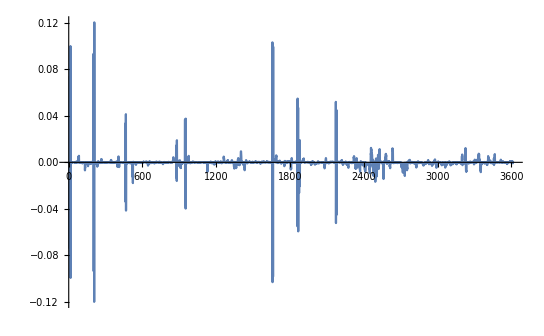

```mathematica
ListLinePlot[rsAlcxWeth, PlotRange->All]
```

```mathematica
edistAlcxWeth = EstimatedDistribution[rsAlcxWeth, StableDistribution[1, aAW, bAW, locAW, scaleAW]]
```

StableDistribution[1,0.838474,-0.181726,0.00011192,0.000231752]

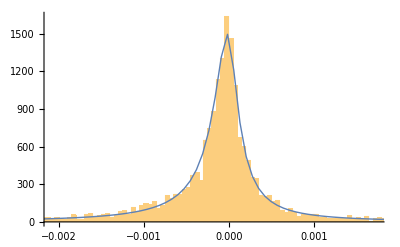

```mathematica
Show[Histogram[rsAlcxWeth, {0.00005}, "PDF"], Plot[PDF[edistAlcxWeth, x], {x, Min[rsAlcxWeth], Max[rsAlcxWeth]}, PlotRange->All, PlotStyle->Thick]]
```

```mathematica
(* That's scary. Caps on payoff obviously very necessary ... *)
```